This is a continuation of the 4.dataAnalysis1LoS, because it was becoming so long

## Second set of dataBases

This databases, unless the first set, have a better set of times. There are different columns allowing identify the times for first or second admission as well as the outcome after each admission. These databases also have the particular bed pathway of each patient.

## DataBase 6

This is the most complete DataBase of COVID-19 patients from 17/03/2020 to 15/08/2021. With this DataBase we made the rest of the databases.

```mathematica
dataBase20202021=Import["/home/lina/Documents/UnCover/datos_INS/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase20202021//Length
```

245372

```mathematica
dataBase20202021[[All,12]]
```

{SymptomOnset,4/3/2020 0:00:00,2/3/2020 0:00:00,6/3/2020 0:00:00,6/3/2020 0:00:00,7/3/2020 0:00:00,8/3/2020 0:00:00,9/3/2020 0:00:00,12/3/2020 0:00:00,9/3/2020 0:00:00,10/3/2020 0:00:00,15/3/2020 0:00:00,12/3/2020 0:00:00,14/3/2020 0:00:00,14/3/2020 0:00:00,13/3/2020 0:00:00,16/3/2020 0:00:00,14/3/2020 0:00:00,10/3/2020 0:00:00,10/3/2020 0:00:00,18/3/2020 0:00:00,12/3/2020 0:00:00,245328,10/8/2021 0:00:00,9/8/2021 0:00:00,26/7/2021 0:00:00,25/7/2021 0:00:00,26/7/2021 0:00:00,12/6/2021 0:00:00,7/8/2021 0:00:00,31/7/2021 0:00:00,4/8/2021 0:00:00,9/8/2021 0:00:00,6/8/2021 0:00:00,10/8/2021 0:00:00,11/8/2021 0:00:00,25/7/2021 0:00:00,8/6/2021 0:00:00,9/8/2021 0:00:00,8/8/2021 0:00:00,29/7/2021 0:00:00,31/7/2021 0:00:00,8/8/2021 0:00:00,4/8/2021 0:00:00,9/8/2021 0:00:00}
 |  |  |  |

### Deleting N/A s from INS

```mathematica
dataBase20202021[[All,14]]//Tally
```

{{outcomeINS,1},{Recuperado,191424},{Fallecido,53246},{fallecido,156},{Fallecido ,427},{Recuperado ,9},{N/A,4},{Activo,109}}

```mathematica
Select[dataBase20202021,#[[14]]=="N/A"&]
```

{{158608,1689337,73,TOLIMA,73001,IBAGUE,83,1,F,6,,20/12/2020 0:00:00,4/1/2021 0:00:00,N/A,26/1/2021 0:00:00,,Tue 5 Jan 2021,,,,,,,},{158695,1690212,73,TOLIMA,73001,IBAGUE,81,1,M,6,,22/12/2020 0:00:00,5/1/2021 0:00:00,N/A,19/3/2021 0:00:00,,Tue 5 Jan 2021,,,,,,,},{160569,1726370,73,TOLIMA,73001,IBAGUE,9,1,M,6,,23/12/2020 0:00:00,6/1/2021 0:00:00,N/A,5/2/2021 0:00:00,,Thu 7 Jan 2021,,,Mon 18 Jan 2021,Mon 18 Jan 2021,,,Tue 19 Jan 2021},{162291,1766375,73,TOLIMA,73001,IBAGUE,74,1,M,6,,21/12/2020 0:00:00,4/1/2021 0:00:00,N/A,19/4/2021 0:00:00,,Sat 9 Jan 2021,Sun 24 Jan 2021,,,,,,}}

```mathematica
Select[dataBase20202021,#[[15]]=="N/A"&]
```

{}

```mathematica
dataBase20202021c=DeleteCases[dataBase20202021,{_,_,_,_,_,_,_,_,_,_,_,_,_,"N/A",__}];
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataBase20202021.m",dataBase20202021c];
```

```mathematica
dataBase20202021=dataBase20202021c;
```

```mathematica
(********************************************************************************************************************)
```

```mathematica
(* Se supone que mi base de datos es de pacientes hospiatalizados con un outcome definido. Pero aparecen casos Activos*)
```

```mathematica
(Select[dataBase20202021,#[[14]]=="Activo"&][[All,{15,16}]]/.{({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[x,DateObject[___]])->bothDate,
({x_,y_}/;MatchQ[x,DateObject[___]])->xbothDate,({x_,y_}/;MatchQ[y,DateObject[___]])->ybothDate})//Tally (*segun esto - los casos Activos no tienen fechas de recuperacion o muerte*)
```

{{{,},109}}

```mathematica
(Select[dataBase20202021,#[[14]]=="Activo"&][[All,17;;24]]/.DateObject[___]->data)//Tally (* cómo son esos casos en las fechas que yo estimé. Pueden ser casos que ya salieron del H/ICU pero aún no se recuperan en Casa*)
```

{{{,,,,data,data,,},14},{{data,data,,,,,,},91},{{data,data,,data,data,,,data},1},{{data,data,,,data,,,data},1},{{data,,,data,data,data,,},2}}

```mathematica
(********************************************************************************************************************)
```

### Pathways

```mathematica
var1=Map[SortBy[DeleteCases[{{"AdHospital",#[[1]]},{"RecoveryH",#⟦2⟧},{"DeceasedH",#⟦3⟧},{"transferredICU",#⟦4⟧},{"AdICU",#⟦5⟧},{"RecoveryICU",#⟦6⟧},{"DeceasedICU",#⟦7⟧},{"transferredH",#⟦8⟧}} ,{_,""}],Last][[All,1]]&,dataBase20202021[[2;;,17;;24]]];(* Aqui encontramos la pathway de cada caso ordenando por fecha y estados "AsHospital,..."*)
```

```mathematica
(***************************************************************+Identificando las rutas y su frecuencia******)
```

```mathematica
var1//Tally//SortBy[#,Last]&//Reverse
```

{{{AdHospital,RecoveryH},161773},{{AdHospital,DeceasedH},32714},{{AdICU,RecoveryICU},18646},{{AdICU,DeceasedICU},13239},{{AdHospital,AdICU,transferredICU,RecoveryICU},4682},{{AdICU,AdHospital,transferredH,RecoveryH},3315},{{AdHospital,AdICU,transferredICU,DeceasedICU},3263},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryH},1717},{{AdHospital,RecoveryH,DeceasedH},1208},{{AdHospital,DeceasedH,RecoveryH},825},{{AdHospital,RecoveryH,AdICU,RecoveryICU},526},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryICU},329},{{AdICU,RecoveryICU,AdHospital,RecoveryH},269},{{AdICU,AdHospital,transferredH,DeceasedH},244},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryH},238},{{AdICU,RecoveryICU,DeceasedICU},220},{{AdHospital,AdICU,transferredICU,RecoveryICU,RecoveryH},214},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU},198},{{AdICU,RecoveryICU,AdHospital,transferredH,RecoveryH},168},{{AdICU,DeceasedICU,AdHospital,DeceasedH},119},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedH},113},{{AdHospital,RecoveryH,AdICU,transferredICU,RecoveryICU},107},{{AdICU,AdHospital,transferredH,transferredICU,DeceasedICU},105},{{AdHospital,DeceasedH,AdICU,DeceasedICU},86},{{AdHospital,AdICU,transferredICU,RecoveryICU,DeceasedICU},84},{{AdHospital,RecoveryH,AdICU,DeceasedICU},84},{{AdHospital,RecoveryH,AdICU,transferredICU,transferredH},83},{{AdHospital,AdICU,transferredICU,DeceasedICU,DeceasedH},81},{{AdICU,RecoveryICU,AdHospital,transferredH,transferredICU},75},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedICU},70},{{AdHospital,AdICU,transferredICU,RecoveryICU,transferredH,RecoveryH},69},{{AdHospital,AdICU,transferredICU,RecoveryICU,transferredH},52},{{AdHospital,RecoveryH,AdICU,transferredICU,DeceasedICU},40},{{AdICU,DeceasedICU,RecoveryICU},32},{{AdHospital},31},{{AdHospital,RecoveryH,AdICU,transferredH},28},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryICU,RecoveryH},20},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryH,RecoveryICU},20},{{AdHospital,RecoveryH,AdICU,RecoveryICU,DeceasedICU},20},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU,RecoveryH},19},{{AdICU,AdHospital,transferredH,RecoveryH,RecoveryICU},19},{{AdICU,AdHospital,transferredH,transferredICU,DeceasedH},18},{{AdHospital,AdICU,transferredICU,DeceasedICU,RecoveryICU},18},{{AdHospital,RecoveryH,AdICU,RecoveryICU,transferredH},14},{{AdICU,RecoveryICU,AdHospital,DeceasedH},10},{{AdICU,DeceasedICU,AdHospital,RecoveryH},10},{{AdICU,AdHospital,transferredH,RecoveryH,DeceasedH},9},{{AdICU,AdHospital,transferredH,DeceasedH,RecoveryH},9},{{AdHospital,RecoveryH,AdICU,transferredICU,transferredH,RecoveryICU},8},{{AdHospital,DeceasedH,AdICU,RecoveryICU},7},{{AdICU},7},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryH,RecoveryICU},6},{{AdHospital,AdICU,transferredICU,RecoveryICU,DeceasedH,RecoveryH},6},{{AdHospital,RecoveryH,AdICU,transferredICU,RecoveryICU,transferredH},5},{{AdHospital,AdICU,transferredICU,RecoveryICU,DeceasedH},5},{{AdICU,RecoveryICU,AdHospital,transferredH,transferredICU,RecoveryH},4},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedH,RecoveryH},4},{{AdHospital,AdICU,transferredICU,RecoveryICU,DeceasedICU,transferredH},4},{{AdICU,DeceasedICU,RecoveryICU,AdHospital,transferredH,RecoveryH},3},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU,DeceasedICU},3},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryH,DeceasedICU},3},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryH,DeceasedH},3},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedICU,RecoveryICU},3},{{AdHospital,RecoveryH,DeceasedH,AdICU,RecoveryICU},3},{{AdICU,RecoveryICU,DeceasedICU,AdHospital,transferredH,RecoveryH},2},{{AdICU,RecoveryICU,AdHospital,transferredICU,transferredH,RecoveryH},2},{{AdICU,DeceasedICU,RecoveryICU,AdHospital,transferredH,transferredICU},2},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryICU,DeceasedICU},2},{{AdICU,AdHospital,transferredH,transferredICU,DeceasedICU,RecoveryICU},2},{{AdHospital,RecoveryH,AdICU,transferredICU,transferredH,DeceasedICU},2},{{AdHospital,RecoveryH,AdICU,transferredICU,transferredH,DeceasedH},2},{{AdHospital,RecoveryH,AdICU,transferredH,transferredICU,RecoveryICU},2},{{AdHospital,DeceasedH,RecoveryH,AdICU,transferredICU,RecoveryICU},2},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedICU,DeceasedH},2},{{AdHospital,AdICU,transferredICU,RecoveryICU,RecoveryH,DeceasedH},2},{{AdICU,RecoveryICU,AdHospital,transferredH,DeceasedH},2},{{AdICU,RecoveryICU,AdHospital,transferredICU},2},{{AdHospital,RecoveryH,AdICU},2},{{AdHospital,AdICU,transferredICU},2},{{AdHospital,AdICU,transferredICU,RecoveryICU,DeceasedICU,transferredH,RecoveryH},1},{{AdICU,RecoveryICU,AdHospital,transferredICU,transferredH,DeceasedH},1},{{AdICU,RecoveryICU,AdHospital,transferredH,transferredICU,DeceasedICU},1},{{AdICU,RecoveryICU,AdHospital,transferredH,RecoveryH,DeceasedH},1},{{AdICU,RecoveryICU,AdHospital,RecoveryH,transferredICU,transferredH},1},{{AdICU,DeceasedICU,AdHospital,transferredH,transferredICU,RecoveryICU},1},{{AdICU,DeceasedICU,AdHospital,transferredH,transferredICU,RecoveryH},1},{{AdICU,DeceasedICU,AdHospital,transferredH,RecoveryH,DeceasedH},1},{{AdICU,AdHospital,transferredH,RecoveryH,transferredICU,RecoveryICU},1},{{AdICU,AdHospital,transferredH,RecoveryH,transferredICU,DeceasedICU},1},{{AdICU,AdHospital,transferredH,RecoveryH,DeceasedICU,RecoveryICU},1},{{AdICU,AdHospital,transferredH,RecoveryH,DeceasedICU,DeceasedH},1},{{AdHospital,RecoveryH,AdICU,transferredICU,RecoveryICU,DeceasedICU},1},{{AdHospital,RecoveryH,AdICU,RecoveryICU,transferredH,transferredICU},1},{{AdHospital,DeceasedH,AdICU,transferredICU,transferredH,RecoveryH},1},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU,DeceasedH},1},{{AdHospital,AdICU,transferredICU,RecoveryICU,transferredH,DeceasedH},1},{{AdHospital,AdICU,transferredICU,DeceasedICU,transferredH,RecoveryICU},1},{{AdHospital,AdICU,transferredICU,DeceasedICU,RecoveryICU,transferredH},1},{{AdICU,RecoveryICU,DeceasedICU,AdHospital,RecoveryH},1},{{AdICU,RecoveryICU,AdHospital,RecoveryH,transferredH},1},{{AdICU,RecoveryICU,AdHospital,RecoveryH,DeceasedICU},1},{{AdICU,RecoveryICU,AdHospital,RecoveryH,DeceasedH},1},{{AdICU,RecoveryICU,AdHospital,DeceasedH,RecoveryH},1},{{AdICU,DeceasedICU,AdHospital,transferredH,RecoveryH},1},{{AdICU,AdHospital,transferredH,RecoveryH,transferredICU},1},{{AdICU,AdHospital,transferredH,RecoveryH,DeceasedICU},1},{{AdHospital,RecoveryH,DeceasedH,AdICU,DeceasedICU},1},{{AdHospital,RecoveryH,AdICU,transferredH,DeceasedH},1},{{AdHospital,RecoveryH,AdICU,RecoveryICU,DeceasedH},1},{{AdHospital,RecoveryH,AdICU,DeceasedICU,transferredH},1},{{AdHospital,RecoveryH,AdICU,DeceasedICU,RecoveryICU},1},{{AdHospital,AdICU,transferredICU,DeceasedICU,RecoveryH},1},{{AdHospital,AdICU,RecoveryICU},1}}

```mathematica
(* No se considera las rutas en las que el casos tienen más de un outcome recuperadoH/ICU o deceasedH/ICU *)
```

```mathematica
var2=(var1//Tally//SortBy[#,Last]&//Reverse)/.({{___,x_,___,y_,___},_}/;(StringMatchQ[x,"Recovery"~~___]||StringMatchQ[x,"Deceased"~~___])&&(StringMatchQ[y,"Recovery"~~___]||StringMatchQ[y,"Deceased"~~___]))->Nothing;
```

```mathematica
var21=Map[{Sequence@@PadRight[#[[1]],5,""],#[[2]],(#[[2]]*100/Length[var1]//N)}&,var2]
```

{{AdHospital,RecoveryH,,,,161773,65.93},{AdHospital,DeceasedH,,,,32714,13.3325},{AdICU,RecoveryICU,,,,18646,7.59911},{AdICU,DeceasedICU,,,,13239,5.3955},{AdHospital,AdICU,transferredICU,RecoveryICU,,4682,1.90813},{AdICU,AdHospital,transferredH,RecoveryH,,3315,1.35102},{AdHospital,AdICU,transferredICU,DeceasedICU,,3263,1.32982},{AdHospital,AdICU,transferredICU,transferredH,RecoveryH,1717,0.699757},{AdICU,AdHospital,transferredH,transferredICU,RecoveryICU,329,0.134083},{AdICU,AdHospital,transferredH,DeceasedH,,244,0.0994413},{AdICU,AdHospital,transferredH,transferredICU,RecoveryH,238,0.096996},{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU,198,0.0806941},{AdHospital,AdICU,transferredICU,transferredH,DeceasedH,113,0.0460527},{AdICU,AdHospital,transferredH,transferredICU,DeceasedICU,105,0.0427923},{AdHospital,RecoveryH,AdICU,transferredICU,transferredH,83,0.0338263},{AdICU,RecoveryICU,AdHospital,transferredH,transferredICU,75,0.030566},{AdHospital,AdICU,transferredICU,transferredH,DeceasedICU,70,0.0285282},{AdHospital,AdICU,transferredICU,RecoveryICU,transferredH,52,0.0211924},{AdHospital,,,,,31,0.0126339},{AdHospital,RecoveryH,AdICU,transferredH,,28,0.0114113},{AdICU,AdHospital,transferredH,transferredICU,DeceasedH,18,0.00733583},{AdICU,,,,,7,0.00285282},{AdICU,RecoveryICU,AdHospital,transferredICU,,2,0.000815092},{AdHospital,RecoveryH,AdICU,,,2,0.000815092},{AdHospital,AdICU,transferredICU,,,2,0.000815092},{AdICU,AdHospital,transferredH,RecoveryH,transferredICU,1,0.000407546},{AdHospital,AdICU,RecoveryICU,,,1,0.000407546}}

```mathematica
var22={{"Bed Pathway",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"n","%","Accumulate %"},Sequence@@Map[Flatten,Transpose[{var21,Accumulate[var21[[All,-1]]]}]]};
```

```mathematica
Grid[var22,Frame->All]
```

Bed Pathway |  |  |  |  | n | % | Accumulate %
AdHospital | RecoveryH |  |  |  | 161773 | 65.93 | 65.93
AdHospital | DeceasedH |  |  |  | 32714 | 13.3325 | 79.2624
AdICU | RecoveryICU |  |  |  | 18646 | 7.59911 | 86.8615
AdICU | DeceasedICU |  |  |  | 13239 | 5.3955 | 92.257
AdHospital | AdICU | transferredICU | RecoveryICU |  | 4682 | 1.90813 | 94.1652
AdICU | AdHospital | transferredH | RecoveryH |  | 3315 | 1.35102 | 95.5162
AdHospital | AdICU | transferredICU | DeceasedICU |  | 3263 | 1.32982 | 96.846
AdHospital | AdICU | transferredICU | transferredH | RecoveryH | 1717 | 0.699757 | 97.5458
AdICU | AdHospital | transferredH | transferredICU | RecoveryICU | 329 | 0.134083 | 97.6798
AdICU | AdHospital | transferredH | DeceasedH |  | 244 | 0.0994413 | 97.7793
AdICU | AdHospital | transferredH | transferredICU | RecoveryH | 238 | 0.096996 | 97.8763
AdHospital | AdICU | transferredICU | transferredH | RecoveryICU | 198 | 0.0806941 | 97.957
AdHospital | AdICU | transferredICU | transferredH | DeceasedH | 113 | 0.0460527 | 98.003
AdICU | AdHospital | transferredH | transferredICU | DeceasedICU | 105 | 0.0427923 | 98.0458
AdHospital | RecoveryH | AdICU | transferredICU | transferredH | 83 | 0.0338263 | 98.0796
AdICU | RecoveryICU | AdHospital | transferredH | transferredICU | 75 | 0.030566 | 98.1102
AdHospital | AdICU | transferredICU | transferredH | DeceasedICU | 70 | 0.0285282 | 98.1387
AdHospital | AdICU | transferredICU | RecoveryICU | transferredH | 52 | 0.0211924 | 98.1599
AdHospital |  |  |  |  | 31 | 0.0126339 | 98.1726
AdHospital | RecoveryH | AdICU | transferredH |  | 28 | 0.0114113 | 98.184
AdICU | AdHospital | transferredH | transferredICU | DeceasedH | 18 | 0.00733583 | 98.1913
AdICU |  |  |  |  | 7 | 0.00285282 | 98.1942
AdICU | RecoveryICU | AdHospital | transferredICU |  | 2 | 0.000815092 | 98.195
AdHospital | RecoveryH | AdICU |  |  | 2 | 0.000815092 | 98.1958
AdHospital | AdICU | transferredICU |  |  | 2 | 0.000815092 | 98.1966
AdICU | AdHospital | transferredH | RecoveryH | transferredICU | 1 | 0.000407546 | 98.197
AdHospital | AdICU | RecoveryICU |  |  | 1 | 0.000407546 | 98.1974

```mathematica
(* Eliminamos las rutas que no tengan un outcome definido / es decir que el ultimo estado no sea RecoveryH/ICU o DeceasedH/ICU*)
```

```mathematica
var3=var2/.({{___,x_},_}/;StringMatchQ[x,"Ad"~~___]||StringMatchQ[x,"trans"~~___])->Nothing
```

{{{AdHospital,RecoveryH},161773},{{AdHospital,DeceasedH},32714},{{AdICU,RecoveryICU},18646},{{AdICU,DeceasedICU},13239},{{AdHospital,AdICU,transferredICU,RecoveryICU},4682},{{AdICU,AdHospital,transferredH,RecoveryH},3315},{{AdHospital,AdICU,transferredICU,DeceasedICU},3263},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryH},1717},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryICU},329},{{AdICU,AdHospital,transferredH,DeceasedH},244},{{AdICU,AdHospital,transferredH,transferredICU,RecoveryH},238},{{AdHospital,AdICU,transferredICU,transferredH,RecoveryICU},198},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedH},113},{{AdICU,AdHospital,transferredH,transferredICU,DeceasedICU},105},{{AdHospital,AdICU,transferredICU,transferredH,DeceasedICU},70},{{AdICU,AdHospital,transferredH,transferredICU,DeceasedH},18},{{AdHospital,AdICU,RecoveryICU},1}}

```mathematica
Grid[{{"Bed Pathway",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"n"},Sequence@@Map[Flatten,var3]},Frame->All]
```

Bed Pathway |  |  |  |  | n
AdHospital | RecoveryH | 161773 |  |  | 
AdHospital | DeceasedH | 32714 |  |  | 
AdICU | RecoveryICU | 18646 |  |  | 
AdICU | DeceasedICU | 13239 |  |  | 
AdHospital | AdICU | transferredICU | RecoveryICU | 4682 | 
AdICU | AdHospital | transferredH | RecoveryH | 3315 | 
AdHospital | AdICU | transferredICU | DeceasedICU | 3263 | 
AdHospital | AdICU | transferredICU | transferredH | RecoveryH | 1717
AdICU | AdHospital | transferredH | transferredICU | RecoveryICU | 329
AdICU | AdHospital | transferredH | DeceasedH | 244 | 
AdICU | AdHospital | transferredH | transferredICU | RecoveryH | 238
AdHospital | AdICU | transferredICU | transferredH | RecoveryICU | 198
AdHospital | AdICU | transferredICU | transferredH | DeceasedH | 113
AdICU | AdHospital | transferredH | transferredICU | DeceasedICU | 105
AdHospital | AdICU | transferredICU | transferredH | DeceasedICU | 70
AdICU | AdHospital | transferredH | transferredICU | DeceasedH | 18
AdHospital | AdICU | RecoveryICU | 1 |  |

```mathematica
var31=Map[{Sequence@@PadRight[#[[1]]/.({a__,x_,y_,b__}/;x==y)->{a,x,b},4,""],#[[2]],(#[[2]]*100/Length[var1]//N)}&,var3/.{"AdHospital"->H,"RecoveryH"->RH,"DeceasedH"->"DH","AdICU"->ICU,"RecoveryICU"->RICU,"DeceasedICU"->"DICU","transferredICU"->ICU,"transferredH"->H}]
```

{{H,RH,,,161773,65.93},{H,DH,,,32714,13.3325},{ICU,RICU,,,18646,7.59911},{ICU,DICU,,,13239,5.3955},{H,ICU,RICU,,4682,1.90813},{ICU,H,RH,,3315,1.35102},{H,ICU,DICU,,3263,1.32982},{H,ICU,H,RH,1717,0.699757},{ICU,H,ICU,RICU,329,0.134083},{ICU,H,DH,,244,0.0994413},{ICU,H,ICU,RH,238,0.096996},{H,ICU,H,RICU,198,0.0806941},{H,ICU,H,DH,113,0.0460527},{ICU,H,ICU,DICU,105,0.0427923},{H,ICU,H,DICU,70,0.0285282},{ICU,H,ICU,DH,18,0.00733583},{H,ICU,RICU,,1,0.000407546}}

```mathematica
var32={{"Bed Pathway",SpanFromLeft,SpanFromLeft,SpanFromLeft,"n","%","Accumulate %"},Sequence@@Map[Flatten,Transpose[{var31,Accumulate[var31[[All,-1]]]}]]};
```

```mathematica
Grid[var32,Frame->All]
```

Bed Pathway |  |  |  | n | % | Accumulate %
H | RH |  |  | 161773 | 65.93 | 65.93
H | DH |  |  | 32714 | 13.3325 | 79.2624
ICU | RICU |  |  | 18646 | 7.59911 | 86.8615
ICU | DICU |  |  | 13239 | 5.3955 | 92.257
H | ICU | RICU |  | 4682 | 1.90813 | 94.1652
ICU | H | RH |  | 3315 | 1.35102 | 95.5162
H | ICU | DICU |  | 3263 | 1.32982 | 96.846
H | ICU | H | RH | 1717 | 0.699757 | 97.5458
ICU | H | ICU | RICU | 329 | 0.134083 | 97.6798
ICU | H | DH |  | 244 | 0.0994413 | 97.7793
ICU | H | ICU | RH | 238 | 0.096996 | 97.8763
H | ICU | H | RICU | 198 | 0.0806941 | 97.957
H | ICU | H | DH | 113 | 0.0460527 | 98.003
ICU | H | ICU | DICU | 105 | 0.0427923 | 98.0458
H | ICU | H | DICU | 70 | 0.0285282 | 98.0743
ICU | H | ICU | DH | 18 | 0.00733583 | 98.0817
H | ICU | RICU |  | 1 | 0.000407546 | 98.0821

```mathematica
Grid[var32//SortBy[#,First]&,Frame->All]
```

Bed Pathway |  |  |  | n | % | Accumulate %
H | DH |  |  | 32714 | 13.3325 | 79.2624
H | ICU | DICU |  | 3263 | 1.32982 | 96.846
H | ICU | H | DH | 113 | 0.0460527 | 98.003
H | ICU | H | DICU | 70 | 0.0285282 | 98.0743
H | ICU | H | RH | 1717 | 0.699757 | 97.5458
H | ICU | H | RICU | 198 | 0.0806941 | 97.957
H | ICU | RICU |  | 1 | 0.000407546 | 98.0821
H | ICU | RICU |  | 4682 | 1.90813 | 94.1652
H | RH |  |  | 161773 | 65.93 | 65.93
ICU | DICU |  |  | 13239 | 5.3955 | 92.257
ICU | H | DH |  | 244 | 0.0994413 | 97.7793
ICU | H | ICU | DH | 18 | 0.00733583 | 98.0817
ICU | H | ICU | DICU | 105 | 0.0427923 | 98.0458
ICU | H | ICU | RH | 238 | 0.096996 | 97.8763
ICU | H | ICU | RICU | 329 | 0.134083 | 97.6798
ICU | H | RH |  | 3315 | 1.35102 | 95.5162
ICU | RICU |  |  | 18646 | 7.59911 | 86.8615

```mathematica
(***************************************************************+Creando la variale-columna Pathway for patient******)
```

```mathematica
(*PRIMERO: Homogenizamos los estados con otros Strings*)
```

```mathematica
nvar2=Map[(#/.({a__,x_,y_,b__}/;x==y)->{a,x,b})&,(var1/.{"AdHospital"->"H","RecoveryH"->"RH","DeceasedH"->"DH","AdICU"->"ICU","RecoveryICU"->"RICU","DeceasedICU"->"DICU","transferredICU"->"ICU","transferredH"->"H"})]
```

{{H,RH},{H,RH},{H,RH},{H,RH},{H,RH},{H,RH},{H,RH},{H,RH},{H,ICU,RICU},{H,RH},{H,RH},{H,ICU,RICU},{H,RH},{H,RH},{H,RH},{H,RH,ICU,H,ICU,RICU},{H,ICU,RICU},{H,ICU,RICU},{ICU,DICU},{H,ICU,DICU},{H,DH},{ICU,H,RH},{H,RH},{H,ICU,H,RICU},{H,ICU,RICU},{ICU,RICU},{H,ICU,RICU},{H,DH},{H,RH},{H,RH},{H,ICU,RICU,RH},{H,RH},{ICU,H,RH},245306,{H,DH},{H,RH},{H,RH},{H,DH},{ICU,DICU},{ICU,DICU},{ICU,DICU},{H,DH},{H,DH},{H,DH},{H,DH},{ICU,DICU},{H,DH},{H,DH},{H,DH},{H,DH},{H,DH},{ICU,DICU},{ICU,DICU},{H,DH},{H,DH},{H,DH},{ICU,DICU},{H,DH},{H,DH},{H,DH},{H,DH},{H,DH},{ICU,DICU},{H,DH},{H,DH},{H,DH}}
 |  |  |  |

```mathematica
nvar2//Tally//SortBy[#,Last]&//Reverse
```

{{{H,RH},161773},{{H,DH},32714},{{ICU,RICU},18646},{{ICU,DICU},13239},{{H,ICU,RICU},4683},{{ICU,H,RH},3315},{{H,ICU,DICU},3263},{{H,ICU,H,RH},1717},{{H,RH,DH},1208},{{H,DH,RH},825},{{H,RH,ICU,RICU},633},{{ICU,RICU,H,RH},437},{{ICU,H,ICU,RICU},329},{{ICU,H,DH},244},{{ICU,H,ICU,RH},238},{{ICU,RICU,DICU},220},{{H,ICU,RICU,RH},214},{{H,ICU,H,RICU},198},{{H,RH,ICU,DICU},124},{{ICU,DICU,H,DH},119},{{H,ICU,H,DH},113},{{H,RH,ICU,H},111},{{ICU,H,ICU,DICU},105},{{H,DH,ICU,DICU},86},{{H,ICU,RICU,DICU},84},{{H,ICU,DICU,DH},81},{{ICU,RICU,H,ICU},77},{{H,ICU,H,DICU},70},{{H,ICU,RICU,H,RH},69},{{H,ICU,RICU,H},52},{{ICU,DICU,RICU},32},{{H},31},{{H,RH,ICU,RICU,DICU},21},{{ICU,H,ICU,RICU,RH},20},{{H,ICU,H,RH,RICU},20},{{H,RH,ICU,RICU,H},19},{{H,ICU,H,RICU,RH},19},{{ICU,H,RH,RICU},19},{{ICU,H,ICU,DH},18},{{H,ICU,DICU,RICU},18},{{ICU,RICU,H,DH},12},{{ICU,DICU,H,RH},11},{{ICU,H,RH,DH},9},{{ICU,H,DH,RH},9},{{H,RH,ICU,H,RICU},8},{{H,DH,ICU,RICU},7},{{ICU},7},{{ICU,H,ICU,RH,RICU},6},{{H,ICU,RICU,DH,RH},6},{{H,ICU,RICU,DH},5},{{ICU,RICU,H,ICU,RH},4},{{H,ICU,RICU,DICU,H},4},{{H,ICU,H,DH,RH},4},{{ICU,RICU,DICU,H,RH},3},{{ICU,DICU,RICU,H,RH},3},{{H,RH,ICU,H,DH},3},{{H,RH,DH,ICU,RICU},3},{{H,ICU,H,RICU,DICU},3},{{H,ICU,H,RH,DICU},3},{{H,ICU,H,RH,DH},3},{{H,ICU,H,DICU,RICU},3},{{ICU,RICU,H,ICU,H,RH},2},{{H,RH,ICU,H,ICU,RICU},2},{{ICU,RICU,H,RH,DH},2},{{ICU,H,ICU,RICU,DICU},2},{{ICU,H,ICU,DICU,RICU},2},{{ICU,DICU,RICU,H,ICU},2},{{H,RH,ICU,H,DICU},2},{{H,ICU,RICU,RH,DH},2},{{H,ICU,H,DICU,DH},2},{{H,DH,RH,ICU,RICU},2},{{H,RH,ICU},2},{{H,ICU,ICU},2},{{ICU,RICU,H,RH,ICU,H},1},{{ICU,RICU,H,ICU,H,DH},1},{{H,RH,ICU,RICU,H,ICU},1},{{H,ICU,RICU,DICU,H,RH},1},{{ICU,RICU,H,RH,H},1},{{ICU,RICU,H,RH,DICU},1},{{ICU,RICU,H,ICU,DICU},1},{{ICU,RICU,H,DH,RH},1},{{ICU,H,RH,ICU,RICU},1},{{ICU,H,RH,ICU,DICU},1},{{ICU,H,RH,DICU,RICU},1},{{ICU,H,RH,DICU,DH},1},{{ICU,DICU,H,RH,DH},1},{{ICU,DICU,H,ICU,RICU},1},{{ICU,DICU,H,ICU,RH},1},{{H,RH,ICU,RICU,DH},1},{{H,RH,ICU,DICU,RICU},1},{{H,RH,ICU,DICU,H},1},{{H,RH,DH,ICU,DICU},1},{{H,ICU,RICU,H,DH},1},{{H,ICU,H,RICU,DH},1},{{H,ICU,DICU,RICU,H},1},{{H,ICU,DICU,H,RICU},1},{{H,DH,ICU,H,RH},1},{{ICU,H,RH,ICU},1},{{ICU,H,RH,DICU},1},{{H,ICU,DICU,RH},1}}

```mathematica
(* SEGUNDO : identifico las bed pathways* )
```

```mathematica
bedPathways=DeleteCases[Map[#[[1]]/.({a__,x_,y_,b__}/;x==y)->{a,x,b}&,var3/.{"AdHospital"->"H","RecoveryH"->"RH","DeceasedH"->"DH","AdICU"->"ICU","RecoveryICU"->"RICU","DeceasedICU"->"DICU","transferredICU"->"ICU","transferredH"->"H"}],{"ICU","H","ICU","RH"}|{"H","ICU","H","RICU"}|{"H","ICU","H","DICU"}|{"ICU","H","ICU","DH"}]//DeleteDuplicates
```

{{H,RH},{H,DH},{ICU,RICU},{ICU,DICU},{H,ICU,RICU},{ICU,H,RH},{H,ICU,DICU},{H,ICU,H,RH},{ICU,H,ICU,RICU},{ICU,H,DH},{H,ICU,H,DH},{ICU,H,ICU,DICU}}

```mathematica
(* TERCERO : NAs para casos que  no match con las bed pathways * )
```

Syntax::bktmop: Expression "TERCERO:NAsparacasosquenomatchconlasbedpathways*)" has no opening "(".

```mathematica
casesWithBedP=Flatten[Position[nvar2,Alternatives[Sequence@@bedPathways]]];
```

```mathematica
casesWithoutBedP=Partition[Complement[Range[1,Length[var1]],casesWithBedP],1];
```

```mathematica
variablePath1=Map[(#/.({a__,x_,y_,b__}/;x==y)->{a,x,b})&,(ReplacePart[var1,casesWithoutBedP->"NA"]/.{"AdHospital"->"H","RecoveryH"->"RH","DeceasedH"->"DH","AdICU"->"ICU","RecoveryICU"->"RICU","DeceasedICU"->"DICU","transferredICU"->"ICU","transferredH"->"H"})];
```

```mathematica
(* CUARTO: Compruebo que las pathways tengan las mismas % estimados anteriormente *)
```

```mathematica
variablePath1//Tally
```

{{{H,RH},161773},{{H,ICU,RICU},4683},{NA,5230},{{ICU,DICU},13239},{{H,ICU,DICU},3263},{{H,DH},32714},{{ICU,H,RH},3315},{{ICU,RICU},18646},{{H,ICU,H,DH},113},{{H,ICU,H,RH},1717},{{ICU,H,ICU,RICU},329},{{ICU,H,ICU,DICU},105},{{ICU,H,DH},244}}

```mathematica
variablePath12=Map[{Sequence@@PadRight[#[[1]],4,""],#[[2]],(#[[2]]*100/Length[var1]//N)}&,DeleteCases[variablePath1//Tally,{"NA",5230}]]
```

{{H,RH,,,161773,65.93},{H,ICU,RICU,,4683,1.90854},{ICU,DICU,,,13239,5.3955},{H,ICU,DICU,,3263,1.32982},{H,DH,,,32714,13.3325},{ICU,H,RH,,3315,1.35102},{ICU,RICU,,,18646,7.59911},{H,ICU,H,DH,113,0.0460527},{H,ICU,H,RH,1717,0.699757},{ICU,H,ICU,RICU,329,0.134083},{ICU,H,ICU,DICU,105,0.0427923},{ICU,H,DH,,244,0.0994413}}

```mathematica
variablePath13={{"Bed Pathway",SpanFromLeft,SpanFromLeft,SpanFromLeft,"n","%","Accumulate %"},Sequence@@Map[Flatten,Transpose[{variablePath12,Accumulate[variablePath12[[All,-1]]]}]]};
```

```mathematica
Grid[variablePath13,Frame->All]
```

Bed Pathway |  |  |  | n | % | Accumulate %
H | RH |  |  | 161773 | 65.93 | 65.93
H | ICU | RICU |  | 4683 | 1.90854 | 67.8385
ICU | DICU |  |  | 13239 | 5.3955 | 73.234
H | ICU | DICU |  | 3263 | 1.32982 | 74.5638
H | DH |  |  | 32714 | 13.3325 | 87.8963
ICU | H | RH |  | 3315 | 1.35102 | 89.2473
ICU | RICU |  |  | 18646 | 7.59911 | 96.8464
H | ICU | H | DH | 113 | 0.0460527 | 96.8925
H | ICU | H | RH | 1717 | 0.699757 | 97.5922
ICU | H | ICU | RICU | 329 | 0.134083 | 97.7263
ICU | H | ICU | DICU | 105 | 0.0427923 | 97.7691
ICU | H | DH |  | 244 | 0.0994413 | 97.8685

```mathematica
(* QUINTO: Estimamosos % de casos por ruta sin contar los NAs  *)
```

```mathematica
total=Length[var1]-Count[variablePath1,"NA"]
```

240141

```mathematica
variablePath12=Map[{Sequence@@PadRight[#[[1]],4,""],#[[2]],(#[[2]]*100/total//N)}&,DeleteCases[variablePath1//Tally,{"NA",5230}]]//SortBy[#,Last]&//Reverse
```

{{H,RH,,,161773,67.3658},{H,DH,,,32714,13.6228},{ICU,RICU,,,18646,7.7646},{ICU,DICU,,,13239,5.51301},{H,ICU,RICU,,4683,1.9501},{ICU,H,RH,,3315,1.38044},{H,ICU,DICU,,3263,1.35879},{H,ICU,H,RH,1717,0.714997},{ICU,H,ICU,RICU,329,0.137003},{ICU,H,DH,,244,0.101607},{H,ICU,H,DH,113,0.0470557},{ICU,H,ICU,DICU,105,0.0437243}}

```mathematica
variablePath13={{"Bed Pathway",SpanFromLeft,SpanFromLeft,SpanFromLeft,"n","%","Accumulate %"},Sequence@@Map[Flatten,Transpose[{variablePath12,Accumulate[variablePath12[[All,-1]]]}]]};
```

```mathematica
Grid[variablePath13/.{"RH"->"R","RICU"->"R","DH"->"D","DICU"->"D"},Frame->All]
```

Bed Pathway |  |  |  | n | % | Accumulate %
H | R |  |  | 161773 | 67.3658 | 67.3658
H | D |  |  | 32714 | 13.6228 | 80.9887
ICU | R |  |  | 18646 | 7.7646 | 88.7533
ICU | D |  |  | 13239 | 5.51301 | 94.2663
H | ICU | R |  | 4683 | 1.9501 | 96.2164
ICU | H | R |  | 3315 | 1.38044 | 97.5968
H | ICU | D |  | 3263 | 1.35879 | 98.9556
H | ICU | H | R | 1717 | 0.714997 | 99.6706
ICU | H | ICU | R | 329 | 0.137003 | 99.8076
ICU | H | D |  | 244 | 0.101607 | 99.9092
H | ICU | H | D | 113 | 0.0470557 | 99.9563
ICU | H | ICU | D | 105 | 0.0437243 | 100.

```mathematica
(* SEXTO: Construyo la variable-columna pathway, 1-12 segun el orden de frecuencia*)
```

```mathematica
columna0=(variablePath1/.{"RH"->"R","RICU"->"R","DH"->"D","DICU"->"D"});
```

```mathematica
rulesPath=Thread[DeleteCases[(columna0//Tally//SortBy[#,Last]&//Reverse),{"NA",_}][[All,1]]->Range[1,12]]
```

{{H,R}→1,{H,D}→2,{ICU,R}→3,{ICU,D}→4,{H,ICU,R}→5,{ICU,H,R}→6,{H,ICU,D}→7,{H,ICU,H,R}→8,{ICU,H,ICU,R}→9,{ICU,H,D}→10,{H,ICU,H,D}→11,{ICU,H,ICU,D}→12}

```mathematica
columnaPath=columna0/.rulesPath
```

{1,1,1,1,1,1,1,1,5,1,1,5,1,1,1,NA,5,5,4,7,2,6,1,NA,5,3,5,2,1,1,NA,1,6,1,2,1,1,1,1,NA,6,2,1,1,4,1,1,1,1,3,1,5,7,11,8,3,3,1,3,6,1,1,1,1,1,1,1,5,1,1,1,5,NA,1,1,6,NA,1,1,1,1,5,1,1,NA,1,1,2,1,4,1,1,7,1,3,6,4,4,2,1,1,1,8,NA,1,1,1,5,1,NA,1,NA,1,9,8,1,1,NA,NA,1,1,2,5,3,1,1,1,1,12,1,1,1,1,3,1,3,6,2,NA,1,3,NA,6,1,4,1,9,NA,1,1,4,1,6,7,1,4,1,NA,5,1,1,1,6,NA,1,1,1,NA,6,1,1,1,1,11,4,7,1,1,1,1,1,1,1,1,1,7,1,NA,2,1,1,7,1,2,1,7,1,4,1,1,NA,1,8,1,4,244961,1,2,2,1,2,1,2,2,4,1,4,4,2,2,2,4,2,2,2,2,2,2,2,1,2,2,1,2,2,3,2,2,1,4,2,4,2,2,4,1,1,1,1,1,4,2,2,2,2,4,2,4,2,4,2,2,2,7,2,2,2,2,1,4,2,2,2,1,3,1,1,1,4,2,2,2,4,4,4,2,2,2,2,2,2,2,4,1,1,7,2,4,4,2,7,4,2,2,7,2,2,2,2,4,2,7,2,4,2,4,2,1,1,3,4,4,4,4,1,1,4,1,2,4,4,2,2,1,2,1,2,2,2,4,2,2,2,1,2,2,4,2,1,2,2,2,2,2,2,4,1,2,4,2,4,2,2,1,2,2,4,2,2,2,2,2,2,2,4,2,2,2,4,2,1,1,2,4,4,4,2,2,2,2,4,2,2,2,2,2,4,4,2,2,2,4,2,2,2,2,2,4,2,2,2}
 |  |  |  |

```mathematica
nTimesByPath={{"H","R"}->1,{"H","D"}->1,{"ICU","R"}->1,{"ICU","D"}->1,{"H","ICU","R"}->2,{"ICU","H","R"}->2,{"H","ICU","D"}->2,{"H","ICU","H","R"}->3,{"ICU","H","ICU","R"}->3,{"ICU","H","D"}->2,{"H","ICU","H","D"}->3,{"ICU","H","ICU","D"}->3};
```

```mathematica
columnaTimes=columna0/.nTimesByPath
```

{1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,NA,2,2,1,2,1,2,1,NA,2,1,2,1,1,1,NA,1,2,1,1,1,1,1,1,NA,2,1,1,1,1,1,1,1,1,1,1,2,2,3,3,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,2,NA,1,1,2,NA,1,1,1,1,2,1,1,NA,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,3,NA,1,1,1,2,1,NA,1,NA,1,3,3,1,1,NA,NA,1,1,1,2,1,1,1,1,1,3,1,1,1,1,1,1,1,2,1,NA,1,1,NA,2,1,1,1,3,NA,1,1,1,1,2,2,1,1,1,NA,2,1,1,1,2,NA,1,1,1,NA,2,1,1,1,1,3,1,2,1,1,1,1,1,1,1,1,1,2,1,NA,1,1,1,2,1,1,1,2,1,1,1,1,NA,1,3,1,1,244961,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
Export["/home/lina/Documents/datos_INS/columnaPath.csv",columnaPath];
Export["/home/lina/Documents/datos_INS/columnaTimes.csv",columnaTimes];
```

### Times to outcomes

```mathematica
(*H:Hospital, UCI, R:Recovery, D:Deceased, T: Transferred*)
```

```mathematica
(* PRIMERO: ordeno los tiempos para cada caso *)
```

```mathematica
"AdHospital"->{17},"RecoveryH"->{18},"DeceasedH"->{19},"transferredICU"->{20},"AdICU"->{21},"RecoveryICU"->{22},"DeceasedICU"->{23},"transferredH"->{24}
```

```mathematica
date=DeleteDuplicates[Sort[DeleteCases[#,""]]]&/@dataBase20202021[[2;;,17;;24]];
```

```mathematica
Position[columna,9]//Short
```

{}

```mathematica
dataBase20202021[[2;;,17;;24]][[114]]
```

{Wed 22 Apr 2020,,,Thu 23 Apr 2020,Wed 1 Apr 2020,Tue 5 May 2020,,Wed 22 Apr 2020}

```mathematica
date[[114]]
```

{Wed 1 Apr 2020,Wed 22 Apr 2020,Thu 23 Apr 2020,Tue 5 May 2020}

```mathematica
rulesPath
```

{{H,R}→1,{H,D}→2,{ICU,R}→3,{ICU,D}→4,{H,ICU,R}→5,{ICU,H,R}→6,{H,ICU,D}→7,{H,ICU,H,R}→8,{ICU,H,ICU,R}→9,{ICU,H,D}→10,{H,ICU,H,D}→11,{ICU,H,ICU,D}→12}

```mathematica
(* SEGUNDO: resto los tiempos, pongo los NAs, y confirmo que el numero de tiempos sea correcto segun columnaTiempos*)
```

```mathematica
date[[1,2;;]]-date[[1,1;;-2]]
```

{8 days}

```mathematica
date[[114,2;;]]-date[[114,1;;-2]]
```

{21 days,1 day,12 days}

```mathematica
timesPath=ReplacePart[(#[[2;;]]-#[[1;;-2]])&/@date,casesWithoutBedP->"NA"];
```

```mathematica
timesPath[[114]]
```

{21 days,1 day,12 days}

```mathematica
timesPath[[6]]
```

{11 days}

```mathematica
timesPath[[16]]
```

NA

```mathematica
MapThread[Length[#1]==#2&,{DeleteCases[timesPath,"NA"],DeleteCases[columnaTimes,"NA"]}];
```

```mathematica
%//DeleteDuplicates(*El numero de tiempos estimado es igual al de la columnaTimes*)
```

{True}

```mathematica
(*TERCERO: Hago las reglas *)
```

```mathematica
timesAndpaths=Flatten/@Transpose[{timesPath,columnaPath}];
```

```mathematica
timesAndpaths[[114]]
```

{21 days,1 day,12 days,9}

```mathematica
timesAndpaths[[16]]
```

{NA,NA}

```mathematica
(*  patron de tiempos {timesHoutcomeRDT,timesICUoutcomeRDT,times2HoutcomeRDT,times2ICUoutcomeRDT}
 rutas : {{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12}*)
```

```mathematica
ruleTimesByPath={{x_,1}->{QuantityMagnitude@x,"NA","NA","NA"},
{x_,2}->{QuantityMagnitude@x,"NA","NA","NA"},
{x_,3}->{"NA",QuantityMagnitude@x,"NA","NA"},
{x_,4}->{"NA",QuantityMagnitude@x,"NA","NA"},
{x_,y_,5}->{QuantityMagnitude@x,QuantityMagnitude@y,"NA","NA"},
{x_,y_,6}->{QuantityMagnitude@y,QuantityMagnitude@x,"NA","NA"},
{x_,y_,7}->{QuantityMagnitude@x,QuantityMagnitude@y,"NA","NA"},
{x_,y_,z_,8}->{QuantityMagnitude@x,QuantityMagnitude@y,QuantityMagnitude@z,"NA"},
{x_,y_,z_,9}->{QuantityMagnitude@y,QuantityMagnitude@x,"NA",QuantityMagnitude@z},
{x_,y_,10}->{QuantityMagnitude@y,QuantityMagnitude@x,"NA","NA"},
{x_,y_,z_,11}->{QuantityMagnitude@x,QuantityMagnitude@y,QuantityMagnitude@z,"NA"},
{x_,y_,z_,12}->{QuantityMagnitude@y,QuantityMagnitude@x,"NA",QuantityMagnitude@z},
{"NA","NA"}->{"NA","NA","NA","NA"}};
```

```mathematica
timesOutcomes=timesAndpaths/.ruleTimesByPath;
```

```mathematica
timesOutcomes/.x_/;Head[x]==Integer->t//Tally
```

{{{t,NA,NA,NA},194487},{{t,t,NA,NA},11505},{{NA,NA,NA,NA},5230},{{NA,t,NA,NA},31885},{{t,t,t,NA},1830},{{t,t,NA,t},434}}

```mathematica
Export["/home/lina/Documents/datos_INS/timesOutcomes.csv",timesOutcomes];
```

### Outcomes

```mathematica
(* Recovered/no: 1/0, Deceased/no: 1/0, Transferred/no: 1/0 *)
```

```mathematica
columnaPath//Short
```

```mathematica
{1,1,1,1,1,1,1,1,5,1,1,5,1,1,1,"NA",5,5,4,7,2,6,1,"NA",5,3,5,2,1,1,"NA",1,6,1,2,1,1,1,1,"NA",6,2,1,1,4,1,1,1,1,3,1,5,7,11,«245263»,2,4,2,4,2,2,1,2,2,4,2,2,2,2,2,2,2,4,2,2,2,4,2,1,1,2,4,4,4,2,2,2,2,4,2,2,2,2,2,4,4,2,2,2,4,2,2,2,2,2,4,2,2,2}
```

```mathematica
rulesPath
```

{{H,R}→1,{H,D}→2,{ICU,R}→3,{ICU,D}→4,{H,ICU,R}→5,{ICU,H,R}→6,{H,ICU,D}→7,{H,ICU,H,R}→8,{ICU,H,ICU,R}→9,{ICU,H,D}→10,{H,ICU,H,D}→11,{ICU,H,ICU,D}→12}

```mathematica
(* {outcomeHR,outcomeHD,outcomeHT,outcomeICUR,outcomeICUD,outcomeICUT,outcome2HR,outcome2HD,outcome2HT,outcome2ICUR,outcome2ICUD,outcome2ICUT} *)
```

```mathematica
rulePathAndOutcome={1->{1,0,0,0,0,0,0,0,0,0,0,0},2->{0,1,0,0,0,0,0,0,0,0,0,0},3->{0,0,0,1,0,0,0,0,0,0,0,0},4->{0,0,0,0,1,0,0,0,0,0,0,0},5->{0,0,1,1,0,0,0,0,0,0,0,0},6->{1,0,0,0,0,1,0,0,0,0,0,0},7->{0,0,1,0,1,0,0,0,0,0,0,0},8->{0,0,1,0,0,1,1,0,0,0,0,0},9->{0,0,1,0,0,1,0,0,0,1,0,0},10->{0,1,0,0,0,1,0,0,0,0,0,0},11->{0,0,1,0,0,1,0,1,0,0,0,0},12->{0,0,1,0,0,1,0,0,0,0,1,0},"NA"->{"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA"}};
```

```mathematica
outcomesAll=columnaPath/.rulePathAndOutcome
```

{{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},245339,{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
Export["/home/lina/Documents/datos_INS/outcomesAll.csv",outcomesAll];
```

### Age

```mathematica
ageYear=dataBase20202021[[2;;,{7,8}]]/.{{x_,3}:> x/365.,{x_,2}:> x/12.,{x_,1}:>x};(*según el INS 1: Años, 2: Meses, 3: Dias*)
```

```mathematica
ageYear//DeleteDuplicates
```

{34,85,74,68,48,61,54,59,37,21,31,72,22,49,29,69,57,51,65,53,88,28,25,26,41,58,70,62,45,64,47,52,76,80,84,56,87,30,40,83,63,20,38,42,23,43,66,3,71,55,67,27,60,50,32,75,33,44,46,77,36,35,73,17,12,39,79,0.833333,94,1,82,95,19,81,93,90,78,97,15,86,0.666667,14,6,96,91,13,2,0.0833333,24,89,8,18,16,92,5,9,4,10,103,0.166667,0.0712329,0.416667,11,0.5,0.030137,0.333333,0.25,7,0.916667,0.583333,100,0.0739726,0.0767123,0.00547945,0.0328767,0.0136986,0.0410959,0.75,0.0794521,0.00273973,0.0630137,0.0246575,0.0109589,0.0684932,0.0465753,0.0356164,0.0164384,0.00821918,98,0.0219178,0.0520548,99,0.0493151,0.0547945,0.0383562,0.0657534,0.060274,0.0273973,0.0438356,101,106,0.0191781,107,102,0.0575342,104,105,1.5}

```mathematica
(* Following Vekaria and Faes *)
```

```mathematica
categoricaAge=Which[#<1,"NA",1≤#≤25,"1_25",25<#≤50,"26_50",50<#≤65,"51_65",65<#≤75,"66_75",#>75,"75_"]&/@ageYear
```

{26_50,75_,66_75,66_75,26_50,51_65,51_65,51_65,26_50,1_25,26_50,66_75,1_25,26_50,26_50,66_75,51_65,51_65,51_65,51_65,75_,26_50,1_25,26_50,26_50,51_65,66_75,66_75,51_65,26_50,26_50,51_65,26_50,26_50,51_65,51_65,26_50,26_50,51_65,26_50,26_50,75_,75_,26_50,51_65,75_,51_65,51_65,75_,26_50,1_25,51_65,26_50,75_,51_65,1_25,66_75,51_65,26_50,51_65,245251,75_,75_,75_,75_,51_65,66_75,75_,75_,75_,75_,75_,51_65,66_75,75_,26_50,75_,66_75,75_,75_,26_50,75_,66_75,75_,51_65,75_,51_65,26_50,75_,51_65,1_25,51_65,75_,66_75,75_,75_,51_65,75_,75_,75_,66_75,51_65,75_,75_,51_65,75_,66_75,66_75,75_,66_75,66_75,66_75,51_65,66_75,75_,66_75,75_,51_65,51_65,51_65,75_}
 |  |  |  |

### Gender

```mathematica
(* F:Female M:Male*)
```

```mathematica
dataBase20202021[[2;;,9]]//DeleteDuplicates
```

{M,F,F ,M }

```mathematica
sexo=dataBase20202021[[2;;,9]]/.{"F "->"F","M "->"M"};
```

```mathematica
sexo//DeleteDuplicates
```

{M,F}

### Month of Admission (missing)

```mathematica
(*Weeks from january to august 2021 *)
```

```mathematica
dataBase[[1]]
```

{ID,Age,Gender,Ethnicity,AdHospital,RecoveryH,DeceasedH,transferredICU,AdICU,RecoveryICU,DeceasedICU,transferredH}

```mathematica
admission=Transpose[{dataBase[[2;;All,5]],dataBase[[2;;All,9]]}]/.{({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,""])->x,({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->Min[x,y],({x_,y_}/;MatchQ[y,DateObject[___]]&&MatchQ[x,""])->y};
```

```mathematica
admission//DeleteDuplicates//Sort
```

{Wed 20 Jan 2021,Thu 21 Jan 2021,Fri 22 Jan 2021,Sat 23 Jan 2021,Sun 24 Jan 2021,Mon 25 Jan 2021,Tue 26 Jan 2021,Wed 27 Jan 2021,Thu 28 Jan 2021,Fri 29 Jan 2021,Sat 30 Jan 2021,Sun 31 Jan 2021,Mon 1 Feb 2021,Tue 2 Feb 2021,Wed 3 Feb 2021,Thu 4 Feb 2021,Fri 5 Feb 2021,Sat 6 Feb 2021,Sun 7 Feb 2021,Mon 8 Feb 2021,Tue 9 Feb 2021,Wed 10 Feb 2021,Thu 11 Feb 2021,Fri 12 Feb 2021,Sat 13 Feb 2021,Sun 14 Feb 2021,Mon 15 Feb 2021,Tue 16 Feb 2021,Wed 17 Feb 2021,Thu 18 Feb 2021,Fri 19 Feb 2021,Sat 20 Feb 2021,Sun 21 Feb 2021,Mon 22 Feb 2021,Tue 23 Feb 2021,Wed 24 Feb 2021,Thu 25 Feb 2021,Fri 26 Feb 2021,Sat 27 Feb 2021,Sun 28 Feb 2021,Mon 1 Mar 2021,Tue 2 Mar 2021,Wed 3 Mar 2021,Thu 4 Mar 2021,Fri 5 Mar 2021,Sat 6 Mar 2021,Sun 7 Mar 2021,Mon 8 Mar 2021,Tue 9 Mar 2021,Wed 10 Mar 2021,Thu 11 Mar 2021,Fri 12 Mar 2021,Sat 13 Mar 2021,Sun 14 Mar 2021,Mon 15 Mar 2021,Tue 16 Mar 2021,Wed 17 Mar 2021,Thu 18 Mar 2021,Fri 19 Mar 2021,Sat 20 Mar 2021,Sun 21 Mar 2021,Mon 22 Mar 2021,Tue 23 Mar 2021,Wed 24 Mar 2021,Thu 25 Mar 2021,Fri 26 Mar 2021,Sat 27 Mar 2021,Sun 28 Mar 2021,Mon 29 Mar 2021,Tue 30 Mar 2021,Wed 31 Mar 2021,Thu 1 Apr 2021,Fri 2 Apr 2021,Sat 3 Apr 2021,Sun 4 Apr 2021,Mon 5 Apr 2021,Tue 6 Apr 2021,Wed 7 Apr 2021,Thu 8 Apr 2021,Fri 9 Apr 2021,Sat 10 Apr 2021,Sun 11 Apr 2021,Mon 12 Apr 2021,Tue 13 Apr 2021,Wed 14 Apr 2021,Thu 15 Apr 2021,Fri 16 Apr 2021,Sat 17 Apr 2021,Sun 18 Apr 2021,Mon 19 Apr 2021,Tue 20 Apr 2021,Wed 21 Apr 2021,Thu 22 Apr 2021,Fri 23 Apr 2021,Sat 24 Apr 2021,Sun 25 Apr 2021,Mon 26 Apr 2021,Tue 27 Apr 2021,Wed 28 Apr 2021,Thu 29 Apr 2021,Fri 30 Apr 2021,Sat 1 May 2021,Sun 2 May 2021,Mon 3 May 2021,Tue 4 May 2021,Wed 5 May 2021,Thu 6 May 2021,Fri 7 May 2021,Sat 8 May 2021,Sun 9 May 2021,Mon 10 May 2021,Tue 11 May 2021,Wed 12 May 2021,Thu 13 May 2021,Fri 14 May 2021,Sat 15 May 2021,Sun 16 May 2021,Mon 17 May 2021,Tue 18 May 2021,Wed 19 May 2021,Thu 20 May 2021,Fri 21 May 2021,Sat 22 May 2021,Sun 23 May 2021,Mon 24 May 2021,Tue 25 May 2021,Wed 26 May 2021,Thu 27 May 2021,Fri 28 May 2021,Sat 29 May 2021,Mon 31 May 2021,Tue 1 Jun 2021,Wed 2 Jun 2021,Thu 3 Jun 2021,Fri 4 Jun 2021,Sat 5 Jun 2021,Sun 6 Jun 2021,Mon 7 Jun 2021,Tue 8 Jun 2021,Wed 9 Jun 2021,Thu 10 Jun 2021,Fri 11 Jun 2021,Sat 12 Jun 2021,Sun 13 Jun 2021,Mon 14 Jun 2021,Tue 15 Jun 2021,Wed 16 Jun 2021,Thu 17 Jun 2021,Fri 18 Jun 2021,Sat 19 Jun 2021,Sun 20 Jun 2021,Mon 21 Jun 2021,Tue 22 Jun 2021,Wed 23 Jun 2021,Thu 24 Jun 2021,Fri 25 Jun 2021,Sat 26 Jun 2021,Sun 27 Jun 2021,Mon 28 Jun 2021,Tue 29 Jun 2021,Wed 30 Jun 2021,Thu 1 Jul 2021,Sat 3 Jul 2021,Sun 4 Jul 2021,Wed 7 Jul 2021,Thu 8 Jul 2021,Sun 11 Jul 2021,Mon 12 Jul 2021,Tue 13 Jul 2021,Wed 14 Jul 2021,Fri 16 Jul 2021,Sat 17 Jul 2021,Mon 26 Jul 2021,Fri 30 Jul 2021,Sun 1 Aug 2021}

```mathematica
(***********************************marzo 2020 es 1 mes y agosto 2021 es la ultima***********************)
```

```mathematica
mesesPandemia=DateRange[DateObject[{2020,03}],DateObject[{2021,8}]]
```

{Mar 2020,Apr 2020,May 2020,Jun 2020,Jul 2020,Aug 2020,Sep 2020,Oct 2020,Nov 2020,Dec 2020,Jan 2021,Feb 2021,Mar 2021,Apr 2021,May 2021,Jun 2021,Jul 2021,Aug 2021}

```mathematica
DateObject[DateObject[{2020,7,16},"Day","Gregorian",-5.],"Month"]
```

Jul 2020

```mathematica
months=Thread[mesesPandemia->Range[1,Length[mesesPandemia]]];
```

```mathematica
months[[All,2]]//DeleteDuplicates
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

```mathematica
monthAd=Map[DateObject[#,"Month"]&,admission]/.months;
```

```mathematica
monthAd//DeleteDuplicates
```

{12,11,13,14,16,15,17,18}

### Vaccination Admission

```mathematica
(* La vacunación en Colombia inicia eñ 17 de febrero 2021 pero se tomará como primer mes marzo 2021 *)
```

```mathematica
dateAdmission=Part[Sort[DeleteCases[#,""]],1]&/@dataBase20202021[[2;;,17;;24]];
```

```mathematica
dateAdmission[[1;;5]]
```

{Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020}

```mathematica
rangeDatesNoV=Thread[DateRange[DateObject[{2020,3,1}],DateObject[{2021,3,1}]]->"No"];
rangeDatesV=Thread[DateRange[DateObject[{2021,3,1}],DateObject[{2021,9,1}]]->"Yes"];
```

```mathematica
columnaVacci=dateAdmission/.rangeDatesNoV/.rangeDatesV;
```

```mathematica
columnaVacci[[{1,-1}]]
```

{No,Yes}

```mathematica
columnaVacci//Tally
```

{{No,182243},{Yes,63128}}

### Ethnicity (missing)

```mathematica
(*13. Etnia: 1:Indígena; 2:ROM; 3:Raizal; 4:Palenquero; 5:Negro; 6:Otro*)
```

```mathematica
dataINSNew[[2;;,7]]//DeleteDuplicates
```

{6,5,1,3,2,}

```mathematica
etnia={"Ethnicity",Sequence@@(dataINSNew[[2;;,7]]/.""->"N/A")}(*N/A son casos que no se sabe la etnia*);
```

```mathematica
etnia//DeleteDuplicates
```

{Ethnicity,6,5,1,3,2,N/A}

### IPM

```mathematica
(*
 IPM2019. Índice de pobreza multidimensional general por departamento
BLE2019. Índice barreras de acceso a servicios de salud por departamento
BASS2019. Índice hacinamiento crítico por departamento
HA2019. Índice sin acceso a fuente de agua mejorada por departamento
IEE2019. Índice sin aseguramiento en salud por departamento
SAAM2019. Indice inadecuada eliminación de excretas por departamento
SAS2019. Índice bajo logro educativo *)
```

```mathematica
ipm=Import["/home/lina/Documents/datos_INS/Datos IPM.xlsx"];
```

```mathematica
ipm//Dimensions
```

{3}

```mathematica
ipm//Length
```

3

```mathematica
ipm[[1,1;;3]]
```

{{Departamento,IPM2019,BLE2019,BASS2019,HA2019,IEE2019,SAAM2019,SAS2019},{ANTIOQUIA,15.7,42.5,2.6,6.8,8.4,9.5,11.2},{ATLANTICO,14.9,31.6,6.7,13.9,10.4,3.3,13.3}}

```mathematica
ipm[[2,1;;3]]
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,}}

```mathematica
ipm[[2]]//DeleteDuplicates
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,},{BOGOTA,7.5,23.3,2.9,6.4,0.5,0.6,16.9,,,},{BOLIVAR,28.1,46.7,0.8,12.9,36.6,17.4,9.1,,,},{BOYACA,11.7,52.1,0.3,3.4,5.6,7.5,6.5,,,},{CALDAS,14.5,47.2,4.1,3.7,7.,8.7,10.6,,,},{CAQUETA,26.1,57.8,4.5,8.6,12.5,18.1,6.8,,,},{CAUCA,28.2,62.2,3.5,4.7,8.9,19.7,8.2,,,},{CESAR,27.2,46.1,0.6,17.,15.3,8.1,11.8,,,},{CORDOBA,31.8,53.9,0.7,10.9,18.5,19.,3.8,,,},{CUNDINAMARCA,11.4,40.8,0.7,4.7,3.4,6.4,12.5,,,},{CHOCO,49.,59.2,1.3,7.7,66.7,74.7,5.4,,,},{HUILA,23.4,53.6,6.4,6.2,6.4,11.5,7.4,,,},{GUAJIRA,51.7,59.4,2.4,24.9,49.4,48.,15.7,,,},{MAGDALENA,33.4,51.9,1.9,19.,29.2,17.2,9.5,,,},{META,14.1,42.4,2.8,5.1,5.3,13.3,8.,,,},{NARIÑO,27.3,61.8,6.3,7.7,18.5,22.7,7.1,,,},{NORTE SANTANDER,26.1,50.8,7.6,14.3,9.,12.3,17.5,,,},{QUINDIO,12.9,42.,2.2,4.3,2.1,3.,12.6,,,},{RISARALDA,13.1,42.7,0.9,3.8,4.8,6.8,9.4,,,},{SANTANDER,12.5,43.5,1.3,5.1,6.,9.8,7.8,,,},{SUCRE,38.1,57.5,3.6,14.9,28.8,10.7,7.2,,,},{TOLIMA,19.,51.6,6.4,6.2,5.8,9.7,10.,,,},{VALLE,11.1,34.9,1.2,4.4,3.,3.2,10.1,,,},{ARAUCA,26.1,54.8,2.4,9.7,11.1,5.2,18.,,,},{CASANARE,19.6,50.,2.3,10.,8.1,10.4,12.6,,,},{PUTUMAYO,27.8,58.9,3.4,5.9,8.4,37.2,7.4,,,},{SAN ANDRES,11.9,24.,0.,9.8,80.1,57.1,4.1,,,},{AMAZONAS,39.,48.2,0.4,14.2,34.,53.3,5.6,,,},{GUAINIA,65.9,61.9,3.2,16.6,64.5,77.2,10.7,,,},{GUAVIARE,34.6,56.1,6.8,9.7,25.3,46.,11.3,,,},{VAUPES,65.6,60.7,2.2,31.1,57.5,69.3,3.9,,,},{VICHADA,75.6,74.9,0.8,21.9,84.3,67.2,12.9,,,},{BARRANQUILLA,17.4,29.,3.,13.5,2.1,1.,20.1,,,},{CARTAGENA,19.9,33.5,2.5,14.2,7.8,5.4,17.6,,,},{STA MARTA D.E.,24.4,34.2,3.7,19.4,13.9,18.4,16.5,,,},{,,,,,,,,,,}}

```mathematica
ipm[[3,1;;3]]
```

{{Variable ,Codificación },{Departamento,Departamento },{IPM,Indice de pobreza multidimensional }}

```mathematica
(***************************************************IPM_D_2019)
```

```mathematica
imp2019rules=Thread[ipm[[1,2;;,1]]->ipm[[1,2;;,2;;]]]
```

{ANTIOQUIA→{15.7,42.5,2.6,6.8,8.4,9.5,11.2},ATLANTICO→{14.9,31.6,6.7,13.9,10.4,3.3,13.3},BOGOTA→{7.1,21.9,10.3,6.5,0.,0.1,13.5},BOLIVAR→{26.9,49.,4.,16.4,38.9,17.1,10.1},BOYACA→{12.8,55.,1.5,4.3,8.4,16.7,7.3},CALDAS→{14.3,51.1,4.7,4.3,5.3,12.1,9.2},CAQUETA→{25.7,62.9,4.3,8.7,14.3,24.,8.6},CAUCA→{24.,62.3,6.9,4.5,9.6,21.7,7.9},CESAR→{25.5,49.6,3.8,19.6,14.6,9.2,14.9},CORDOBA→{34.7,57.3,12.8,14.,23.8,26.5,6.9},CUNDINAMARCA→{12.3,44.6,2.9,6.5,5.6,10.4,12.8},CHOCO→{42.3,63.4,3.2,9.3,67.5,67.5,7.5},HUILA→{18.3,56.4,5.,6.1,7.4,14.4,7.3},GUAJIRA→{48.8,60.9,4.7,23.7,46.,42.9,25.6},MAGDALENA→{31.6,51.3,3.4,21.3,33.9,19.7,14.1},META→{19.1,48.4,9.5,6.7,5.,10.8,10.8},NARIÑO→{23.3,67.6,8.,7.9,16.9,23.,6.3},NORTE SANTANDER→{24.2,48.8,6.4,13.7,9.,13.5,17.5},QUINDIO→{10.2,42.,5.4,4.3,1.1,2.9,12.2},RISARALDA→{11.1,47.7,3.9,3.4,5.8,4.8,8.4},SANTANDER→{12.4,46.2,3.8,7.7,7.6,15.7,10.8},SUCRE→{33.3,58.7,7.4,14.1,25.9,12.5,9.7},TOLIMA→{15.2,50.5,5.2,5.5,8.8,14.2,7.3},VALLE→{10.8,42.3,2.4,4.6,6.,4.9,9.9},ARAUCA→{23.3,59.,0.9,9.8,10.4,6.8,20.},CASANARE→{18.3,53.7,3.6,9.7,6.9,8.4,11.1},PUTUMAYO→{25.4,62.9,5.7,9.3,13.,47.4,8.5},SAN ANDRES→{8.2,28.8,2.7,11.3,80.8,69.7,3.2},AMAZONAS→{35.6,49.4,0.9,15.4,44.3,64.,6.},GUAINIA→{67.,67.9,4.2,21.4,63.1,76.,10.5},GUAVIARE→{30.9,63.6,5.9,8.2,29.2,49.5,13.6},VAUPES→{66.5,71.2,1.8,35.6,72.6,77.,1.9},VICHADA→{72.2,75.,4.8,30.4,81.3,61.1,16.},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5}}

```mathematica
dataBase20202021[[2;;,4]]//DeleteDuplicates
```

{VALLE,CARTAGENA,HUILA,BOGOTA,BARRANQUILLA,RISARALDA,ANTIOQUIA,STA MARTA D.E.,TOLIMA,CUNDINAMARCA,QUINDIO,META,CALDAS,ATLANTICO,CAUCA,BOLIVAR,SANTANDER,CESAR,NORTE SANTANDER,BOYACA,CASANARE,CORDOBA,NARIÑO,MAGDALENA,CHOCO,GUAJIRA,AMAZONAS,PUTUMAYO,ARAUCA,CAQUETA,SUCRE,GUAVIARE,VAUPES,VICHADA,SAN ANDRES,GUAINIA}

```mathematica
Complement[ipm[[1,2;;,1]],%]
```

{}

```mathematica
Complement[%,ipm[[1,2;;,1]]]
```

{}

```mathematica
imp2019=dataBase20202021[[2;;,4]]/. imp2019rules;
```

```mathematica
imp2019//DeleteDuplicates
```

{{10.8,42.3,2.4,4.6,6.,4.9,9.9},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{18.3,56.4,5.,6.1,7.4,14.4,7.3},{7.1,21.9,10.3,6.5,0.,0.1,13.5},{17.4,29.,3.,13.5,2.1,1.,20.1},{11.1,47.7,3.9,3.4,5.8,4.8,8.4},{15.7,42.5,2.6,6.8,8.4,9.5,11.2},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{15.2,50.5,5.2,5.5,8.8,14.2,7.3},{12.3,44.6,2.9,6.5,5.6,10.4,12.8},{10.2,42.,5.4,4.3,1.1,2.9,12.2},{19.1,48.4,9.5,6.7,5.,10.8,10.8},{14.3,51.1,4.7,4.3,5.3,12.1,9.2},{14.9,31.6,6.7,13.9,10.4,3.3,13.3},{24.,62.3,6.9,4.5,9.6,21.7,7.9},{26.9,49.,4.,16.4,38.9,17.1,10.1},{12.4,46.2,3.8,7.7,7.6,15.7,10.8},{25.5,49.6,3.8,19.6,14.6,9.2,14.9},{24.2,48.8,6.4,13.7,9.,13.5,17.5},{12.8,55.,1.5,4.3,8.4,16.7,7.3},{18.3,53.7,3.6,9.7,6.9,8.4,11.1},{34.7,57.3,12.8,14.,23.8,26.5,6.9},{23.3,67.6,8.,7.9,16.9,23.,6.3},{31.6,51.3,3.4,21.3,33.9,19.7,14.1},{42.3,63.4,3.2,9.3,67.5,67.5,7.5},{48.8,60.9,4.7,23.7,46.,42.9,25.6},{35.6,49.4,0.9,15.4,44.3,64.,6.},{25.4,62.9,5.7,9.3,13.,47.4,8.5},{23.3,59.,0.9,9.8,10.4,6.8,20.},{25.7,62.9,4.3,8.7,14.3,24.,8.6},{33.3,58.7,7.4,14.1,25.9,12.5,9.7},{30.9,63.6,5.9,8.2,29.2,49.5,13.6},{66.5,71.2,1.8,35.6,72.6,77.,1.9},{72.2,75.,4.8,30.4,81.3,61.1,16.},{8.2,28.8,2.7,11.3,80.8,69.7,3.2},{67.,67.9,4.2,21.4,63.1,76.,10.5}}

```mathematica
(***************************************************IPM_D_2020)
```

```mathematica
imp2020rules=Thread[ipm[[2,2;;,1]]->ipm[[2,2;;,2;;8]]]
```

{ANTIOQUIA→{14.9,44.2,0.4,6.2,9.3,6.4,8.7},ATLANTICO→{14.1,28.,1.1,13.8,6.7,2.9,10.},BOGOTA→{7.5,23.3,2.9,6.4,0.5,0.6,16.9},BOLIVAR→{28.1,46.7,0.8,12.9,36.6,17.4,9.1},BOYACA→{11.7,52.1,0.3,3.4,5.6,7.5,6.5},CALDAS→{14.5,47.2,4.1,3.7,7.,8.7,10.6},CAQUETA→{26.1,57.8,4.5,8.6,12.5,18.1,6.8},CAUCA→{28.2,62.2,3.5,4.7,8.9,19.7,8.2},CESAR→{27.2,46.1,0.6,17.,15.3,8.1,11.8},CORDOBA→{31.8,53.9,0.7,10.9,18.5,19.,3.8},CUNDINAMARCA→{11.4,40.8,0.7,4.7,3.4,6.4,12.5},CHOCO→{49.,59.2,1.3,7.7,66.7,74.7,5.4},HUILA→{23.4,53.6,6.4,6.2,6.4,11.5,7.4},GUAJIRA→{51.7,59.4,2.4,24.9,49.4,48.,15.7},MAGDALENA→{33.4,51.9,1.9,19.,29.2,17.2,9.5},META→{14.1,42.4,2.8,5.1,5.3,13.3,8.},NARIÑO→{27.3,61.8,6.3,7.7,18.5,22.7,7.1},NORTE SANTANDER→{26.1,50.8,7.6,14.3,9.,12.3,17.5},QUINDIO→{12.9,42.,2.2,4.3,2.1,3.,12.6},RISARALDA→{13.1,42.7,0.9,3.8,4.8,6.8,9.4},SANTANDER→{12.5,43.5,1.3,5.1,6.,9.8,7.8},SUCRE→{38.1,57.5,3.6,14.9,28.8,10.7,7.2},TOLIMA→{19.,51.6,6.4,6.2,5.8,9.7,10.},VALLE→{11.1,34.9,1.2,4.4,3.,3.2,10.1},ARAUCA→{26.1,54.8,2.4,9.7,11.1,5.2,18.},CASANARE→{19.6,50.,2.3,10.,8.1,10.4,12.6},PUTUMAYO→{27.8,58.9,3.4,5.9,8.4,37.2,7.4},SAN ANDRES→{11.9,24.,0.,9.8,80.1,57.1,4.1},AMAZONAS→{39.,48.2,0.4,14.2,34.,53.3,5.6},GUAINIA→{65.9,61.9,3.2,16.6,64.5,77.2,10.7},GUAVIARE→{34.6,56.1,6.8,9.7,25.3,46.,11.3},VAUPES→{65.6,60.7,2.2,31.1,57.5,69.3,3.9},VICHADA→{75.6,74.9,0.8,21.9,84.3,67.2,12.9},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5},→{,,,,,,}}

```mathematica
imp2020=dataBase20202021[[2;;,4]]/. imp2020rules;
```

```mathematica
imp2020//DeleteDuplicates
```

{{11.1,34.9,1.2,4.4,3.,3.2,10.1},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{23.4,53.6,6.4,6.2,6.4,11.5,7.4},{7.5,23.3,2.9,6.4,0.5,0.6,16.9},{17.4,29.,3.,13.5,2.1,1.,20.1},{13.1,42.7,0.9,3.8,4.8,6.8,9.4},{14.9,44.2,0.4,6.2,9.3,6.4,8.7},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{19.,51.6,6.4,6.2,5.8,9.7,10.},{11.4,40.8,0.7,4.7,3.4,6.4,12.5},{12.9,42.,2.2,4.3,2.1,3.,12.6},{14.1,42.4,2.8,5.1,5.3,13.3,8.},{14.5,47.2,4.1,3.7,7.,8.7,10.6},{14.1,28.,1.1,13.8,6.7,2.9,10.},{28.2,62.2,3.5,4.7,8.9,19.7,8.2},{28.1,46.7,0.8,12.9,36.6,17.4,9.1},{12.5,43.5,1.3,5.1,6.,9.8,7.8},{27.2,46.1,0.6,17.,15.3,8.1,11.8},{26.1,50.8,7.6,14.3,9.,12.3,17.5},{11.7,52.1,0.3,3.4,5.6,7.5,6.5},{19.6,50.,2.3,10.,8.1,10.4,12.6},{31.8,53.9,0.7,10.9,18.5,19.,3.8},{27.3,61.8,6.3,7.7,18.5,22.7,7.1},{33.4,51.9,1.9,19.,29.2,17.2,9.5},{49.,59.2,1.3,7.7,66.7,74.7,5.4},{51.7,59.4,2.4,24.9,49.4,48.,15.7},{39.,48.2,0.4,14.2,34.,53.3,5.6},{27.8,58.9,3.4,5.9,8.4,37.2,7.4},{26.1,54.8,2.4,9.7,11.1,5.2,18.},{26.1,57.8,4.5,8.6,12.5,18.1,6.8},{38.1,57.5,3.6,14.9,28.8,10.7,7.2},{34.6,56.1,6.8,9.7,25.3,46.,11.3},{65.6,60.7,2.2,31.1,57.5,69.3,3.9},{75.6,74.9,0.8,21.9,84.3,67.2,12.9},{11.9,24.,0.,9.8,80.1,57.1,4.1},{65.9,61.9,3.2,16.6,64.5,77.2,10.7}}

```mathematica
(***************************************************IPM_M_2018)
```

```mathematica
(* IPM por municipio *)
```

```mathematica
ipmM=Import["/home/lina/Documents/datos_INS/Datos IPM_MUN.xlsx"];
```

```mathematica
ipmM//Dimensions
```

{1,1123,9}

```mathematica
ipmM[[1,1;;4]]//Grid
```

DEP | MUN | IPM_MUN | BLE_TOT_MUN | BASS_TOT_MUN | HC_TOT_MUN | IEE_TOT_MUN | SAFAM_TOT_MUN | SAS_TOT_MUN
CAQUETA | FLORENCIA | 29.6 | 47.8 | 4.8 | 10.7 | 11.9 | 8.6 | 20.4
CAQUETA | ALBANIA | 38.8 | 68.7 | 4.1 | 10. | 17.1 | 26.3 | 12.
CAQUETA | BELEN DE LOS ANDAQUIES | 50. | 67.5 | 4.2 | 9.1 | 13.7 | 20.8 | 16.6

```mathematica
rulesImpM2018=Thread[ipmM[[1,2;;All,2]]->ipmM[[1,2;;All,3;;-1]]];
```

```mathematica
nombresMimpM=ipmM[[1,2;;All,2]];
```

```mathematica
nombreMmyDataBase=dataBase20202021[[2;;,6]]//DeleteDuplicates;
```

```mathematica
Complement[nombresMimpM,nombreMmyDataBase]
```

{BELTRAN,CACAHUAL,CALIMA,CAMPOHERMOSO,CEPITA,CHIVOR,CORRALES,EL CALVARIO,EL ENCANTO,GUATAQUI,JERUSALEN,JORDAN,JURADO,LA GUADALUPE,MAPIRIPANA (CD),MEDIO ATRATO,MIRITI - PARANA,MORICHAL,PALMAR,PANQUEBA,PAPUNAHUA,PUERTO ALEGRIA,PUERTO ARICA,QUEBRADANEGRA,RONDON,SAN EDUARDO,SAN JOSE DEL PALMAR,SAN JUANITO,SATIVASUR,VILLAGOMEZ,VILLARRICA}

```mathematica
Complement[nombreMmyDataBase,nombresMimpM]
```

{barrancabermeja ,DARIEN}

```mathematica
columnaIPMM2018=dataBase20202021[[2;;,6]]/.{"DARIEN"->"CALIMA","barrancabermeja "->"BARRANCABERMEJA"}/.rulesImpM2018;
```

```mathematica
columnaIPMM2018//Tally
```

{{{12.3,40.9,4.2,4.8,1.1,1.6,13.7},527},{{19.9,33.5,2.5,14.2,7.8,5.4,17.6},3262},{{17.6,37.8,3.8,7.3,3.9,2.7,19.4},3435},{{11.5,40.3,1.5,3.,0.5,1.,15.2},1433},{{9.,26.2,4.3,5.6,0.7,0.5,18.7},77325},{{17.4,29.,3.,13.5,2.1,1.,20.1},10394},{{11.9,33.,4.1,4.8,1.5,0.9,17.7},13487},{{15.1,41.5,3.2,3.9,2.2,1.4,18.3},2397},{{12.8,35.2,2.6,5.4,2.,1.5,15.9},14042},991,{{48.1,60.3,4.3,10.6,13.6,42.5,15.6},1},{{33.,75.8,1.9,4.3,37.6,32.,7.2},2},{{39.5,79.8,5.6,5.1,16.,34.1,10.7},1},{{43.3,69.9,4.3,6.4,18.9,40.4,10.6},1},{{48.1,67.4,8.1,16.6,21.1,32.4,15.3},1},{{83.1,76.4,9.1,23.8,81.,74.3,36.7},1},{{56.8,58.7,14.9,19.4,71.8,12.,24.2},4},{{69.7,70.8,12.5,6.5,44.8,86.9,19.7},1},{{36.4,77.4,0.3,5.9,9.8,25.5,13.},1}}
 |  |  |  |

```mathematica
%//Length
```

1009

```mathematica
rulesImpM2018//Length
```

1122

```mathematica
(**********************************************************************)
```

```mathematica
impBypatient={{"ID","IMP_M_2018","BLE_M_2018","BASS_M_2018","HA_M_2018","IEE_M_2018","SAAM_M_2018","SAS_M_2018","IMP_D_2019","BLE_D_2019","BASS_D_2019","HA_D_2019","IEE_D_2019","SAAM_D_2019","SAS_D_2019","IMP_D_2020","BLE_D_2020","BASS_D_2020","HA_D_2020","IEE_D_2020","SAAM_D_2020","SAS_D_2020"},Sequence@@Map[Flatten,Transpose[{dataBase20202021[[2;;,1]],columnaIPMM2018,imp2019,imp2020}]]};
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnalysisIMPsBypatient.csv",impBypatient]
```

/home/lina/Documents/datos_INS/dataBaseAnalysisIMPsBypatient.csv

```mathematica
impBypatient[[1;;3]]//Grid
```

ID | IMP_M_2018 | BLE_M_2018 | BASS_M_2018 | HA_M_2018 | IEE_M_2018 | SAAM_M_2018 | SAS_M_2018 | IMP_D_2019 | BLE_D_2019 | BASS_D_2019 | HA_D_2019 | IEE_D_2019 | SAAM_D_2019 | SAS_D_2019 | IMP_D_2020 | BLE_D_2020 | BASS_D_2020 | HA_D_2020 | IEE_D_2020 | SAAM_D_2020 | SAS_D_2020
1 | 12.3 | 40.9 | 4.2 | 4.8 | 1.1 | 1.6 | 13.7 | 10.8 | 42.3 | 2.4 | 4.6 | 6. | 4.9 | 9.9 | 11.1 | 34.9 | 1.2 | 4.4 | 3. | 3.2 | 10.1
2 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6

### Region M/Department

```mathematica
departamentos=dataBase20202021[[2;;,4]];
```

```mathematica
municipios=dataBase20202021[[2;;,6]]/.{"DARIEN"->"CALIMA","barrancabermeja "->"BARRANCABERMEJA"};
```

### Building the database

```mathematica
Length/@{dataBase20202021[[2;;,1]],columnaPath,columnaTimes,timesOutcomes,outcomesAll,ageYear,categoricaAge,sexo,columnaVacci,imp2019,imp2020,columnaIPMM2018}
```

{245371,245371,245371,245371,245371,245371,245371,245371,245371,245371,245371,245371}

```mathematica
dataBase6={{"ID","ageYears","ageG","Gender","IMP_M_2018","IMP_D_2019","IMP_D_2020","Vaccination","BedPathway","timesBP","timeHOutcomeRDT","outcomeHR","outcomeHD","outcomeHT","timeICUOutcomeRDT","outcomeICUR","outcomeICUD","outcomeICUT","time2HOutcomeRDT","outcome2HR","outcome2HD","outcome2HT","time2ICUOutcomeRDT","outcome2ICUR","outcome2ICUD","outcome2ICUT"},Sequence@@Map[Flatten,Transpose[{dataBase20202021[[2;;,1]],ageYear,categoricaAge,sexo,columnaIPMM2018[[All,1]],imp2019[[All,1]],imp2020[[All,1]],columnaVacci,columnaPath,columnaTimes,timesOutcomes[[All,1]],outcomesAll[[All,{1,2,3}]],timesOutcomes[[All,2]],outcomesAll[[All,{4,5,6}]],timesOutcomes[[All,3]],outcomesAll[[All,{7,8,9}]],timesOutcomes[[All,4]],outcomesAll[[All,{10,11,12}]]}]]};
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnalysis6.csv",dataBase6]
```

/home/lina/Documents/datos_INS/dataBaseAnalysis6.csv

```mathematica
dataBase6[[1;;3]]//Grid
```

ID | ageYears | ageG | Gender | IMP_M_2018 | IMP_D_2019 | IMP_D_2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | 26_50 | M | 12.3 | 10.8 | 11.1 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0
2 | 85 | 75_ | F | 19.9 | 19.9 | 19.9 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

```mathematica
(***************************************************************************************************************)
```

```mathematica
(*Para construir la base de datos 6 por segunda vez, vamos a tomar las variables de la anterior base de datos*)
```

```mathematica
dataBase6=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis6.csv"];
```

```mathematica
dataBase6[[1]]//PositionIndex
```

<|ID→{1},ageYears→{2},ageG→{3},Gender→{4},IMP_M_2018→{5},IMP_D_2019→{6},IMP_D_2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26}|>

```mathematica
(*nueva columna BP fusionando los outcomes:
  1 y 2 -  1 H
3 y 4 -  2 ICU
5 y 7 -  3 H,ICU
  6 y 10 - 4 ICU, H
  8 y 11 - 5 H, ICU, H
  9 y 12 - 6 ICU, H, ICU
*)
```

```mathematica
BP=dataBase6[[2;;,9]]/.{1->1,2->1,3->2,4->2,5->3,7->3,6->4,10->4,8->5,11->5,9->6,12->6};
```

```mathematica
dataBase6n={{"ID","AgeYears","Gender","Origen1","Origen2","Vaccination","1BedPathway","timesBP1","2BedPathway","timeHOutcomeRDT","outcomeHR","outcomeHD","outcomeHT","timeICUOutcomeRDT","outcomeICUR","outcomeICUD","outcomeICUT","time2HOutcomeRDT","outcome2HR","outcome2HD","outcome2HT","time2ICUOutcomeRDT","outcome2ICUR","outcome2ICUD","outcome2ICUT"},Sequence@@Map[Flatten,Transpose[{dataBase6[[2;;,{1,2,4}]],municipios,departamentos,dataBase6[[2;;,{8,9,10}]],BP,dataBase6[[2;;,11;;26]]}]]};
```

```mathematica
dataBase6n[[1;;3]]//Grid
```

ID | AgeYears | Gender | Origen1 | Origen2 | Vaccination | 1BedPathway | timesBP1 | 2BedPathway | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | M | BUGA | VALLE | No | 1 | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0
2 | 85 | F | CARTAGENA | CARTAGENA | No | 1 | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis6n.csv",dataBase6n]
```

/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis6n.csv

## DataBase 7

How the data could be truncated? interquartile range?  temporal scale? we deleted cases with times higher than 100 days

### Descriptive analysis of Times to outcomes

```mathematica
timesOutcomes=Import["/home/lina/Documents/datos_INS/timesOutcomes.csv"];
```

```mathematica
outcomesAll=Import["/home/lina/Documents/datos_INS/outcomesAll.csv"];
```

```mathematica
columnaPath=Import["/home/lina/Documents/datos_INS/columnaPath.csv"];
columnaTimes=Import["/home/lina/Documents/datos_INS/columnaTimes.csv"];
```

```mathematica
(************************************************)
```

```mathematica
SetOptions[Histogram,ImageSize->Medium,Frame->True,FrameLabel->{"times (days)", "PDF"},ChartStyle->Opacity[0.5,Red]];
```

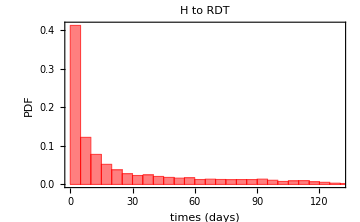
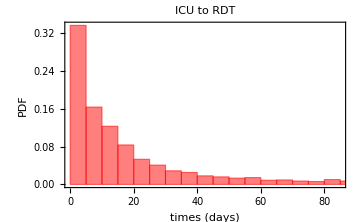

```mathematica
{Histogram[DeleteCases[timesOutcomes[[All,{1,3}]]//Flatten,"NA"],Automatic,"Probability",PlotLabel->"H to RDT"],Histogram[DeleteCases[timesOutcomes[[All,{2,4}]]//Flatten,"NA"],Automatic,"Probability",PlotLabel->"ICU to RDT"]}
```

```mathematica
HistogramList[timesOutcomes[[All,{1,3}]]//Flatten,Automatic,"Probability"]
```

{{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330},{0.41215,0.122083,0.0778776,0.0522024,0.0375037,0.0276363,0.0230905,0.0244805,0.0206868,0.0182306,0.0165742,0.017193,0.012652,0.0138991,0.0127852,0.0122188,0.0125663,0.0125092,0.0140038,0.011005,0.00776349,0.0090106,0.00961035,0.0067163,0.00564055,0.00351761,0.00228954,0.00168026,0.000947231,0.000628314,0.000637834,0.000199918,4.75996×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.75996×10^-6}}

```mathematica
(**********************************mejor usamos Boxplots)
```

```mathematica
(*{timesHoutcomeRDT,timesICUoutcomeRDT,times2HoutcomeRDT,times2ICUoutcomeRDT}*)
```

```mathematica
(* {outcomeHR,outcomeHD,outcomeHT,outcomeICUR,outcomeICUD,outcomeICUT,outcome2HR,outcome2HD,outcome2HT,outcome2ICUR,outcome2ICUD,outcome2ICUT} *)
```

```mathematica
HRDT=timesOutcomes[[All,{1,3}]]//Flatten; (* Estos y ICURDT tienen muchos datos porque hay casos que tiene dos estancias en el hospital*)
ICURDT=timesOutcomes[[All,{2,4}]]//Flatten;
H1RDT=timesOutcomes[[All,1]];
H1R=Transpose[{timesOutcomes,outcomesAll[[All,1]]}]/.{{{x_,__},1(*los que tienen outcomeHR:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
H1D=Transpose[{timesOutcomes,outcomesAll[[All,2]]}]/.{{{x_,__},1(*los que tienen outcomeHD:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
H1T=Transpose[{timesOutcomes,outcomesAll[[All,3]]}]/.{{{x_,__},1(*los que tienen outcomeHT:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU1RDT=timesOutcomes[[All,2]];
ICU1R=Transpose[{timesOutcomes,outcomesAll[[All,4]]}]/.{{{_,x_,__},1(*los que tienen outcomeICUR:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU1D=Transpose[{timesOutcomes,outcomesAll[[All,5]]}]/.{{{_,x_,__},1(*los que tienen outcomeICUD:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU1T=Transpose[{timesOutcomes,outcomesAll[[All,6]]}]/.{{{_,x_,__},1(*los que tienen outcomeICUT:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
H2RDT=timesOutcomes[[All,3]];
H2R=Transpose[{timesOutcomes,outcomesAll[[All,7]]}]/.{{{__,x_,_},1(*los que tienen outcomeHR:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
H2D=Transpose[{timesOutcomes,outcomesAll[[All,8]]}]/.{{{__,x_,_},1(*los que tienen outcomeHD:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
H2T=Transpose[{timesOutcomes,outcomesAll[[All,9]]}]/.{{{__,x_,_},1(*los que tienen outcomeHT:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU2RDT=timesOutcomes[[All,4]];ICU2R=Transpose[{timesOutcomes,outcomesAll[[All,10]]}]/.{{{__,x_},1(*los que tienen outcomeICU2R:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU2D=Transpose[{timesOutcomes,outcomesAll[[All,11]]}]/.{{{__,x_},1(*los que tienen outcomeICU2D:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
ICU2T=Transpose[{timesOutcomes,outcomesAll[[All,12]]}]/.{{{__,x_},1(*los que tienen outcomeICU2T:1*)}->x,{_,y_}/;MatchQ[y,0]||MatchQ[y,"NA"]->"NA"};
```

```mathematica
(**************************************************probando que estan bien los tiempos por estado de la ruta*)
```

```mathematica
rulesPath
```

{{H,R}→1,{H,D}→2,{ICU,R}→3,{ICU,D}→4,{H,ICU,R}→5,{ICU,H,R}→6,{H,ICU,D}→7,{H,ICU,H,R}→8,{ICU,H,ICU,R}→9,{ICU,H,D}→10,{H,ICU,H,D}→11,{ICU,H,ICU,D}→12}

```mathematica
Position[columnaPath,9][[10;;12]]
```

{{2529},{2964},{2985}}

```mathematica
Part[#,{2529,2964,2985}]&/@{H1R,H1D,H1T,ICU1R,ICU1D,ICU1T,H2R,H2D,H2T,ICU2R,ICU2D,ICU2T} (*los pacientes tienen el tiempo que corresponde a cada estado de la ruta 9*)
```

{{NA,NA,NA},{NA,NA,NA},{1,1,1},{NA,NA,NA},{NA,NA,NA},{6,3,3},{NA,NA,NA},{NA,NA,NA},{NA,NA,NA},{3,3,37},{NA,NA,NA},{NA,NA,NA}}

```mathematica
timesOutcomes[[{2529,2964,2985}]]
```

{{1,6,NA,3},{1,3,NA,3},{1,3,NA,37}}

```mathematica
H1T[[Position[columnaPath,9]//Flatten]]//Tally(*La mayoria de los pacientes con la ruta 9 duran 1 dia en ICU ??? *)
```

{{1,107},{NA,329},{8,9},{6,5},{24,4},{9,5},{5,30},{3,60},{19,6},{12,9},{10,6},{2,51},{21,1},{13,4},{11,1},{39,1},{29,1},{4,18},{18,2},{7,4},{15,1},{38,1},{16,2},{20,1}}

{{1,107},{8,9},{6,5},{24,4},{9,5},{5,30},{3,60},{19,6},{12,9},{10,6},{2,51},{21,1},{13,4},{11,1},{39,1},{29,1},{4,18},{18,2},{7,4},{15,1},{38,1},{16,2},{20,1}}

```mathematica
(**********************************************se quita H2T y ICU2T porque desde H2 o ICU2 solo se R o D*)
```

```mathematica
all=DeleteCases[#,"NA"]&/@{HRDT,H1RDT,H1R,H1D,H1T,H2RDT,H2R,H2D,ICURDT,ICU1RDT,ICU1R,ICU1D,ICU1T,ICU2RDT,ICU2R,ICU2D} ;
```

```mathematica
H2T//Tally
```

{{NA,245371}}

```mathematica
plot1=BoxWhiskerChart[Reverse[all],"Outliers",BarOrigin->Left,ChartLabels->Reverse[{"H,RDT","H1,RDT","H1,R","H1,D","H1,T","H2,RD","H2,R","H2,D","ICU,RDT","ICU1,RDT","ICU1,R","ICU1,D","ICU1,T","ICU2,RD","ICU2,R","ICU2,D"}] ,ChartStyle->Opacity[0.5,Red]];
```

```mathematica
(**********************************************Truncando****)
```

```mathematica
Quantile[DeleteCases[#,"NA"],0.95]&/@{HRDT,H1RDT,H1R,H1D,H1T,H2RDT,H2R,H2D,ICURDT,ICU1RDT,ICU1R,ICU1D,ICU1T,ICU2RDT,ICU2R,ICU2D} (*criterio estrecho*)
```

{99,99,106,23,30,69,71,20,81,81,95,25,86,52,52,27}

```mathematica
StandardDeviation[DeleteCases[#,"NA"]]*6.&/@{HRDT,H1RDT,H1R,H1D,H1T,H2RDT,H2R,H2D,ICURDT,ICU1RDT,ICU1R,ICU1D,ICU1T,ICU2RDT,ICU2R,ICU2D}(*criterio laxo*)
```

{194.97,195.321,210.367,51.5029,68.9367,145.414,148.696,39.2787,154.972,155.343,185.01,53.8594,159.362,103.907,112.93,61.5008}

```mathematica
{HRDTs,H1RDTs,H1Rs,H1Ds,H1Ts,H2RDTs,H2Rs,H2Ds,ICURDTs,ICU1RDTs,ICU1Rs,ICU1Ds,ICU1Ts,ICU2RDTs,ICU2Rs,ICU2Ds}=Select[DeleteCases[#,"NA"],#≤100&]&/@{HRDT,H1RDT,H1R,H1D,H1T,H2RDT,H2R,H2D,ICURDT,ICU1RDT,ICU1R,ICU1D,ICU1T,ICU2RDT,ICU2R,ICU2D};(* criterio segun estudios previos *)
```

```mathematica
Length/@{HRDT,H1RDT,H1R,H1D,H1T,H2RDT,H2R,H2D,ICURDT,ICU1RDT,ICU1R,ICU1D,ICU1T,ICU2RDT,ICU2R,ICU2D}
```

{490742,245371,245371,245371,245371,245371,245371,245371,490742,245371,245371,245371,245371,245371,245371,245371}

```mathematica
l=ToString/@Length/@{HRDTs,H1RDTs,H1Rs,H1Ds,H1Ts,H2RDTs,H2Rs,H2Ds,ICURDTs,ICU1RDTs,ICU1Rs,ICU1Ds,ICU1Ts,ICU2RDTs,ICU2Rs,ICU2Ds}
```

{200313,198502,155349,32949,10204,1811,1698,113,45007,44574,22330,16500,5744,433,328,105}

```mathematica
plot2=BoxWhiskerChart[Reverse[{HRDTs,H1RDTs,H1Rs,H1Ds,H1Ts,H2RDTs,H2Rs,H2Ds,ICURDTs,ICU1RDTs,ICU1Rs,ICU1Ds,ICU1Ts,ICU2RDTs,ICU2Rs,ICU2D}],"Outliers",BarOrigin->Left,ChartLabels->Reverse[{"H,RDT"<>l[[1]],"H1,RDT"<>l[[2]],"H1,R"<>l[[3]],"H1,D"<>l[[4]],"H1,T"<>l[[5]],"H2,RD"<>l[[6]],"H2,R"<>l[[7]],"H2,D"<>l[[8]],"ICU,RDT"<>l[[9]],"ICU1,RDT"<>l[[10]],"ICU1,R"<>l[[11]],"ICU1,D"<>l[[12]],"ICU1,T"<>l[[13]],"ICU2,RD"<>l[[14]],"ICU2,R"<>l[[15]],"ICU2,D"<>l[[16]]}],ChartStyle->Opacity[0.5,Red]];
```

```mathematica
plot3=BoxWhiskerChart[Reverse[{HRDTs,H1RDTs,H1Rs,H1Ds,H1Ts,H2RDTs,H2Rs,H2Ds,ICURDTs,ICU1RDTs,ICU1Rs,ICU1Ds,ICU1Ts,ICU2RDTs,ICU2Rs,ICU2D}],{{"MeanMarker",1}},BarOrigin->Left,ChartLabels->Reverse[{"H,RDT"<>l[[1]],"H1,RDT"<>l[[2]],"H1,R"<>l[[3]],"H1,D"<>l[[4]],"H1,T"<>l[[5]],"H2,RD"<>l[[6]],"H2,R"<>l[[7]],"H2,D"<>l[[8]],"ICU,RDT"<>l[[9]],"ICU1,RDT"<>l[[10]],"ICU1,R"<>l[[11]],"ICU1,D"<>l[[12]],"ICU1,T"<>l[[13]],"ICU2,RD"<>l[[14]],"ICU2,R"<>l[[15]],"ICU2,D"<>l[[16]]}],ChartStyle->Opacity[0.5,Red]];
```

```mathematica
Export["/home/lina/Documents/datos_INS/timesStatesBP"<>#[[1]]<>".pdf",#[[2]]]&/@{{"1",plot1},{"2",plot2},{"3",plot3}}
```

{/home/lina/Documents/datos_INS/timesStatesBP1.pdf,/home/lina/Documents/datos_INS/timesStatesBP2.pdf,/home/lina/Documents/datos_INS/timesStatesBP3.pdf}

```mathematica
Export["/home/lina/Documents/datos_INS/timesStatesBP"<>#[[1]]<>".png",#[[2]]]&/@{{"1",plot1},{"2",plot2},{"3",plot3}}
```

{/home/lina/Documents/datos_INS/timesStatesBP1.png,/home/lina/Documents/datos_INS/timesStatesBP2.png,/home/lina/Documents/datos_INS/timesStatesBP3.png}

### Building the database

```mathematica
dataBase6=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis6.csv"];
```

```mathematica
dataBase6[[1;;3]]//Grid
```

ID | ageYears | ageG | Gender | IMP_M_2018 | IMP_D_2019 | IMP_D_2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | 26_50 | M | 12.3 | 10.8 | 11.1 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0
2 | 85 | 75_ | F | 19.9 | 19.9 | 19.9 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

```mathematica
dataBase6[[1]]//Length
```

26

```mathematica
Count[dataBase6[[2;;,11]],"NA"]
```

37115

```mathematica
(******************eliminando como NA los tiempos mayores a 100 días*)
```

```mathematica
dataBase7={dataBase6[[1]],Sequence@@Table[MapAt[(If[#>100,"NA",#]/.If["NA">100,"NA","NA"]->"NA")&,dataBase6[[i]],{{11},{15},{19},{23}}],{i,2,Length[dataBase6]}]};
```

```mathematica
Count[dataBase7[[2;;,11]],"NA"]
```

46869

```mathematica
46869-9754
```

37115

```mathematica
dataBase7[[1;;3]]//Grid
```

ID | ageYears | ageG | Gender | IMP_M_2018 | IMP_D_2019 | IMP_D_2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | 26_50 | M | 12.3 | 10.8 | 11.1 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0
2 | 85 | 75_ | F | 19.9 | 19.9 | 19.9 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

```mathematica
(*comprobar que esta bien comparando con el plot2 o 3*)
```

```mathematica
Length[DeleteCases[dataBase7[[2;;,#]],"NA"]]&/@{11,15,19,23}
```

{198502,44574,1811,433}

```mathematica
Length/@{H1RDTs,ICU1RDTs,H2RDTs,ICU2RDTs}
```

{198502,44574,1811,433}

### Adding new Columns

```mathematica
dataBase7=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis7.csv"];
```

```mathematica
dataBase7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
dataBase7[[1]]//PositionIndex
```

<|ID→{1},ageYears→{2},ageG→{3},Gender→{4},IMP_M_2018→{5},IMP_D_2019→{6},IMP_D_2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26}|>

```mathematica
Count[dataBase7[[2;;,3]],"NA"]
```

2688

```mathematica
(****************************************************************** creando columnas para diferenciar tiempos por ruta*)
```

```mathematica
(* BPHR - 1:{"H","R"}-1 / 2:{"ICU","H","R"}-6 / "C": otros
BPHD - 1:{"H","D"}-2 / 2:{"ICU","H","D"}-10 / "C": otros
BPHT - 1:{"H","ICU","R"}-5/ 2: {"H","ICU","D"}-7/ 3: {"H","ICU","H","D"}-11/ 4:{"H","ICU","H","R"}-8/ 5:{"ICU","H","ICU","D"}-12/ 6:{"ICU","H","ICU","R"}-9 / "C": otros
BPICUR - 1:{"ICU","R"}-3 / 2:{"H","ICU","R"}-5 / "C": otros
BPICUD - 1:{"ICU","D"}-4 / 2:{"H","ICU","D"}-7 / "C": otros 
BPICUT - 1:{"ICU","H","R"}-6 / 2:{"ICU","H","D"}-10 / 3: {"H","ICU","H","D"}-11/ 4:{"H","ICU","H","R"}-8/ 5:{"ICU","H","ICU","D"}-12/ 6:{"ICU","H","ICU","R"}-9 / "C": otros
  NOTA: Los números deben ir como Strings
NOTA: "C" son datos censurados por su decenlace no es el evaluado pero no  se ponen como "NA" porque no se pueden eliminar del análisis porque sus tiempos aportan información al modelo como dato censurado. Las demas rutas cuyos tiempos no aportan también se ponen asi porque ya se eliminaran al tener "NA" en el tiempo
NOTA: La columna BedPathway tiene NA que son casos que no pertenecen a ninguna ruta *)
```

```mathematica
Length[DeleteCases[dataBase7[[2;;,#]],"NA"]]&/@{11,15,19,23}
```

```mathematica
{{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12}//Sort
```

```mathematica
BPHR=dataBase7[[2;;,9]]/.{1->"1",6->"2",x_/;x!=1&&x!=6&&x!="NA"->"C"}
```

{1,1,1,1,1,1,1,1,C,1,1,C,1,1,1,NA,C,C,C,C,C,2,1,NA,C,C,C,C,1,1,NA,1,2,1,C,1,1,1,1,NA,2,C,1,1,C,1,1,1,1,C,1,C,C,C,C,C,C,1,C,2,1,1,1,1,1,1,1,C,1,1,1,C,NA,1,1,2,NA,1,1,1,1,C,1,1,NA,1,1,C,1,C,1,1,C,1,C,2,C,C,C,1,1,1,C,NA,1,1,1,C,1,NA,245151,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,1,1,C,C,C,C,C,1,1,C,1,C,C,C,C,C,1,C,1,C,C,C,C,C,C,C,1,C,C,C,C,1,C,C,C,C,C,C,C,1,C,C,C,C,C,C,1,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,1,1,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C}
 |  |  |  |

```mathematica
%//DeleteDuplicates
```

{1,C,NA,2}

```mathematica
BPHR=dataBase7[[2;;,9]]/.{1->"1",6->"2",x_/;x!=1&&x!=6&&x!="NA"->"C"};BPHD=dataBase7[[2;;,9]]/.{2->"1",10->"2",x_/;x!=2&&x!=10&&x!="NA"->"C"};
BPHT=dataBase7[[2;;,9]]/.{5->"1",7->"2",11->"3",8->"4",12->"5",9->"6",x_/;x!=5&&x!=7&&x!=11&&x!=8&&x!=12&&x!=9&&x!="NA"->"C"};
BPICUR=dataBase7[[2;;,9]]/.{3->"1",5->"2",x_/;x!=3&&x!=5&&x!="NA"->"C"};
BPICUD=dataBase7[[2;;,9]]/.{4->"1",7->"2",x_/;x!=4&&x!=7&&x!="NA"->"C"};
BPICUT=dataBase7[[2;;,9]]/.{6->"1",10->"2",11->"3",8->"4",12->"5",9->"6",x_/;x!=6&&x!=10&&x!=11&&x!=8&&x!=12&&x!=9&&x!="NA"->"C"};
```

```mathematica
dataBase7[[1]]
```

{ID,ageYears,ageG,Gender,IMP_M_2018,IMP_D_2019,IMP_D_2020,Vaccination,BedPathway,timesBP,timeHOutcomeRDT,outcomeHR,outcomeHD,outcomeHT,timeICUOutcomeRDT,outcomeICUR,outcomeICUD,outcomeICUT,time2HOutcomeRDT,outcome2HR,outcome2HD,outcome2HT,time2ICUOutcomeRDT,outcome2ICUR,outcome2ICUD,outcome2ICUT}

```mathematica
dataBaseN={{"ID","AgeYears","AgeG","Gender","IPMM2018","IPMD2019","IPMD2020","Vaccination","BedPathway","timesBP","timeHOutcomeRDT","outcomeHR","outcomeHD","outcomeHT","timeICUOutcomeRDT","outcomeICUR","outcomeICUD","outcomeICUT","time2HOutcomeRDT","outcome2HR","outcome2HD","outcome2HT","time2ICUOutcomeRDT","outcome2ICUR","outcome2ICUD","outcome2ICUT","BPHR","BPHD","BPHT","BPICUR","BPICUD","BPICUT"},Sequence@@Map[Flatten,Transpose[{dataBase7[[2;;,1;;26]],BPHR,BPHD,BPHT,BPICUR,BPICUD,BPICUT}]]};
```

```mathematica
(*****************************************)
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis7.csv",dataBaseN];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis7.csv",dataBaseN];
```

```mathematica
(************************** WHAT IS WRONG WITH VACCINATION *)
```

```mathematica
data5=Import["/home/lina/Documents/unCover/uncoverP1LoS/dataBaseAnalysis5.csv"];
```

```mathematica
data5[[1;;2]]//Grid
```

ID | AgeYears | Gender | YearAdmission | Vaccination | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | outComeFromH | outComeFromICU | outComeFromAll
1 | 34 | M | 2020 | No | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA | HR | NA | HR

```mathematica
data7=Import["/home/lina/Documents/unCover/uncoverP1LoS_2/dataBaseAnalysis7.csv"];
```

```mathematica
data7[[1;;2]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
1 | 34 | 26_50 | M | 12.3 | 10.8 | 11.1 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | 1 | C | C | C | C | C

```mathematica
Count[data5[[All,5]],"No"]
```

60974

```mathematica
Count[data5[[All,5]],"Yes"]
```

58518

```mathematica
Count[data7[[All,8]],"No"]
```

182243

```mathematica
Count[data7[[All,8]],"Yes"]
```

63128

```mathematica
#[[{2,-1}]]&/@{data5,data7}
```

{{{1,34,M,2020,No,1,8,1,0,0,NA,NA,NA,NA,HR,NA,HR},{119492,85,M,2021,Yes,14,1,0,1,0,NA,NA,NA,NA,HD,NA,HD}},{{1,34,26_50,M,12.3,10.8,11.1,No,1,1,8,1,0,0,NA,0,0,0,NA,0,0,0,NA,0,0,0,1,C,C,C,C,C},{245375,85,75_,M,11.9,10.8,11.1,Yes,2,1,1,0,1,0,NA,0,0,0,NA,0,0,0,NA,0,0,0,C,1,C,C,C,C}}}

```mathematica
d5=data5[[2;;,{2,3,5}]];
d7=data7[[2;;,{2,4,8}]];
```

```mathematica
Length[d7]-Length[d5]
```

125879

```mathematica
#[[10]]&/@{d5,d7}
```

{{31,M,No},{21,M,No}}

```mathematica
Complement[d7,d5];
```

```mathematica
%//Length
```

7

```mathematica
(*data5 and 7 are very different *)
```

```mathematica
(*************************poner NAs a los tiempos 0*)
```

```mathematica
data7=Import["/home/lina/Documents/UnCover/uncoverP1LoS/dataBaseAnalysis7.csv"];
```

```mathematica
data7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
Count[data7[[All,11]],0]
```

0

```mathematica
Count[data7[[All,15]],0]
```

0

```mathematica
Count[data7[[All,19]],0]
```

0

```mathematica
Count[data7[[23]],0]
```

10

```mathematica
Select[data7,#[[11]]===0&]
```

{}

```mathematica
(************************************Mejorando las covariables de las BP. ESTAS COVARIABLES ESTAN HECHAS SOLO PARA AJUSTAR LOS TIEMPO "timeHOutcomeRDT"  "timeICUOutcomeRDT"*)
```

```mathematica
BPHR=(data7[[All,{11,27}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
data7[[All,{11,27}]]/.x_/;IntegerQ[x]->w;
```

```mathematica
%//Tally
```

{{{timeHOutcomeRDT,BPHR},1},{{w,w},155349},{{w,C},43153},{{NA,NA},37130},{{NA,w},9739}}

```mathematica
Count[BPHR,"NA"]
```

46869

```mathematica
Count[data7[[All,27]],"NA"]
```

5230

```mathematica
BPHD=(data7[[All,{11,28}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
Count[BPHD,"NA"]
```

46860

```mathematica
Count[data7[[All,28]],"NA"]
```

5230

```mathematica
BPHT=(data7[[All,{11,29}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
Count[BPHT,"NA"]
```

46869

```mathematica
Count[data7[[All,29]],"NA"]
```

5230

```mathematica
BPICUR=(data7[[All,{15,30}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
Count[BPICUR,"NA"]
```

200797

```mathematica
Count[data7[[All,30]],"NA"]
```

5230

```mathematica
BPICUD=(data7[[All,{15,31}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
Count[BPICUD,"NA"]
```

200797

```mathematica
Count[data7[[All,31]],"NA"]
```

5230

```mathematica
BPICUT=(data7[[All,{15,32}]]/.{{"NA","C"}->{"NA","NA"},{"NA",_}->{"NA","NA"}})[[All,2]];
```

```mathematica
Count[BPICUT,"NA"]
```

200797

```mathematica
Count[data7[[All,32]],"NA"]
```

5230

```mathematica
BPHR[[1]]
```

BPHR

```mathematica
data8=Flatten/@Transpose[{data7[[All,1;;26]],BPHR,BPHD,BPHT,BPICUR,BPICUD,BPICUT}];
```

```mathematica
data8[[1;;3]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
1 | 34 | 26_50 | M | 12.3 | 10.8 | 11.1 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | 1 | C | C | NA | NA | NA
2 | 85 | 75_ | F | 19.9 | 19.9 | 19.9 | No | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | 1 | C | C | NA | NA | NA

```mathematica
{w,e,{3,d},3}/.x_/;IntegerQ[x]->w
```

{w,e,{w,d},w}

```mathematica
Integer
```

```mathematica
(*****************************************)
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis7.csv",data8];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBaseAnalysis7.csv",data8];
```

```mathematica
BPHD=data7[[All,28]]/."C"->"NA";
```

```mathematica
data9=Flatten/@Transpose[{data7[[All,1;;26]],BPHR,BPHD,BPHT,BPICUR,BPICUD,BPICUT}];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBaseAnalysisP.csv",data9];
```

```mathematica
(*EL PROBLEMA NO SE SOLUCIONA CON ESTO PORQUE LO QUE PASA ES QUE HAY GRUPOS DONDE NO OCURRE EL EVENTO DE INTERES, SIN EMBARGO, NO HAY UNA BUENA FORMA DE CREAR LAS CATEGORIAS DE CADA VARIABLE BP DE TAL MANERA QUE AL MENOS UN CASO TENGA EL EVENTO. ASI QUE SE VOLCIÓ A CREAR LA dataBaseAnalysis7.csv COMO SE TENIA INICIALMENTE Y SE RECURRIÓ AL MODELO COX DE MULTIPLES ESTADOS. ADEMAS LOS AFTs AJUSTANDO POR ESTAS VARIABLES DUMMIES OF BP TAMBIEN DAN MALOS RESULTADOS*)
```

## DataBase 8

This database is for the multi-state cox model. Using the last follow-up as the last event or transition but not as the last global follow-up

```mathematica
dataBase7=Import["/home/lina/Documents/unCoVer/processingDataINS_git/dataOutput/dataBaseAnalysis7.csv"];
```

```mathematica
dataBase7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
dataBase7[[All,28]]//Tally
```

{{BPHD,1},{C,207183},{NA,5230},{1,32714},{2,244}}

```mathematica
(***************************)
```

```mathematica
bp={{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12};
```

```mathematica
dataBase7[[All,9]]//Tally//Sort
```

{{1,161773},{2,32714},{3,18646},{4,13239},{5,4683},{6,3315},{7,3263},{8,1717},{9,329},{10,244},{11,113},{12,105},{BedPathway,1},{NA,5230}}

```mathematica
dataFromH=Select[dataBase7,(#[[9]]=="BedPathway"||#[[9]]==1||#[[9]]==2||#[[9]]==5||#[[9]]==7||#[[9]]==8||#[[9]]==11)&&#[[11]]!="NA"&];
```

```mathematica
dataFromH[[All,9]]//Tally//Sort
```

{{1,152081},{2,32705},{5,4677},{7,3263},{8,1717},{11,113},{BedPathway,1}}

```mathematica
dataFromH[[All,{9,11,15,19}]][[1]] (*these are the times in each state, they are not accumulate *)
```

{BedPathway,timeHOutcomeRDT,timeICUOutcomeRDT,time2HOutcomeRDT}

```mathematica
tiemposStatusCols=dataFromH[[All,{9,11,15,19}]]/.{{1,x_,y_,z_}->{x,0,x,0,x,1,x,0},{2,x_,y_,z_}->{x,0,x,0,x,0,x,1},{5,x_,y_,z_}->{x,1,x,0,y+x,1,y+x,0},{7,x_,y_,z_}->{x,1,x,0,x,0,y+x,1},{8,x_,y_,z_}->{x,1,y+x,1,z+y+x,1,z+y+x,0},{11,x_,y_,z_}->{x,1,y+x,1,y+x,0,z+y+x,1}}; (*Here we made the accumulate of times since the start-admissionH*)
```

```mathematica
(*******************vrificando que no haya NAs*)
```

```mathematica
tiemposStatusCols[[All,1]]//DeleteDuplicates
```

{BedPathway,8,10,3,11,1,4,6,7,18,5,2,14,15,17,9,23,19,12,24,13,42,83,29,22,26,20,30,81,50,79,28,16,77,25,21,33,40,89,27,61,72,71,97,70,69,41,38,63,36,35,98,85,34,45,32,99,65,87,86,52,84,80,51,49,48,47,46,76,37,43,44,31,39,66,100,62,92,74,73,91,60,90,59,55,57,88,56,82,58,95,68,94,54,93,67,75,53,78,64,96}

```mathematica
tiemposStatusCols[[All,3]]//DeleteDuplicates
```

{timeICUOutcomeRDT,8,10,3,11,1,4,6,7,18,5,2,14,15,17,23,19,9,12,21,24,13,42,83,29,22,26,20,30,81,50,53,79,28,16,37,77,25,33,57,40,89,27,47,41,61,72,71,97,70,69,38,63,36,35,98,85,34,73,45,32,99,65,87,86,52,84,80,51,49,48,46,76,43,44,31,39,66,100,62,92,74,91,60,90,59,55,88,56,82,58,95,68,94,54,93,67,75,78,64,96,3+NA,108,10+NA,102,104,9+NA,110,7+NA,6+NA,101,106,103}

```mathematica
Position[tiemposStatusCols[[All,3]],"NA"]
```

{{155673,2},{156588,2},{157131,2},{157535,2},{157544,2},{158301,2},{158340,2}}

```mathematica
dataFromH[[{1,155673}]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
190128 | 55 | 51_65 | F | 9.5 | 15.7 | 14.9 | Yes | 8 | 3 | 3 | 0 | 0 | 1 | NA | 0 | 0 | 1 | 1 | 1 | 0 | 0 | NA | 0 | 0 | 0 | C | C | 4 | NA | NA | NA

```mathematica
Position[tiemposStatusCols,{___,"NA",___}]
```

{}

```mathematica
(********************)
```

```mathematica
Select[dataFromH[[All,{9,11,15,19}]],#[[1]]==8&][[1]]
```

{8,3,7,5}

```mathematica
Position[dataFromH[[All,{9,11,15,19}]],{8,__}][[1]]
```

{45}

```mathematica
tiemposStatusCols[[1]]
```

{BedPathway,timeHOutcomeRDT,timeICUOutcomeRDT,time2HOutcomeRDT}

```mathematica
tiemposStatusCols[[45]]
```

{3,1,10,1,15,1,15,0}

```mathematica
dataFromH[[{1,45}]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
55 | 63 | 51_65 | F | 24.4 | 24.4 | 24.4 | No | 8 | 3 | 3 | 0 | 0 | 1 | 7 | 0 | 0 | 1 | 5 | 1 | 0 | 0 | NA | 0 | 0 | 0 | C | C | 4 | C | C | 4

```mathematica
(***************+++deleting positions con NAs*)
```

```mathematica
pNAs=Position[tiemposStatusCols,{___,_+"NA",___}]
```

{{93},{943},{944},{1362},{105694},{112710},{114392},{116160},{118292},{118303},{118429},{118505},{118511},{118575},{118994},{118998},{119009},{119033},{119084},{119629},{119765},{119775},{119787},{119824},{119830},{119902},{120193},{120341},{120584},{121042},{121281},{121430},{124329},{124552},{125143},{125305},{125717},{125762},{126284},{126299},{126436},{127674},{128097},{129661},{129667},{129676},{129701},{129772},{129774},{130074},{130754},{130895},{131086},{131310},{131336},{131583},{131587},{131621},{132111},{132121},{132710},{132832},{132847},{132976},{133449},{133521},{133550},{133874},{134152},{134731},{134733},{134821},{135213},{136072},{136087},{136556},{136593},{137566},{137572},{137628},{137987},{138094},{139911},{140684},{140849},{141676},{142194},{142195},{142217},{142766},{143111},{143501},{143557},{143560},{143583},{143801},{143823},{144253},{144448},{144499},{144504},{144819},{144852},{144855},{145055},{145081},{145118},{145158},{145341},{145443},{145798},{145846},{145913},{145928},{146258},{146265},{146607},{146680},{147066},{147080},{147111},{147230},{147418},{147420},{147817},{147981},{148124},{148137},{148490},{148586},{148587},{148601},{148821},{148884},{148894},{149117},{149237},{149397},{149444},{149471},{149669},{149691},{149980},{150059},{150093},{150212},{150214},{150361},{150362},{150398},{150420},{150885},{150889},{150915},{151059},{151131},{151196},{151198},{151272},{151402},{151461},{151548},{151549},{151556},{151666},{151810},{151816},{151861},{151884},{152473},{152638},{152689},{152693},{152797},{152946},{152960},{153050},{153325},{153331},{153332},{153333},{153334},{153335},{153336},{153442},{153464},{153494},{153537},{153543},{153544},{153546},{153548},{153566},{153631},{153793},{153867},{154184},{154331},{154467},{154586},{155673},{156588},{157131},{157535},{157544},{158301},{158340}}

```mathematica
(********************************************)
```

```mathematica
dataBase8={{Sequence@@dataBase7[[1,{1,2,3,4,8,9}]],"tHtoICU","sHtoICU","tICUto2H","sICUto2H","tRecovery","sRecovery","tDeceased","sDeceased"},Sequence@@Map[Flatten,Transpose[{dataFromH[[2;;,{1,2,3,4,8,9}]],tiemposStatusCols[[2;;]]}]]};
```

```mathematica
dataBase8n=Delete[dataBase8,pNAs];
```

```mathematica
dataBase8[[1;;2]]//Grid
```

ID | AgeYears | AgeG | Gender | Vaccination | BedPathway | tHtoICU | sHtoICU | tICUto2H | sICUto2H | tRecovery | sRecovery | tDeceased | sDeceased
1 | 34 | 26_50 | M | No | 1 | 8 | 0 | 8 | 0 | 8 | 1 | 8 | 0

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis8.csv",dataBase8n];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis8.csv",dataBase8n];
```

```mathematica
(dataBase8n[[2;;,#]]//DeleteDuplicates)&/@{7,8,9,10,11,12,13,14}
```

{{8,10,3,11,1,4,6,7,18,5,2,14,15,17,9,23,19,12,24,13,42,83,29,22,26,20,30,81,50,79,28,16,77,25,21,33,40,89,27,61,72,71,97,70,69,41,38,63,36,35,98,85,34,45,32,99,65,87,86,52,84,80,51,49,48,47,46,76,37,43,44,31,39,66,100,62,92,74,73,91,60,90,59,55,57,88,56,82,58,95,68,94,54,93,67,75,53,78,64,96},{0,1},{8,10,3,11,1,4,6,7,18,5,2,14,15,17,23,19,9,12,21,24,13,42,83,29,22,26,20,30,81,50,53,79,28,16,37,77,25,33,57,40,89,27,47,41,61,72,71,97,70,69,38,63,36,35,98,85,34,73,45,32,99,65,87,86,52,84,80,51,49,48,46,76,43,44,31,39,66,100,62,92,74,91,60,90,59,55,88,56,82,58,95,68,94,54,93,67,75,78,64,96,108,102,104,110,101,106,103},{0,1},{8,10,3,11,13,1,4,25,6,7,12,18,16,2,14,15,17,5,23,30,19,9,22,35,24,42,83,29,26,20,81,54,50,34,62,79,33,28,47,77,21,76,48,49,75,32,40,89,27,58,31,61,72,44,71,97,70,69,41,38,63,46,37,36,98,85,45,99,65,87,88,86,52,84,51,80,119,82,96,43,39,66,100,95,92,60,94,74,73,91,90,59,55,57,56,68,93,67,53,78,64,101,129,133,110,105,116,115,117,107,108,109,104,120,103,114,112,113,118,111,106,102,123,121,122,124,143},{1,0},{8,10,3,11,13,1,4,25,6,7,12,18,16,2,14,15,17,24,5,23,30,19,9,22,35,42,83,29,26,21,20,81,54,50,34,62,79,33,28,47,77,27,57,76,48,49,75,32,40,89,58,31,61,72,44,71,97,70,69,41,38,63,46,37,36,98,85,45,99,65,87,88,86,52,84,51,80,119,82,96,43,39,66,100,95,92,60,94,74,73,91,90,59,55,56,68,93,67,53,78,64,101,129,133,110,105,116,115,117,107,108,109,104,120,103,114,112,113,118,111,106,102,123,121,122,124,143},{0,1}}

```mathematica
Position[dataBase8n,{_,_,_,_,_,1,___}]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{11},{12},{14},{15},{16},{21},{25},{26},{27},{28},{30},{31},{32},{33},{35},{36},{37},{38},{39},{40},{41},{46},{47},{48},{49},{50},{51},{52},{53},{55},{56},{57},{59},{60},{61},{62},{63},{64},{66},{67},{68},{69},{71},{72},{73},{75},{77},{78},{79},{81},{82},{84},{85},{86},{88},151955,{194127},{194129},{194132},{194141},{194143},{194144},{194145},{194147},{194152},{194155},{194157},{194158},{194160},{194161},{194162},{194163},{194164},{194165},{194166},{194167},{194174},{194176},{194183},{194184},{194185},{194187},{194188},{194190},{194191},{194192},{194194},{194195},{194198},{194200},{194203},{194214},{194217},{194222},{194226},{194227},{194228},{194229},{194230},{194245},{194249},{194250},{194251},{194252},{194263},{194264},{194281},{194282},{194283},{194284},{194285},{194289},{194291},{194298},{194302},{194309},{194314},{194328},{194329}}
 |  |  |  |

## DataBase 9

This database is for the multi-state cox model. Using the last follow-up as  last global follow-up but not as the last event or transition. For models starting in the H

```mathematica
dataBase7=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis7.csv"];
```

```mathematica
dataBase7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
bp={{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12};
```

```mathematica
dataBase7[[All,9]]//Tally//Sort
```

{{1,161773},{2,32714},{3,18646},{4,13239},{5,4683},{6,3315},{7,3263},{8,1717},{9,329},{10,244},{11,113},{12,105},{BedPathway,1},{NA,5230}}

```mathematica
dataFromH=Select[dataBase7,(#[[9]]=="BedPathway"||#[[9]]==1||#[[9]]==2||#[[9]]==5||#[[9]]==7||#[[9]]==8||#[[9]]==11)&&#[[11]]!="NA"&];
```

```mathematica
dataFromH[[All,9]]//Tally//Sort
```

{{1,152081},{2,32705},{5,4677},{7,3263},{8,1717},{11,113},{BedPathway,1}}

```mathematica
dataFromH[[All,{9,11,15,19}]][[1]] (*these are the times in each state, they are not accumulate *)
```

{BedPathway,timeHOutcomeRDT,timeICUOutcomeRDT,time2HOutcomeRDT}

```mathematica
tiemposStatusCols=dataFromH[[All,{9,11,15,19}]]/.{{1,x_,y_,z_}->{x,0,x,0,x,1,x,0},{2,x_,y_,z_}->{x,0,x,0,x,0,x,1},{5,x_,y_,z_}->{x,1,y+x,0,y+x,1,y+x,0},{7,x_,y_,z_}->{x,1,y+x,0,y+x,0,y+x,1},{8,x_,y_,z_}->{x,1,y+x,1,z+y+x,1,z+y+x,0},{11,x_,y_,z_}->{x,1,y+x,1,z+y+x,0,z+y+x,1}}; (*Here we made the accumulate of times since the start-admissionH*)
```

```mathematica
(*******************vrificando que no haya NAs*)
```

```mathematica
tiemposStatusCols[[All,1]]//DeleteDuplicates
```

{BedPathway,8,10,3,11,1,4,6,7,18,5,2,14,15,17,9,23,19,12,24,13,42,83,29,22,26,20,30,81,50,79,28,16,77,25,21,33,40,89,27,61,72,71,97,70,69,41,38,63,36,35,98,85,34,45,32,99,65,87,86,52,84,80,51,49,48,47,46,76,37,43,44,31,39,66,100,62,92,74,73,91,60,90,59,55,57,88,56,82,58,95,68,94,54,93,67,75,53,78,64,96}

```mathematica
tiemposStatusCols[[All,3]]//DeleteDuplicates
```

{timeICUOutcomeRDT,8,10,3,11,13,1,4,25,6,7,12,18,16,2,14,15,17,24,5,23,30,19,9,21,3+NA,42,83,29,22,26,20,81,54,50,34,53,79,28,37,77,27,57,33,48,49,32,40,89,47,31,41,61,72,71,97,70,69,38,63,46,36,35,98,85,73,45,99,65,87,88,86,52,84,80,51,119,76,43,44,39,66,100,95,62,92,60,94,74,91,90,59,55,56,82,58,68,93,67,75,78,64,101,96,12+NA,1+NA,117,13+NA,17+NA,104,14+NA,10+NA,6+NA,118,8+NA,7+NA,9+NA,111,109,116,114,5+NA,112,113,4+NA,107,105,110,106,108,11+NA,2+NA,123,121,19+NA,122,16+NA,15+NA,103,102,27+NA,25+NA,36+NA,23+NA,22+NA,20+NA,21+NA,18+NA,143,24+NA}

```mathematica
Position[tiemposStatusCols[[All,3]],"NA"]
```

{{93,2},{114392,2},{116160,2},{118292,2},{118303,2},{118429,2},{118505,2},{118511,2},{118575,2},{118994,2},{118998,2},{119009,2},{119033,2},{119084,2},{119629,2},{119765,2},{119775,2},{119787,2},{119824,2},{119830,2},{119902,2},{120193,2},{120341,2},{120584,2},{121042,2},{121281,2},{121430,2},{124329,2},{124552,2},{125143,2},{125305,2},{125717,2},{125762,2},{126284,2},{126299,2},{126436,2},{127674,2},{128097,2},{129661,2},{129667,2},{129676,2},{129701,2},{129772,2},{129774,2},{130074,2},{130754,2},{130895,2},{131086,2},{131310,2},{131336,2},{131583,2},{131587,2},{131621,2},{132111,2},{132710,2},{132847,2},{132976,2},{133449,2},{133521,2},{133550,2},{133874,2},{134152,2},{134731,2},{134733,2},{134821,2},{135213,2},{136556,2},{136593,2},{137566,2},{137572,2},{139911,2},{140684,2},{140849,2},{141676,2},{142194,2},{142195,2},{142217,2},{142766,2},{143111,2},{143501,2},{143557,2},{143560,2},{143583,2},{143801,2},{143823,2},{144253,2},{144448,2},{144499,2},{144504,2},{144819,2},{144852,2},{144855,2},{145055,2},{145081,2},{145118,2},{145158,2},{145341,2},{145443,2},{145913,2},{145928,2},{146258,2},{146265,2},{146607,2},{146680,2},{147066,2},{147080,2},{147230,2},{147418,2},{147420,2},{147817,2},{147981,2},{148124,2},{148137,2},{148490,2},{148586,2},{148587,2},{148601,2},{148821,2},{148884,2},{148894,2},{149117,2},{149237,2},{149397,2},{149444,2},{149471,2},{149669,2},{149691,2},{149980,2},{150059,2},{150093,2},{150361,2},{150362,2},{150398,2},{150420,2},{150885,2},{150889,2},{150915,2},{151059,2},{151131,2},{151196,2},{151198,2},{151272,2},{151402,2},{151461,2},{151548,2},{151549,2},{151556,2},{151666,2},{151810,2},{151816,2},{151861,2},{152473,2},{152638,2},{152689,2},{152693,2},{152797,2},{152946,2},{152960,2},{153050,2},{153325,2},{153331,2},{153332,2},{153333,2},{153334,2},{153335,2},{153336,2},{153442,2},{153494,2},{153537,2},{153543,2},{153544,2},{153546,2},{153548,2},{153566,2},{153631,2},{153793,2},{153867,2},{154184,2},{154331,2},{154467,2},{154586,2},{155673,2},{156588,2},{157131,2},{157535,2},{157544,2},{158301,2},{158340,2}}

```mathematica
dataFromH[[{1,155673}]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
190128 | 55 | 51_65 | F | 9.5 | 15.7 | 14.9 | Yes | 8 | 3 | 3 | 0 | 0 | 1 | NA | 0 | 0 | 1 | 1 | 1 | 0 | 0 | NA | 0 | 0 | 0 | C | C | 4 | C | C | 4

```mathematica
Position[tiemposStatusCols,{___,"NA",___}]
```

{}

```mathematica
(********************)
```

```mathematica
Select[dataFromH[[All,{9,11,15,19}]],#[[1]]==8&][[1]]
```

{8,3,7,5}

```mathematica
Position[dataFromH[[All,{9,11,15,19}]],{8,__}][[1]]
```

{45}

```mathematica
tiemposStatusCols[[1]]
```

{BedPathway,timeHOutcomeRDT,timeICUOutcomeRDT,time2HOutcomeRDT}

```mathematica
tiemposStatusCols[[45]]
```

{3,1,10,1,15,1,15,0}

```mathematica
dataFromH[[{1,45}]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
55 | 63 | 51_65 | F | 24.4 | 24.4 | 24.4 | No | 8 | 3 | 3 | 0 | 0 | 1 | 7 | 0 | 0 | 1 | 5 | 1 | 0 | 0 | NA | 0 | 0 | 0 | C | C | 4 | C | C | 4

```mathematica
(***************+++deleting positions con NAs*)
```

```mathematica
pNAs=Position[tiemposStatusCols,{___,_+"NA",___}]
```

{{93},{943},{944},{1362},{105694},{112710},{114392},{116160},{118292},{118303},{118429},{118505},{118511},{118575},{118994},{118998},{119009},{119033},{119084},{119629},{119765},{119775},{119787},{119824},{119830},{119902},{120193},{120341},{120584},{121042},{121281},{121430},{124329},{124552},{125143},{125305},{125717},{125762},{126284},{126299},{126436},{127674},{128097},{129661},{129667},{129676},{129701},{129772},{129774},{130074},{130754},{130895},{131086},{131310},{131336},{131583},{131587},{131621},{132111},{132121},{132710},{132832},{132847},{132976},{133449},{133521},{133550},{133874},{134152},{134731},{134733},{134821},{135213},{136072},{136087},{136556},{136593},{137566},{137572},{137628},{137987},{138094},{139911},{140684},{140849},{141676},{142194},{142195},{142217},{142766},{143111},{143501},{143557},{143560},{143583},{143801},{143823},{144253},{144448},{144499},{144504},{144819},{144852},{144855},{145055},{145081},{145118},{145158},{145341},{145443},{145798},{145846},{145913},{145928},{146258},{146265},{146607},{146680},{147066},{147080},{147111},{147230},{147418},{147420},{147817},{147981},{148124},{148137},{148490},{148586},{148587},{148601},{148821},{148884},{148894},{149117},{149237},{149397},{149444},{149471},{149669},{149691},{149980},{150059},{150093},{150212},{150214},{150361},{150362},{150398},{150420},{150885},{150889},{150915},{151059},{151131},{151196},{151198},{151272},{151402},{151461},{151548},{151549},{151556},{151666},{151810},{151816},{151861},{151884},{152473},{152638},{152689},{152693},{152797},{152946},{152960},{153050},{153325},{153331},{153332},{153333},{153334},{153335},{153336},{153442},{153464},{153494},{153537},{153543},{153544},{153546},{153548},{153566},{153631},{153793},{153867},{154184},{154331},{154467},{154586},{155673},{156588},{157131},{157535},{157544},{158301},{158340}}

```mathematica
(********************************************)
```

```mathematica
dataBase9={{Sequence@@dataBase7[[1,{1,2,3,4,8,9}]],"tHtoICU","sHtoICU","tICUto2H","sICUto2H","tRecovery","sRecovery","tDeceased","sDeceased"},Sequence@@Map[Flatten,Transpose[{dataFromH[[2;;,{1,2,3,4,8,9}]],tiemposStatusCols[[2;;]]}]]};
```

```mathematica
dataBase9n=Delete[dataBase9,pNAs];
```

```mathematica
dataBase8[[1;;2]]//Grid
```

ID | AgeYears | AgeG | Gender | Vaccination | BedPathway | tHtoICU | sHtoICU | tICUto2H | sICUto2H | tRecovery | sRecovery | tDeceased | sDeceased
1 | 34 | 26_50 | M | No | 1 | 8 | 0 | 8 | 0 | 8 | 1 | 8 | 0

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis9.csv",dataBase9n];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis9.csv",dataBase9n];
```

```mathematica
(dataBase8n[[2;;,#]]//DeleteDuplicates)&/@{7,8,9,10,11,12,13,14}
```

{{8,10,3,11,1,4,6,7,18,5,2,14,15,17,9,23,19,12,24,13,42,83,29,22,26,20,30,81,50,79,28,16,77,25,21,33,40,89,27,61,72,71,97,70,69,41,38,63,36,35,98,85,34,45,32,99,65,87,86,52,84,80,51,49,48,47,46,76,37,43,44,31,39,66,100,62,92,74,73,91,60,90,59,55,57,88,56,82,58,95,68,94,54,93,67,75,53,78,64,96},{0,1},{8,10,3,11,1,4,6,7,18,5,2,14,15,17,23,19,9,12,21,24,13,42,83,29,22,26,20,30,81,50,53,79,28,16,37,77,25,33,57,40,89,27,47,41,61,72,71,97,70,69,38,63,36,35,98,85,34,73,45,32,99,65,87,86,52,84,80,51,49,48,46,76,43,44,31,39,66,100,62,92,74,91,60,90,59,55,88,56,82,58,95,68,94,54,93,67,75,78,64,96,108,102,104,110,101,106,103},{0,1},{8,10,3,11,13,1,4,25,6,7,12,18,16,2,14,15,17,5,23,30,19,9,22,35,24,42,83,29,26,20,81,54,50,34,62,79,33,28,47,77,21,76,48,49,75,32,40,89,27,58,31,61,72,44,71,97,70,69,41,38,63,46,37,36,98,85,45,99,65,87,88,86,52,84,51,80,119,82,96,43,39,66,100,95,92,60,94,74,73,91,90,59,55,57,56,68,93,67,53,78,64,101,129,133,110,105,116,115,117,107,108,109,104,120,103,114,112,113,118,111,106,102,123,121,122,124,143},{1,0},{8,10,3,11,13,1,4,25,6,7,12,18,16,2,14,15,17,24,5,23,30,19,9,22,35,42,83,29,26,21,20,81,54,50,34,62,79,33,28,47,77,27,57,76,48,49,75,32,40,89,58,31,61,72,44,71,97,70,69,41,38,63,46,37,36,98,85,45,99,65,87,88,86,52,84,51,80,119,82,96,43,39,66,100,95,92,60,94,74,73,91,90,59,55,56,68,93,67,53,78,64,101,129,133,110,105,116,115,117,107,108,109,104,120,103,114,112,113,118,111,106,102,123,121,122,124,143},{0,1}}

```mathematica
Position[dataBase8n,{_,_,_,_,_,1,___}]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{11},{12},{14},{15},{16},{21},{25},{26},{27},{28},{30},{31},{32},{33},{35},{36},{37},{38},{39},{40},{41},{46},{47},{48},{49},{50},{51},{52},{53},{55},{56},{57},{59},{60},{61},{62},{63},{64},{66},{67},{68},{69},{71},{72},{73},{75},{77},{78},{79},{81},{82},{84},{85},{86},{88},151955,{194127},{194129},{194132},{194141},{194143},{194144},{194145},{194147},{194152},{194155},{194157},{194158},{194160},{194161},{194162},{194163},{194164},{194165},{194166},{194167},{194174},{194176},{194183},{194184},{194185},{194187},{194188},{194190},{194191},{194192},{194194},{194195},{194198},{194200},{194203},{194214},{194217},{194222},{194226},{194227},{194228},{194229},{194230},{194245},{194249},{194250},{194251},{194252},{194263},{194264},{194281},{194282},{194283},{194284},{194285},{194289},{194291},{194298},{194302},{194309},{194314},{194328},{194329}}
 |  |  |  |

## DataBase 10

This database is for the multi-state cox model. Using the last follow-up as  last global follow-up but not as the last event or transition. For models starting in the ICU

```mathematica
dataBase7=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis7.csv"];
```

```mathematica
dataBase7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
bp={{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12};
```

```mathematica
dataBase7[[All,9]]//Tally//Sort
```

{{1,161773},{2,32714},{3,18646},{4,13239},{5,4683},{6,3315},{7,3263},{8,1717},{9,329},{10,244},{11,113},{12,105},{BedPathway,1},{NA,5230}}

```mathematica
dataBase7[[All,9]]//Tally//Sort
```

{{1,161773},{2,32714},{3,18646},{4,13239},{5,4683},{6,3315},{7,3263},{8,1717},{9,329},{10,244},{11,113},{12,105},{BedPathway,1},{NA,5230}}

```mathematica
dataFromICU=Select[dataBase7,(#[[9]]=="BedPathway"||#[[9]]==3||#[[9]]==4||#[[9]]==6||#[[9]]==10||#[[9]]==9||#[[9]]==12)&&#[[15]]!="NA"&];
```

```mathematica
dataFromICU[[All,9]]//Tally//Sort
```

{{3,17827},{4,13238},{6,3243},{9,329},{10,244},{12,105},{BedPathway,1}}

```mathematica
dataFromICU[[All,{9,15,11,23}]][[1]] (*these are the times in each state, they are not accumulate *)
```

{BedPathway,timeICUOutcomeRDT,timeHOutcomeRDT,time2ICUOutcomeRDT}

```mathematica
tiemposStatusCols=dataFromICU[[All,{9,15,11,23}]]/.{{3,x_,y_,z_}->{x,0,x,0,x,1,x,0},{4,x_,y_,z_}->{x,0,x,0,x,0,x,1},{6,x_,y_,z_}->{x,1,y+x,0,y+x,1,y+x,0},{10,x_,y_,z_}->{x,1,y+x,0,y+x,0,y+x,1},{9,x_,y_,z_}->{x,1,y+x,1,z+y+x,1,z+y+x,0},{12,x_,y_,z_}->{x,1,y+x,1,z+y+x,0,z+y+x,1}}; (*Here we made the accumulate of times since the start-admissionH*)
```

```mathematica
(*******************vrificando que no haya NAs*)
```

```mathematica
tiemposStatusCols[[All,1]]//DeleteDuplicates
```

{BedPathway,11,19,3,21,6,5,15,1,17,28,13,16,10,22,2,14,12,20,4,45,23,18,35,7,26,8,76,9,61,29,47,43,41,25,40,24,34,100,81,86,32,37,30,77,27,33,99,31,51,70,65,89,90,95,60,54,80,69,59,68,92,42,63,85,74,57,84,55,83,62,88,82,87,39,58,38,49,78,36,53,56,48,79,52,46,50,72,73,64,71,75,44,67,66,98,97,96,93,91,94}

```mathematica
tiemposStatusCols[[All,3]]//DeleteDuplicates
```

{timeHOutcomeRDT,11,28,3,23,9,5,15,1,17,46,13,36,6,22,16,4,10,24,2,14,12,20,19,72,59,31,18,35,7,8,76,61,65,21+NA,47,48,45,43,41,25,40,21,34,100,81,89,32,37,30,77,27,33,99,75,73,29,51,90,53,26,95,63,54,80,69,62,68,92,42,50,66,86,52,85,74,60,84,55,83,70,88,82,87,78,38,58,49,57,56,79,39,71,44,67,64,98,97,96,93,94,91,110,115,105,116,117,1+NA,114,101,104,109,108,112,113,106,111,103,120,124,22+NA,122,102,118,5+NA,4+NA,7+NA,2+NA,127,134,125,24+NA,107,23+NA,14+NA,132,11+NA,17+NA,9+NA,3+NA,32+NA,6+NA,8+NA,121,13+NA,10+NA}

```mathematica
Position[tiemposStatusCols[[All,3]],"NA"]
```

{{88,2},{11971,2},{12160,2},{13813,2},{14438,2},{14503,2},{14741,2},{14837,2},{14839,2},{14975,2},{14992,2},{15070,2},{15072,2},{15079,2},{15230,2},{15234,2},{15348,2},{15362,2},{15528,2},{16958,2},{17480,2},{17547,2},{17840,2},{17906,2},{17996,2},{18016,2},{18199,2},{18237,2},{18245,2},{18332,2},{18354,2},{18417,2},{18433,2},{18599,2},{18632,2},{18684,2},{18686,2},{18702,2},{18835,2},{18851,2},{18861,2},{18862,2},{18878,2},{18910,2},{18944,2},{18996,2},{19038,2}}

```mathematica
dataFromH[[{1,155673}]]//Grid
```

ID | AgeYears | AgeG | Gender | IPMM2018 | IPMD2019 | IPMD2020 | Vaccination | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT | BPHR | BPHD | BPHT | BPICUR | BPICUD | BPICUT
190128 | 55 | 51_65 | F | 9.5 | 15.7 | 14.9 | Yes | 8 | 3 | 3 | 0 | 0 | 1 | NA | 0 | 0 | 1 | 1 | 1 | 0 | 0 | NA | 0 | 0 | 0 | C | C | 4 | C | C | 4

```mathematica
Position[tiemposStatusCols,{___,"NA",___}]
```

{}

```mathematica
(***************+++deleting positions con NAs*)
```

```mathematica
pNAs=Position[tiemposStatusCols,{___,_+"NA",___}]
```

{{88},{11971},{12160},{13813},{14438},{14503},{14741},{14837},{14839},{14975},{14992},{15070},{15072},{15079},{15230},{15234},{15348},{15362},{15528},{16958},{17480},{17547},{17840},{17906},{17996},{18016},{18199},{18237},{18245},{18332},{18354},{18417},{18433},{18599},{18632},{18684},{18686},{18702},{18835},{18851},{18861},{18862},{18878},{18882},{18910},{18944},{18996},{19038}}

```mathematica
(********************************************)
```

```mathematica
dataBase10={{Sequence@@dataBase7[[1,{1,2,3,4,8,9}]],"tICUtoH","sICUtoH","tHto2ICU","sHto2ICU","tRecovery","sRecovery","tDeceased","sDeceased"},Sequence@@Map[Flatten,Transpose[{dataFromICU[[2;;,{1,2,3,4,8,9}]],tiemposStatusCols[[2;;]]}]]};
```

```mathematica
dataBase10n=Delete[dataBase10,pNAs];
```

```mathematica
dataBase10[[1;;2]]//Grid
```

ID | AgeYears | AgeG | Gender | Vaccination | BedPathway | tICUtoH | sICUtoH | tHto2ICU | sHto2ICU | tRecovery | sRecovery | tDeceased | sDeceased
19 | 65 | 51_65 | M | No | 4 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis10.csv",dataBase10n];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis10.csv",dataBase10n];
```

```mathematica
(dataBase10n[[2;;,#]]//DeleteDuplicates)&/@{7,8,9,10,11,12,13,14}
```

{{11,19,3,21,6,5,15,1,17,28,13,16,10,22,2,14,12,20,4,45,23,18,35,7,26,8,76,9,61,29,47,43,41,25,40,24,34,100,81,86,32,37,30,77,27,33,99,31,51,70,65,89,90,95,60,54,80,69,59,68,92,42,63,85,74,57,84,55,83,62,88,82,87,39,58,38,49,78,36,53,56,48,79,52,46,50,72,73,64,71,75,44,67,66,98,97,96,93,91,94},{0,1},{11,28,3,23,9,5,15,1,17,46,13,36,6,22,16,4,10,24,2,14,12,20,19,72,59,31,18,35,7,8,76,61,65,47,48,45,43,41,25,40,21,34,100,81,89,32,37,30,77,27,33,99,75,73,29,51,90,53,26,95,63,54,80,69,62,68,92,42,50,66,86,52,85,74,60,84,55,83,70,88,82,87,78,38,58,49,57,56,79,39,71,44,67,64,98,97,96,93,94,91,110,115,105,116,117,114,101,104,109,108,112,113,106,111,103,120,124,122,102,118,127,134,125,107,132,121},{0,1},{11,28,3,23,9,5,15,1,17,46,13,36,6,34,16,10,24,2,14,12,20,4,19,72,59,31,18,35,7,8,71,76,61,22,65,47,48,45,43,41,25,40,21,100,81,87,89,32,37,30,77,27,33,99,73,29,51,90,53,26,95,63,54,80,69,62,68,92,42,50,66,86,52,85,74,60,84,55,83,70,88,82,78,38,58,49,57,56,79,39,75,44,67,64,98,97,96,104,93,91,110,115,105,116,117,114,101,109,108,112,113,106,94,111,103,120,124,122,102,118,127,134,125,107,132,121},{0,1},{11,28,3,23,9,5,15,1,17,46,13,36,6,34,16,10,24,2,14,12,20,4,19,72,59,31,18,35,7,8,71,76,61,22,65,47,48,45,43,41,25,40,21,100,81,87,89,32,37,30,77,27,33,99,73,29,51,90,53,26,95,63,54,80,69,62,68,92,42,50,66,86,52,85,74,60,84,55,83,70,88,82,78,38,58,49,57,56,79,39,75,44,67,64,98,97,96,104,93,91,110,115,105,116,117,114,101,109,108,112,113,106,94,111,103,120,124,122,102,118,127,134,125,107,132,121},{1,0}}

```mathematica
Position[dataBase10n,{_,_,_,_,_,1,___}]
```

{}

## DataBase 11

This database is for the multi-state cox model. Using the last follow-up as  last global follow-up but not as the last event or transition. For models starting in H and ICU, joining R&D, and for 6 BP: H,UCI, H-UCI, UCI-H, H-UCI-H, UCI-H,UCI

```mathematica
dataBase6=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis6n.csv"];
```

```mathematica
dataBase6[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},1BedPathway→{7},timesBP1→{8},2BedPathway→{9},timeHOutcomeRDT→{10},outcomeHR→{11},outcomeHD→{12},outcomeHT→{13},timeICUOutcomeRDT→{14},outcomeICUR→{15},outcomeICUD→{16},outcomeICUT→{17},time2HOutcomeRDT→{18},outcome2HR→{19},outcome2HD→{20},outcome2HT→{21},time2ICUOutcomeRDT→{22},outcome2ICUR→{23},outcome2ICUD→{24},outcome2ICUT→{25}|>

```mathematica
bp={{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12};
```

```mathematica
dataBase6[[All,9]]//Tally//Sort
```

{{1,194487},{2,31885},{3,7946},{4,3559},{5,1830},{6,434},{2BedPathway,1},{NA,5230}}

```mathematica
(*2BP fusionando los outcomes:
  1 y 2 -  1 H
3 y 4 -  2 ICU
5 y 7 -  3 H,ICU
  6 y 10 - 4 ICU, H
  8 y 11 - 5 H, ICU, H
  9 y 12 - 6 ICU, H, ICU
*)
```

```mathematica
dataBase6[[1,{9,10,14,18,22}]](*these are the times in each state, they are not accumulate *)
```

{2BedPathway,timeHOutcomeRDT,timeICUOutcomeRDT,time2HOutcomeRDT,time2ICUOutcomeRDT}

```mathematica
tiemposStatusCols=dataBase6[[All,{9,10,14,18,22}]]/.{
{1,x_,y_,z_,w_}->{x,0,x,0,x,0,x,0,x,0,x,0,x,1},
{2,x_,y_,z_,w_}->{y,0,y,0,y,0,y,0,y,0,y,0,y,1},{3,x_,y_,z_,w_}->{x,1,x+y,0,x+y,0,x+y,0,x+y,0,x+y,0,x+y,1},{4,x_,y_,z_,w_}->{x+y,0,x+y,0,x+y,0,y,1,x+y,0,x+y,0,x+y,1},
{5,x_,y_,z_,w_}->{x+y+z,0,x,1,x+y,1,x+y+z,0,x+y+z,0,x+y+z,0,x+y+z,1},
{6,x_,y_,z_,w_}->{x+y+w,0,x+y+w,0,x+y+w,0,x+y+w,0,y,1,x+y,1,y+x+w,1}}; (*Here we made the accumulate of times since the start-admissionH/UCI*)
```

```mathematica
(*******************verificando que no haya NAs*)
```

```mathematica
tiemposStatusCols[[All,1]]//DeleteDuplicates
```

{2BedPathway,8,10,3,11,1,4,6,7,NA,28,18,5,23,9,2,14,15,17,46,19,13,36,22,161,12,34,35,16,24,42,83,143,29,26,20,30,81,50,72,62,59,79,31,33,47,77,25,21,71,76,135,75,40,89,27,58,61,148,65,132,44,97,127,48,45,70,43,69,41,103,140,141,102,38,63,137,100,109,121,122,98,85,117,124,32,99,104,119,115,87,86,113,52,84,116,51,120,80,82,49,96,37,39,66,106,92,74,73,91,60,90,55,57,53,88,56,95,54,68,94,93,67,78,64,328,101,139,157,152,130,129,151,150,147,146,144,142,133,107,138,134,125,108,118,112,110,105,111,114,123,128,126,149,136,145,156,159,131,155,154,153,158}

```mathematica
tiemposStatusCols[[All,3]]//DeleteDuplicates
```

{timeICUOutcomeRDT,8,10,3,11,13,1,4,25,6,7,NA,12,28,18,16,23,9,2,14,5,15,17,24,46,30,19,36,161,34,152,42,83,143,29,22,26,21,20,81,54,50,72,59,79,31,35,77,27,57,33,71,76,48,49,135,32,40,89,61,148,65,132,47,97,127,45,70,43,69,41,103,140,141,102,38,63,37,137,100,109,121,122,98,85,117,124,99,119,115,87,88,86,113,52,84,120,80,51,116,44,39,66,106,104,95,62,92,60,94,74,73,91,90,55,53,56,82,58,68,93,67,75,78,64,335,101,96,139,157,130,151,150,147,146,144,142,133,107,138,134,125,108,118,112,110,105,111,114,123,129,128,126,149,136,145,156,159,131,155,154,153,158}

```mathematica
Position[tiemposStatusCols[[All,3]],"NA"]
```

{{17},{25},{32},{41},{74},{78},{86},{105},{111},{113},{119},{120},{140},{143},{149},{159},{165},{169},{189},{202},{207},{211},{213},{214},{219},{228},{229},{257},{345},{349},{372},{378},{388},5164,{230653},{230907},{231122},{231171},{231219},{231240},{235482},{236802},{237192},{237196},{237549},{237654},{237667},{237690},{238238},{238719},{239157},{239237},{239251},{239578},{239607},{239805},{240101},{240741},{241208},{241419},{242535},{243274},{243461},{243943},{244080},{244192},{244723}}
 |  |  |  |

```mathematica
Position[tiemposStatusCols,{___,"NA",___}]
```

{{17},{25},{32},{41},{74},{78},{86},{105},{111},{113},{119},{120},{140},{143},{149},{159},{165},{169},{189},{202},{207},{211},{213},{214},{219},{228},{229},{257},{345},{349},{372},{378},{388},5164,{230653},{230907},{231122},{231171},{231219},{231240},{235482},{236802},{237192},{237196},{237549},{237654},{237667},{237690},{238238},{238719},{239157},{239237},{239251},{239578},{239607},{239805},{240101},{240741},{241208},{241419},{242535},{243274},{243461},{243943},{244080},{244192},{244723}}
 |  |  |  |

```mathematica
(***************+++deleting positions con NAs*)
```

```mathematica
pNAs=Position[tiemposStatusCols,{___,_+"NA",___}]
```

{}

```mathematica
pNAs=Position[tiemposStatusCols,{___,"NA",___}];
```

```mathematica
(********************************************)
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},1BedPathway→{7},timesBP1→{8},2BedPathway→{9},timeHOutcomeRDT→{10},outcomeHR→{11},outcomeHD→{12},outcomeHT→{13},timeICUOutcomeRDT→{14},outcomeICUR→{15},outcomeICUD→{16},outcomeICUT→{17},time2HOutcomeRDT→{18},outcome2HR→{19},outcome2HD→{20},outcome2HT→{21},time2ICUOutcomeRDT→{22},outcome2ICUR→{23},outcome2ICUD→{24},outcome2ICUT→{25}|>

```mathematica
dataBase11={{Sequence@@dataBase6[[1,{1,2,3,4,5,6,7,9}]],"tICUf","sICUf","tICUt","sICUt","tH2","sH2","tHf","sHf","tHt","sHt","tICU2","sICU2","tRD","sRD"},Sequence@@Map[Flatten,Transpose[{dataBase6[[2;;,{1,2,3,4,5,6,7,9}]],tiemposStatusCols[[2;;]]}]]};
```

```mathematica
dataBase11n=Delete[dataBase11,pNAs];
```

```mathematica
dataBase11[[1;;2]]//Grid
```

ID | AgeYears | Gender | Origen1 | Origen2 | Vaccination | 1BedPathway | 2BedPathway | tICUf | sICUf | tICUt | sICUt | tH2 | sH2 | tHf | sHf | tHt | sHt | tICU2 | sICU2 | tRD | sRD
1 | 34 | M | BUGA | VALLE | No | 1 | 1 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 1

```mathematica
dataBase11n[[All,7]]//DeleteDuplicates
```

{1BedPathway,1,5,NA,4,7,2,6,3,11,8,9,12,10}

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis11.csv",dataBase11n];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis11.csv",dataBase11n];
```

```mathematica
(*******************************)
```

```mathematica
data11=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis11.csv"];
```

```mathematica
dataHRD=Select[data11,#[[7]]==1|#[[7]]==2&];
dataICURD=Select[data11,#[[7]]==3|#[[7]]==4&];
dataHICURD=Select[data11,#[[7]]==5|#[[7]]==7&];
```

## DataBase 12

This is the DataBase 11 with the co variables of waves

```mathematica
dataBase20202021=Import["/home/lina/Documents/UnCover/datos_INS/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
Length[dataBase20202021]-1
```

245371

### Waves Admission

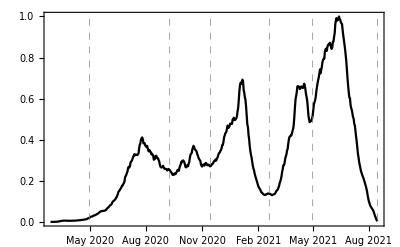

```mathematica
(* La vacunación en Colombia inicia eñ 17 de febrero 2021 pero se tomará como primer mes marzo 2021 *)
```

```mathematica
dateAdmission=Part[Sort[DeleteCases[#,""]],1]&/@dataBase20202021[[2;;,17;;24]];
```

```mathematica
dateAdmission[[;;10]]
```

{Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Wed 18 Mar 2020,Sun 15 Mar 2020,Wed 1 Apr 2020,Mon 16 Mar 2020,Sat 14 Nov 2020}

```mathematica
date={{2020,5,1},{2020,9,9},{2020,11,15},{2021,2,19},{2021,5,1},{2021,8,15}};
```

```mathematica
wave1=Thread[DateRange[DateObject[date[[1]]],DateObject[date[[2]]]]->"1"];
wave2=Thread[DateRange[DateObject[date[[2]]],DateObject[date[[3]]]]->"2"];
wave3=Thread[DateRange[DateObject[date[[3]]],DateObject[date[[4]]]]->"3"];
wave4=Thread[DateRange[DateObject[date[[4]]],DateObject[date[[5]]]]->"4"];
wave5=Thread[DateRange[DateObject[date[[5]]],DateObject[date[[6]]]]->"5"];
```

```mathematica
columna=(dateAdmission/.Flatten[{wave1,wave2,wave3,wave4,wave5}])/.DateObject[__]->"NA"(*Estas son personas entre febrero y mayo1 que no seconsideran*);
```

```mathematica
columna//Tally
```

{{NA,876},{2,83063},{1,49865},{3,46316},{5,38727},{4,26524}}

### Valleys-Peaks Admission

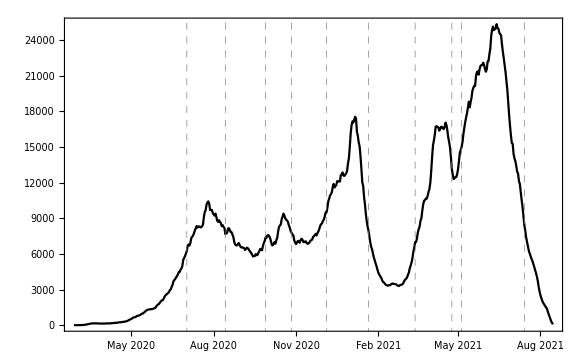

```mathematica
date={DateObject[{2020,2,27},"Day","Gregorian",-5.],DateObject[{2020,7,2},"Day","Gregorian",-5.],DateObject[{2020,8,14},"Day","Gregorian",-5.],DateObject[{2020,9,28},"Day","Gregorian",-5.],DateObject[{2020,10,27},"Day","Gregorian",-5.],DateObject[{2020,12,5},"Day","Gregorian",-5.],DateObject[{2021,1,21},"Day","Gregorian",-5.],DateObject[{2021,3,14},"Day","Gregorian",-5.],DateObject[{2021,4,24},"Day","Gregorian",-5.],DateObject[{2021,5,5},"Day","Gregorian",-5.],DateObject[{2021,7,14},"Day","Gregorian",-5.],DateObject[{2021,8,15},"Day","Gregorian",-5.]};
```

```mathematica
window1=Thread[DateRange[DateObject[date[[1]]],DateObject[date[[2]]]]->"1"];
window2=Thread[DateRange[DateObject[date[[2]]],DateObject[date[[3]]]]->"2"];
window3=Thread[DateRange[DateObject[date[[3]]],DateObject[date[[4]]]]->"3"];
window4=Thread[DateRange[DateObject[date[[4]]],DateObject[date[[5]]]]->"4"];
window5=Thread[DateRange[DateObject[date[[5]]],DateObject[date[[6]]]]->"5"];
window6=Thread[DateRange[DateObject[date[[6]]],DateObject[date[[7]]]]->"6"];
window7=Thread[DateRange[DateObject[date[[7]]],DateObject[date[[8]]]]->"7"];
window8=Thread[DateRange[DateObject[date[[8]]],DateObject[date[[9]]]]->"8"];
window9=Thread[DateRange[DateObject[date[[9]]],DateObject[date[[10]]]]->"9"];
window10=Thread[DateRange[DateObject[date[[10]]],DateObject[date[[11]]]]->"10"];
window11=Thread[DateRange[DateObject[date[[11]]],DateObject[date[[12]]]]->"11"];
```

```mathematica
columnawidows=(dateAdmission/.Flatten[{window1,window2,window3,window4,window5,window6,window7,window8,window9,window10,window11}])/.DateObject[__]->"NA"(*Estas son personas del 16 de agosto*);
```

```mathematica
columnawidows//Tally
```

{{1,11922},{5,68066},{2,24817},{6,26814},{3,23888},{4,11896},{10,32635},{8,15543},{7,17470},{9,8631},{11,3684},{NA,5}}

```mathematica
columnaVP=columnawidows/.{"1"->"valley","3"->"valley","5"->"valley","7"->"valley","9"->"valley","11"->"valley","2"->"peak","4"->"peak","6"->"peak","8"->"peak","10"->"peak"};
```

```mathematica
data11=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis11.csv"];
```

```mathematica
data11[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},1BedPathway→{7},2BedPathway→{8},tICUf→{9},sICUf→{10},tICUt→{11},sICUt→{12},tH2→{13},sH2→{14},tHf→{15},sHf→{16},tHt→{17},sHt→{18},tICU2→{19},sICU2→{20},tRD→{21},sRD→{22}|>

```mathematica
data11[[1]]
```

{ID,AgeYears,Gender,Origen1,Origen2,Vaccination,1BedPathway,2BedPathway,tICUf,sICUf,tICUt,sICUt,tH2,sH2,tHf,sHf,tHt,sHt,tICU2,sICU2,tRD,sRD}

```mathematica
(*****************************************************************************************************************)
```

```mathematica
data12={{"ID","AgeYears","Gender","Origen1","Origen2","Vaccination","Waves","PeaksValleys1","PeaksValleys2","1BedPathway","2BedPathway","tICUf","sICUf","tICUt","sICUt","tH2","sH2","tHf","sHf","tHt","sHt","tICU2","sICU2","tRD","sRD"},Sequence@@Map[Flatten,Transpose[{data11[[2;;,1;;6]],columna,columnawidows,columnaVP,data11[[2;;,7;;-1]]}]]};
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis12.csv",data12];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis12.csv",data12];
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
data12[[;;20]]//Grid
```

ID | AgeYears | Gender | Origen1 | Origen2 | Vaccination | Waves | PeaksValleys1 | PeaksValleys2 | 1BedPathway | 2BedPathway | tICUf | sICUf | tICUt | sICUt | tH2 | sH2 | tHf | sHf | tHt | sHt | tICU2 | sICU2 | tRD | sRD
1 | 34 | M | BUGA | VALLE | No | NA | 1 | valley | 1 | 1 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 1
2 | 85 | F | CARTAGENA | CARTAGENA | No | NA | 1 | valley | 1 | 1 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 1
3 | 74 | F | NEIVA | HUILA | No | NA | 1 | valley | 1 | 1 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 1
4 | 68 | F | NEIVA | HUILA | No | NA | 1 | valley | 1 | 1 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 1
5 | 48 | M | PALMIRA | VALLE | No | NA | 1 | valley | 1 | 1 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 1
6 | 61 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1
7 | 54 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 1
8 | 59 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1
9 | 37 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 5 | 3 | 10 | 1 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 1
10 | 21 | M | BARRANQUILLA | BARRANQUILLA | No | 2 | 5 | valley | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
11 | 31 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 1
12 | 72 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 5 | 3 | 8 | 1 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 1
13 | 22 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
14 | 49 | F | CALI | VALLE | No | NA | 1 | valley | 1 | 1 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 1
15 | 29 | M | PEREIRA | RISARALDA | No | NA | 1 | valley | 1 | 1 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 1
16 | 69 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | NA | NA | NA | NA | NA | NA | NA |  |  |  |  |  |  |  |  | 
17 | 57 | F | MEDELLIN | ANTIOQUIA | No | NA | 1 | valley | 5 | 3 | 1 | 1 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 1
18 | 51 | M | RIONEGRO | ANTIOQUIA | No | NA | 1 | valley | 5 | 3 | 6 | 1 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 1
19 | 65 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 4 | 2 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1

```mathematica
dataBase20202021[[16+1]](*por qué el caso 16 no tiene ruta???*)
```

{16,96,11,BOGOTA,11001,BOGOTA,69,1,M,6,,16/3/2020 0:00:00,18/3/2020 0:00:00,Recuperado,,28/3/2020 0:00:00,Wed 18 Mar 2020,Wed 25 Mar 2020,,Fri 17 Apr 2020,Thu 26 Mar 2020,Sat 18 Apr 2020,,Thu 16 Apr 2020}

```mathematica
dataBase20202021[[;;20,;;14]]//Grid
```

ID | posINS | DeparmentC | DeparmentN | MunicipioC | MunicipioN | Age | AgeUnity | Gender | EthnicityC | EthnicityN | SymptomOnset | DateDiagnosis | outcomeINS
1 | 3 | 76 | VALLE | 76111 | BUGA | 34 | 1 | M | 5 |  | 4/3/2020 0:00:00 | 9/3/2020 0:00:00 | Recuperado
2 | 8 | 13001 | CARTAGENA | 13001 | CARTAGENA | 85 | 1 | F | 6 |  | 2/3/2020 0:00:00 | 11/3/2020 0:00:00 | Recuperado
3 | 13 | 41 | HUILA | 41001 | NEIVA | 74 | 1 | F | 6 |  | 6/3/2020 0:00:00 | 12/3/2020 0:00:00 | Recuperado
4 | 14 | 41 | HUILA | 41001 | NEIVA | 68 | 1 | F | 6 |  | 6/3/2020 0:00:00 | 12/3/2020 0:00:00 | Recuperado
5 | 15 | 76 | VALLE | 76520 | PALMIRA | 48 | 1 | M | 5 |  | 7/3/2020 0:00:00 | 13/3/2020 0:00:00 | Recuperado
6 | 17 | 11 | BOGOTA | 11001 | BOGOTA | 61 | 1 | F | 5 |  | 8/3/2020 0:00:00 | 13/3/2020 0:00:00 | Recuperado
7 | 20 | 11 | BOGOTA | 11001 | BOGOTA | 54 | 1 | F | 6 |  | 9/3/2020 0:00:00 | 14/3/2020 0:00:00 | Recuperado
8 | 34 | 11 | BOGOTA | 11001 | BOGOTA | 59 | 1 | M | 6 |  | 12/3/2020 0:00:00 | 15/3/2020 0:00:00 | Recuperado
9 | 58 | 11 | BOGOTA | 11001 | BOGOTA | 37 | 1 | M | 6 |  | 9/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
10 | 62 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 21 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
11 | 65 | 11 | BOGOTA | 11001 | BOGOTA | 31 | 1 | M | 6 |  | 15/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
12 | 69 | 11 | BOGOTA | 11001 | BOGOTA | 72 | 1 | M | 6 |  | 12/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
13 | 70 | 11 | BOGOTA | 11001 | BOGOTA | 22 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
14 | 82 | 76 | VALLE | 76001 | CALI | 49 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
15 | 87 | 66 | RISARALDA | 66001 | PEREIRA | 29 | 1 | M | 6 |  | 13/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
16 | 96 | 11 | BOGOTA | 11001 | BOGOTA | 69 | 1 | M | 6 |  | 16/3/2020 0:00:00 | 18/3/2020 0:00:00 | Recuperado
17 | 109 | 5 | ANTIOQUIA | 5001 | MEDELLIN | 57 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 19/3/2020 0:00:00 | Recuperado
18 | 134 | 5 | ANTIOQUIA | 5615 | RIONEGRO | 51 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 20/3/2020 0:00:00 | Recuperado
19 | 153 | 11 | BOGOTA | 11001 | BOGOTA | 65 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 20/3/2020 0:00:00 | Fallecido

### Some important questions

```mathematica
(*************************************PREGUNTAS*)
```

```mathematica
(*Ambas bases hacen match en las filas, es decir, los casos ocupan las mismas posiciones en ambas bases de datos? R/: SI*)
```

```mathematica
data11=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis11.csv"];
```

```mathematica
dataBase20202021[[2;;,8]]//Tally  (*Solo haran match los que tienen la edad en años*)
```

{{1,242682},{2,2070},{3,619}}

```mathematica
data11[[2;;,2]]-dataBase20202021[[2;;,7]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,245136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
%//Tally (*Solo match los que tienen la edad en años*)
```

{{0,242682},{-9.16667,121},{-7.33333,144},{-0.916667,428},{-1.83333,254},{-25.9288,19},{-4.58333,172},{-5.5,179},{-10.9699,17},{-3.66667,179},{-2.75,191},{-10.0833,117},{-6.41667,129},{-26.926,14},{-27.9233,23},{-1.99452,32},{-11.9671,20},{-4.9863,16},{-14.9589,23},{-8.25,155},{-28.9205,24},{-0.99726,29},{-22.937,26},{-8.97534,8},{-3.98904,33},{-24.9315,20},{-16.9534,17},{-12.9644,29},{-5.98356,23},{-2.99178,30},{-7.97808,17},{-18.9479,17},{-17.9507,22},{-19.9452,31},{-13.9616,24},{-23.9342,21},{-21.9397,12},{-9.9726,17},{-15.9562,26},{-6.98082,17},{-20.9425,12},{-16.5,1}}

```mathematica
%%//Length
```

245371

```mathematica
data11[[2;;,1]]-dataBase20202021[[2;;,1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,245129,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
%//Tally
```

{{0,245371}}

```mathematica
%%//Length
```

245371

```mathematica
(*******************************************)
```

```mathematica
(*THE ID COLUMN OF BOTH DATABASES MISS THE SAME CASES:*)
```

```mathematica
Complement[Range[1,Length[data11]-1],data11[[2;;,1]]]
```

{158608,158695,160569,162291}

```mathematica
Complement[Range[1,Length[dataBase20202021]-1],dataBase20202021[[2;;,1]]]
```

{158608,158695,160569,162291}

```mathematica
(*******************************************)
```

```mathematica
Length[data11]-1
```

245371

```mathematica
data11[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},1BedPathway→{7},2BedPathway→{8},tICUf→{9},sICUf→{10},tICUt→{11},sICUt→{12},tH2→{13},sH2→{14},tHf→{15},sHf→{16},tHt→{17},sHt→{18},tICU2→{19},sICU2→{20},tRD→{21},sRD→{22}|>

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
data11[[2;;,3]]-dataBase20202021[[2;;,9]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,245129,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
%//Tally
```

```mathematica
{{0,245365},{"F"-"F ",5},{"M"-"M ",1}}
```

```mathematica
data11[[2;;,3]]+dataBase20202021[[2;;,9]]
```

{2 M,2 F,2 F,2 F,2 M,2 F,2 F,2 M,2 M,2 M,2 M,2 M,2 F,2 F,2 M,2 M,2 F,2 M,2 M,2 F,2 M,2 M,2 F,2 F,2 F,2 F,2 M,2 F,2 F,2 M,2 M,2 M,2 M,2 M,2 F,2 M,2 M,2 M,2 M,245293,2 F,2 F,2 M,2 F,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 M,2 F,2 M,2 F,2 F,2 M,2 M,2 M,2 M,2 M,2 M,2 F,2 M,2 F,2 F,2 M,2 F,2 M,2 F,2 F,2 M,2 M}
 |  |  |  |

```mathematica
%//Tally
```

{{2 M,136364},{2 F,109001},{F+F ,5},{M+M ,1}}

```mathematica
(**********************************************por qué hay gente que ingresa en los ultimos días ?*)
```

```mathematica
p=Position[MatchQ[#[[1,;;2]],{2021,8}]&/@dateAdmission,True];
```

```mathematica
dateAdmission//Length
```

245371

```mathematica
p//Length
```

720

```mathematica
dataBase20202021//Length
```

245372

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase20202021[[Flatten[p]+1]][[{1,Sequence@@RandomInteger[{1,700},50]}]]//Grid(* EN EFECTO SON PERSONAS QUE ENTRAN Y SALEN EN AGOSTO *)
```

231953 | 3736005 | 5 | ANTIOQUIA | 5837 | TURBO | 61 | 1 | M | 6 |  | 7/6/2021 0:00:00 | 11/6/2021 0:00:00 | Fallecido | 1/8/2021 0:00:00 |  |  |  |  |  | Sun 1 Aug 2021 |  | Mon 2 Aug 2021 | 
241880 | 4528039 | 47001 | STA MARTA D.E. | 47001 | SANTA MARTA | 62 | 1 | F | 6 |  | 24/6/2021 0:00:00 | 9/7/2021 0:00:00 | Fallecido | 13/8/2021 0:00:00 |  | Thu 12 Aug 2021 |  |  | Fri 13 Aug 2021 | Sun 1 Aug 2021 |  | Sat 14 Aug 2021 | Thu 12 Aug 2021
245015 | 4789597 | 11 | BOGOTA | 11001 | BOGOTA | 90 | 1 | M | 6 |  | 28/7/2021 0:00:00 | 30/7/2021 0:00:00 | Fallecido | 8/8/2021 0:00:00 |  | Sun 8 Aug 2021 |  | Wed 11 Aug 2021 |  |  |  |  | 
244881 | 4772233 | 11 | BOGOTA | 11001 | BOGOTA | 94 | 1 | F | 6 |  | 25/7/2021 0:00:00 | 28/7/2021 0:00:00 | Fallecido | 6/8/2021 0:00:00 |  | Sun 1 Aug 2021 |  | Sat 7 Aug 2021 |  |  |  |  | 
243342 | 4651246 | 73 | TOLIMA | 73001 | IBAGUE | 66 | 1 | M | 6 |  | 1/7/2021 0:00:00 | 16/7/2021 0:00:00 | Recuperado |  | 20/7/2021 0:00:00 | Sun 1 Aug 2021 | Tue 3 Aug 2021 |  |  |  |  |  | 
245007 | 4787731 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 18 | 1 | M | 6 |  | 20/7/2021 0:00:00 | 30/7/2021 0:00:00 | Recuperado |  | 3/8/2021 0:00:00 | Fri 6 Aug 2021 | Mon 16 Aug 2021 |  |  |  |  |  | 
245348 | 4859475 | 11 | BOGOTA | 11001 | BOGOTA | 68 | 1 | M |  |  | 5/8/2021 0:00:00 | 10/8/2021 0:00:00 | Fallecido | 14/8/2021 0:00:00 |  |  |  |  |  | Sat 14 Aug 2021 |  | Sun 15 Aug 2021 | 
242735 | 4597648 | 11 | BOGOTA | 11001 | BOGOTA | 46 | 1 | F | 6 |  | 13/7/2021 0:00:00 | 13/7/2021 0:00:00 | Recuperado |  | 28/7/2021 0:00:00 | Wed 11 Aug 2021 | Tue 17 Aug 2021 |  |  |  |  |  | 
245205 | 4820303 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 85 | 1 | M | 6 |  | 2/8/2021 0:00:00 | 4/8/2021 0:00:00 | Fallecido | 9/8/2021 0:00:00 |  | Thu 5 Aug 2021 |  | Wed 11 Aug 2021 |  |  |  |  | 
245232 | 4825239 | 68 | SANTANDER | 68276 | FLORIDABLANCA | 84 | 1 | M | 6 |  | 28/7/2021 0:00:00 | 3/8/2021 0:00:00 | Fallecido | 5/8/2021 0:00:00 |  | Fri 6 Aug 2021 |  | Sat 7 Aug 2021 |  |  |  |  | 
245179 | 4815769 | 41 | HUILA | 41770 | SUAZA | 58 | 1 | F | 6 |  | 25/7/2021 0:00:00 | 3/8/2021 0:00:00 | Fallecido | 2/8/2021 0:00:00 |  |  |  |  |  | Thu 5 Aug 2021 |  | Fri 6 Aug 2021 | 
241481 | 4494240 | 68 | SANTANDER | 68001 | BUCARAMANGA | 25 | 1 | F | 6 |  | 6/7/2021 0:00:00 | 8/7/2021 0:00:00 | Recuperado |  | 21/7/2021 0:00:00 |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021 |  | 
243242 | 4642455 | 76 | VALLE | 76834 | TULUA | 95 | 1 | M | 6 |  | 2/7/2021 0:00:00 | 17/7/2021 0:00:00 | Recuperado |  | 20/7/2021 0:00:00 | Sun 1 Aug 2021 | Thu 5 Aug 2021 |  |  |  |  |  | 
245325 | 4853785 | 54 | NORTE SANTANDER | 54001 | CUCUTA | 78 | 1 | F | 6 |  | 4/8/2021 0:00:00 | 10/8/2021 0:00:00 | Fallecido | 9/8/2021 0:00:00 |  |  |  |  |  | Thu 12 Aug 2021 |  | Fri 13 Aug 2021 | 
244939 | 4779165 | 52 | NARIÑO | 52835 | TUMACO | 29 | 1 | F | 6 |  | 26/4/2021 0:00:00 | 11/5/2021 0:00:00 | Recuperado |  | 8/8/2021 0:00:00 | Sun 1 Aug 2021 | Sat 7 Aug 2021 |  |  |  |  |  | 
244743 | 4760472 | 11 | BOGOTA | 11001 | BOGOTA | 58 | 1 | F | 6 |  | 23/7/2021 0:00:00 | 27/7/2021 0:00:00 | Recuperado |  | 12/8/2021 0:00:00 | Thu 5 Aug 2021 | Wed 11 Aug 2021 |  |  |  |  |  | 
244196 | 4711966 | 11 | BOGOTA | 11001 | BOGOTA | 54 | 1 | M | 6 |  | 18/7/2021 0:00:00 | 23/7/2021 0:00:00 | Recuperado |  | 12/8/2021 0:00:00 | Thu 5 Aug 2021 | Wed 11 Aug 2021 |  |  |  |  |  | 
245065 | 4797816 | 68 | SANTANDER | 68276 | FLORIDABLANCA | 84 | 1 | F | 6 |  | 24/7/2021 0:00:00 | 31/7/2021 0:00:00 | Fallecido | 2/8/2021 0:00:00 |  | Mon 2 Aug 2021 |  | Tue 3 Aug 2021 |  |  |  |  | 
245181 | 4815831 | 20 | CESAR | 20770 | SAN MARTIN | 57 | 1 | M | 6 |  | 25/7/2021 0:00:00 | 3/8/2021 0:00:00 | Fallecido | 5/8/2021 0:00:00 |  |  |  |  |  | Thu 5 Aug 2021 |  | Fri 6 Aug 2021 | 
245264 | 4833300 | 5 | ANTIOQUIA | 5001 | MEDELLIN | 92 | 1 | F | 6 |  | 20/7/2021 0:00:00 | 6/8/2021 0:00:00 | Fallecido | 9/8/2021 0:00:00 |  | Sat 7 Aug 2021 |  | Wed 11 Aug 2021 |  |  |  |  | 
245297 | 4846654 | 76 | VALLE | 76001 | CALI | 19 | 1 | M | 6 |  | 25/7/2021 0:00:00 | 9/8/2021 0:00:00 | Fallecido | 12/8/2021 0:00:00 |  | Wed 11 Aug 2021 |  | Fri 13 Aug 2021 |  |  |  |  | 
244770 | 4762200 | 11 | BOGOTA | 11001 | BOGOTA | 50 | 1 | M | 6 |  | 22/7/2021 0:00:00 | 27/7/2021 0:00:00 | Fallecido | 5/8/2021 0:00:00 |  |  |  |  |  | Mon 2 Aug 2021 |  | Sat 7 Aug 2021 | 
244583 | 4748890 | 54 | NORTE SANTANDER | 54001 | CUCUTA | 33 | 1 | M | 6 |  | 11/7/2021 0:00:00 | 26/7/2021 0:00:00 | Recuperado |  | 29/7/2021 0:00:00 | Mon 2 Aug 2021 | Wed 4 Aug 2021 |  |  |  |  |  | 
244683 | 4755811 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 36 | 1 | M | 6 |  | 15/7/2021 0:00:00 | 19/7/2021 0:00:00 | Recuperado |  | 29/7/2021 0:00:00 | Sun 1 Aug 2021 | Tue 3 Aug 2021 |  |  |  |  |  | 
245215 | 4822175 | 47001 | STA MARTA D.E. | 47001 | SANTA MARTA | 50 | 1 | M | 6 |  | 30/7/2021 0:00:00 | 5/8/2021 0:00:00 | Fallecido | 12/8/2021 0:00:00 |  |  |  |  |  | Fri 6 Aug 2021 |  | Thu 12 Aug 2021 | 
245178 | 4815744 | 63 | QUINDIO | 63470 | MONTENEGRO | 80 | 1 | F | 6 |  | 2/8/2021 0:00:00 | 3/8/2021 0:00:00 | Fallecido | 7/8/2021 0:00:00 |  | Thu 5 Aug 2021 |  | Sun 8 Aug 2021 |  |  |  |  | 
244991 | 4786334 | 76 | VALLE | 76147 | CARTAGO | 57 | 1 | M | 6 |  | 16/7/2021 0:00:00 | 31/7/2021 0:00:00 | Recuperado |  | 2/8/2021 0:00:00 | Wed 11 Aug 2021 | Sun 15 Aug 2021 |  |  |  |  |  | 
244521 | 4741424 | 11 | BOGOTA | 11001 | BOGOTA | 37 | 1 | F | 6 |  | 20/7/2021 0:00:00 | 25/7/2021 0:00:00 | Recuperado |  | 12/8/2021 0:00:00 | Sun 1 Aug 2021 | Wed 11 Aug 2021 |  |  |  |  |  | 
244950 | 4780808 | 11 | BOGOTA | 11001 | BOGOTA | 84 | 1 | M | 6 |  | 25/7/2021 0:00:00 | 30/7/2021 0:00:00 | Fallecido | 7/8/2021 0:00:00 |  | Thu 5 Aug 2021 |  | Sun 8 Aug 2021 |  |  |  |  | 
244761 | 4761887 | 11 | BOGOTA | 11001 | BOGOTA | 88 | 1 | F | 6 |  | 23/7/2021 0:00:00 | 27/7/2021 0:00:00 | Recuperado |  | 12/8/2021 0:00:00 | Sun 1 Aug 2021 | Wed 11 Aug 2021 |  |  |  |  |  | 
245279 | 4836932 | 5 | ANTIOQUIA | 5001 | MEDELLIN | 87 | 1 | F | 6 |  | 1/8/2021 0:00:00 | 6/8/2021 0:00:00 | Fallecido | 10/8/2021 0:00:00 |  | Sun 8 Aug 2021 |  | Wed 11 Aug 2021 |  |  |  |  | 
242502 | 4581349 | 11 | BOGOTA | 11001 | BOGOTA | 33 | 1 | F | 6 |  | 7/7/2021 0:00:00 | 14/7/2021 0:00:00 | Fallecido | 13/8/2021 0:00:00 |  |  |  |  |  | Wed 11 Aug 2021 |  | Sat 14 Aug 2021 | 
245038 | 4792913 | 63 | QUINDIO | 63001 | ARMENIA | 86 | 1 | M | 6 |  | 25/7/2021 0:00:00 | 28/7/2021 0:00:00 | Fallecido | 29/7/2021 0:00:00 |  | Sun 1 Aug 2021 |  | Mon 2 Aug 2021 |  |  |  |  | 
245120 | 4806052 | 5 | ANTIOQUIA | 5440 | MARINILLA | 83 | 1 | M | 6 |  | 22/7/2021 0:00:00 | 31/7/2021 0:00:00 | Fallecido | 10/8/2021 0:00:00 |  |  |  |  |  | Tue 3 Aug 2021 |  | Wed 11 Aug 2021 | 
244982 | 4785764 | 25 | CUNDINAMARCA | 25754 | SOACHA | 56 | 1 | F | 6 |  | 16/7/2021 0:00:00 | 31/7/2021 0:00:00 | Fallecido | 5/8/2021 0:00:00 |  |  |  |  |  | Sun 1 Aug 2021 |  | Fri 6 Aug 2021 | 
245336 | 4854284 | 68 | SANTANDER | 68001 | BUCARAMANGA | 85 | 1 | M | 6 |  | 1/8/2021 0:00:00 | 10/8/2021 0:00:00 | Fallecido | 11/8/2021 0:00:00 |  | Thu 12 Aug 2021 |  | Fri 13 Aug 2021 |  |  |  |  | 
245165 | 4814240 | 54 | NORTE SANTANDER | 54518 | PAMPLONA | 67 | 1 | M | 6 |  | 19/7/2021 0:00:00 | 3/8/2021 0:00:00 | Recuperado |  | 5/8/2021 0:00:00 | Thu 12 Aug 2021 | Tue 17 Aug 2021 |  |  | Fri 6 Aug 2021 |  |  | Thu 12 Aug 2021
235378 | 3985870 | 76 | VALLE | 76001 | CALI | 69 | 1 | M | 6 |  | 10/6/2021 0:00:00 | 21/6/2021 0:00:00 | Recuperado |  | 24/6/2021 0:00:00 |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021 |  | 
244479 | 4738096 | 11 | BOGOTA | 11001 | BOGOTA | 67 | 1 | F | 6 |  | 21/7/2021 0:00:00 | 26/7/2021 0:00:00 | Fallecido | 11/8/2021 0:00:00 |  |  |  |  |  | Sun 1 Aug 2021 |  | Thu 12 Aug 2021 | 
245037 | 4792794 | 23 | CORDOBA | 23466 | MONTELIBANO | 24 | 1 | F | 6 |  | 15/7/2021 0:00:00 | 29/7/2021 0:00:00 | Recuperado |  | 2/8/2021 0:00:00 | Wed 11 Aug 2021 | Thu 12 Aug 2021 |  |  |  |  |  | 
243216 | 4640183 | 41 | HUILA | 41551 | PITALITO | 64 | 1 | M | 6 |  | 12/7/2021 0:00:00 | 18/7/2021 0:00:00 | Fallecido | 7/8/2021 0:00:00 |  | Fri 6 Aug 2021 |  | Sun 8 Aug 2021 |  | Sun 1 Aug 2021 |  |  | Fri 6 Aug 2021
243297 | 4645905 | 11 | BOGOTA | 11001 | BOGOTA | 65 | 1 | F | 6 |  | 13/7/2021 0:00:00 | 16/7/2021 0:00:00 | Recuperado |  | 30/7/2021 0:00:00 | Sun 1 Aug 2021 | Fri 13 Aug 2021 |  |  |  |  |  | 
244277 | 4722435 | 11 | BOGOTA | 11001 | BOGOTA | 29 | 1 | M | 6 |  | 19/7/2021 0:00:00 | 23/7/2021 0:00:00 | Recuperado |  | 6/8/2021 0:00:00 | Sun 1 Aug 2021 | Thu 5 Aug 2021 |  |  |  |  |  | 
245170 | 4815350 | 15 | BOYACA | 15469 | MONIQUIRA | 65 | 1 | F | 6 |  | 19/7/2021 0:00:00 | 4/8/2021 0:00:00 | Fallecido | 1/8/2021 0:00:00 |  |  |  |  |  | Thu 5 Aug 2021 |  | Fri 6 Aug 2021 | 
241580 | 4503408 | 44 | GUAJIRA | 44001 | RIOHACHA | 41 | 1 | F | 6 |  | 8/7/2021 0:00:00 | 8/7/2021 0:00:00 | Recuperado |  | 23/7/2021 0:00:00 | Thu 12 Aug 2021 | Fri 13 Aug 2021 |  |  |  |  |  | 
245066 | 4797817 | 11 | BOGOTA | 11001 | BOGOTA | 68 | 1 | F | 6 |  | 21/7/2021 0:00:00 | 28/7/2021 0:00:00 | Recuperado |  | 6/8/2021 0:00:00 | Mon 2 Aug 2021 | Thu 5 Aug 2021 |  |  |  |  |  | 
244935 | 4778308 | 23 | CORDOBA | 23001 | MONTERIA | 78 | 1 | F | 6 |  | 22/7/2021 0:00:00 | 28/7/2021 0:00:00 | Fallecido | 14/8/2021 0:00:00 |  |  |  |  |  | Sun 1 Aug 2021 |  | Sat 14 Aug 2021 | 
244864 | 4770052 | 11 | BOGOTA | 11001 | BOGOTA | 82 | 1 | M | 6 |  | 24/7/2021 0:00:00 | 29/7/2021 0:00:00 | Fallecido | 4/8/2021 0:00:00 |  |  |  |  |  | Mon 2 Aug 2021 |  | Thu 5 Aug 2021 | 
244723 | 4758670 | 54 | NORTE SANTANDER | 54001 | CUCUTA | 8 | 1 | F | 6 |  | 20/7/2021 0:00:00 | 26/7/2021 0:00:00 | Recuperado |  | 5/8/2021 0:00:00 |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021 |  | 
244956 | 4782053 | 11 | BOGOTA | 11001 | BOGOTA | 80 | 1 | M | 6 |  | 24/7/2021 0:00:00 | 29/7/2021 0:00:00 | Recuperado |  | 7/8/2021 0:00:00 | Sun 1 Aug 2021 | Fri 6 Aug 2021 |  |  |  |  |  | 
244683 | 4755811 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 36 | 1 | M | 6 |  | 15/7/2021 0:00:00 | 19/7/2021 0:00:00 | Recuperado |  | 29/7/2021 0:00:00 | Sun 1 Aug 2021 | Tue 3 Aug 2021 |  |  |  |  |  |

```mathematica
(Sort[#]&/@dataBase20202021[[All,17;;24]])[[Flatten[p]+1]]//Grid
```

|  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021 | Fri 6 Aug 2021 | Sat 14 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021 | Fri 6 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Tue 17 Aug 2021
 |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021 | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 14 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021 | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Fri 13 Aug 2021
 |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021 | Mon 2 Aug 2021 | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Tue 17 Aug 2021
 |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021 | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sun 8 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021 | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 13 Aug 2021
 |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Tue 17 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021 | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 16 Aug 2021
 |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021 | Sun 8 Aug 2021 | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021 | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 4 Aug 2021
 |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021 | Mon 2 Aug 2021 | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Mon 2 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 1 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Tue 3 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Mon 2 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021
 |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021 | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 4 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Tue 3 Aug 2021 | Fri 6 Aug 2021
 |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021 | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021 | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Thu 5 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Wed 4 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Thu 5 Aug 2021 | Fri 6 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021 | Sat 7 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Fri 6 Aug 2021 | Sat 7 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021 | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Sun 8 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sat 7 Aug 2021 | Thu 12 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021 | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Sun 8 Aug 2021 | Wed 11 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Wed 11 Aug 2021 | Thu 12 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Fri 13 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Thu 12 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sat 14 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Fri 13 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sat 14 Aug 2021 | Sun 15 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Sun 15 Aug 2021 | Mon 16 Aug 2021
 |  |  |  |  |  | Mon 16 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 16 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 16 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 16 Aug 2021 | Tue 17 Aug 2021
 |  |  |  |  |  | Mon 16 Aug 2021 | Tue 17 Aug 2021

## DataBase 13

This is the DataBase 12 but here the categories including not only the admission but also the discharge in each window (wave, peak, valley). In this way the variables “Waves”,”PeaksValleys1”,”PeaksValleys2” are not the same as in 12

```mathematica
dataBase20202021=Import["/home/lina/Documents/UnCover/datos_INS/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
Length[dataBase20202021]-1
```

245371

### Waves Admission

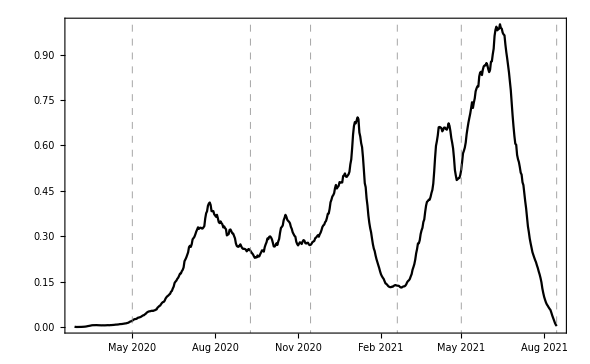

```mathematica
(* La vacunación en Colombia inicia eñ 17 de febrero 2021 pero se tomará como primer mes marzo 2021 *)
```

```mathematica
dateAdmission=Sort[DeleteCases[#,""]][[{1,-1}]]&/@dataBase20202021[[2;;,17;;24]];
```

```mathematica
dateAdmission[[1]]
```

{Sun 15 Mar 2020,Mon 23 Mar 2020}

```mathematica
dateAdmission[[;;10]]
```

{Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Sun 15 Mar 2020,Wed 18 Mar 2020,Sun 15 Mar 2020,Wed 1 Apr 2020,Mon 16 Mar 2020,Sat 14 Nov 2020}

```mathematica
date={{2020,5,1},{2020,9,9},{2020,11,15},{2021,2,19},{2021,5,1},{2021,8,15}};
```

```mathematica
wave1=Thread[DateRange[DateObject[date[[1]]],DateObject[date[[2]]]]->"1"];
wave2=Thread[DateRange[DateObject[date[[2]]],DateObject[date[[3]]]]->"2"];
wave3=Thread[DateRange[DateObject[date[[3]]],DateObject[date[[4]]]]->"3"];
wave4=Thread[DateRange[DateObject[date[[4]]],DateObject[date[[5]]]]->"4"];
wave5=Thread[DateRange[DateObject[date[[5]]],DateObject[date[[6]]]]->"5"];
```

```mathematica
columna=((dateAdmission/.Flatten[{wave1,wave2,wave3,wave4,wave5}])/.DateObject[__]->"NA")/.{{x_,y_}/;x==y:>x,{x_,y_}/;x!=y:>"NA",{"NA","NA"}:>"NA"}(*Estas son personas entre febrero y mayo1 que no seconsideran*);
```

```mathematica
columna//Tally
```

{{NA,46699},{2,81227},{1,36620},{3,28765},{5,38509},{4,13551}}

### Valleys-Peaks Admission

-Graphics-

```mathematica
date={DateObject[{2020,2,27},"Day","Gregorian",-5.],DateObject[{2020,7,2},"Day","Gregorian",-5.],DateObject[{2020,8,14},"Day","Gregorian",-5.],DateObject[{2020,9,28},"Day","Gregorian",-5.],DateObject[{2020,10,27},"Day","Gregorian",-5.],DateObject[{2020,12,5},"Day","Gregorian",-5.],DateObject[{2021,1,21},"Day","Gregorian",-5.],DateObject[{2021,3,14},"Day","Gregorian",-5.],DateObject[{2021,4,24},"Day","Gregorian",-5.],DateObject[{2021,5,5},"Day","Gregorian",-5.],DateObject[{2021,7,14},"Day","Gregorian",-5.],DateObject[{2021,8,15},"Day","Gregorian",-5.]};
```

```mathematica
window1=Thread[DateRange[DateObject[date[[1]]],DateObject[date[[2]]]]->"1"];
window2=Thread[DateRange[DateObject[date[[2]]],DateObject[date[[3]]]]->"2"];
window3=Thread[DateRange[DateObject[date[[3]]],DateObject[date[[4]]]]->"3"];
window4=Thread[DateRange[DateObject[date[[4]]],DateObject[date[[5]]]]->"4"];
window5=Thread[DateRange[DateObject[date[[5]]],DateObject[date[[6]]]]->"5"];
window6=Thread[DateRange[DateObject[date[[6]]],DateObject[date[[7]]]]->"6"];
window7=Thread[DateRange[DateObject[date[[7]]],DateObject[date[[8]]]]->"7"];
window8=Thread[DateRange[DateObject[date[[8]]],DateObject[date[[9]]]]->"8"];
window9=Thread[DateRange[DateObject[date[[9]]],DateObject[date[[10]]]]->"9"];
window10=Thread[DateRange[DateObject[date[[10]]],DateObject[date[[11]]]]->"10"];
window11=Thread[DateRange[DateObject[date[[11]]],DateObject[date[[12]]]]->"11"];
```

```mathematica
columnawidows=((dateAdmission/.Flatten[{window1,window2,window3,window4,window5,window6,window7,window8,window9,window10,window11}])/.DateObject[__]->"NA")/.{{x_,y_}/;x==y:>x,{x_,y_}/;x!=y:>"NA",{"NA","NA"}:>"NA"}(*Estas son personas del 16 de agosto*);
```

```mathematica
columnawidows//Tally
```

{{1,6293},{5,61832},{NA,96498},{2,8695},{6,11196},{3,10014},{4,4168},{10,23389},{8,7208},{7,10599},{9,1925},{11,3554}}

```mathematica
columnaVP=columnawidows/.{"1"->"valley","3"->"valley","5"->"valley","7"->"valley","9"->"valley","11"->"valley","2"->"peak","4"->"peak","6"->"peak","8"->"peak","10"->"peak"};
```

```mathematica
data11=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis11.csv"];
```

```mathematica
data11[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},1BedPathway→{7},2BedPathway→{8},tICUf→{9},sICUf→{10},tICUt→{11},sICUt→{12},tH2→{13},sH2→{14},tHf→{15},sHf→{16},tHt→{17},sHt→{18},tICU2→{19},sICU2→{20},tRD→{21},sRD→{22}|>

```mathematica
data11[[1]]
```

{ID,AgeYears,Gender,Origen1,Origen2,Vaccination,1BedPathway,2BedPathway,tICUf,sICUf,tICUt,sICUt,tH2,sH2,tHf,sHf,tHt,sHt,tICU2,sICU2,tRD,sRD}

```mathematica
(*****************************************************************************************************************)
```

```mathematica
data13={{"ID","AgeYears","Gender","Origen1","Origen2","Vaccination","Waves","PeaksValleys1","PeaksValleys2","1BedPathway","2BedPathway","tICUf","sICUf","tICUt","sICUt","tH2","sH2","tHf","sHf","tHt","sHt","tICU2","sICU2","tRD","sRD"},Sequence@@Map[Flatten,Transpose[{data11[[2;;,1;;6]],columna,columnawidows,columnaVP,data11[[2;;,7;;-1]]}]]};
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis13.csv",data13];
```

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis13.csv",data13];
```

```mathematica
(*****************************************************************************************************************)
```

```mathematica
data13[[;;20]]//Grid
```

ID | AgeYears | Gender | Origen1 | Origen2 | Vaccination | Waves | PeaksValleys1 | PeaksValleys2 | 1BedPathway | 2BedPathway | tICUf | sICUf | tICUt | sICUt | tH2 | sH2 | tHf | sHf | tHt | sHt | tICU2 | sICU2 | tRD | sRD
1 | 34 | M | BUGA | VALLE | No | NA | 1 | valley | 1 | 1 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 1
2 | 85 | F | CARTAGENA | CARTAGENA | No | NA | 1 | valley | 1 | 1 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 0 | 8 | 1
3 | 74 | F | NEIVA | HUILA | No | NA | 1 | valley | 1 | 1 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 1
4 | 68 | F | NEIVA | HUILA | No | NA | 1 | valley | 1 | 1 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 0 | 10 | 1
5 | 48 | M | PALMIRA | VALLE | No | NA | 1 | valley | 1 | 1 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 1
6 | 61 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1
7 | 54 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 1
8 | 59 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1
9 | 37 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 5 | 3 | 10 | 1 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 1
10 | 21 | M | BARRANQUILLA | BARRANQUILLA | No | 2 | 5 | valley | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
11 | 31 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 1
12 | 72 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 5 | 3 | 8 | 1 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 0 | 25 | 1
13 | 22 | F | BOGOTA | BOGOTA | No | NA | 1 | valley | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
14 | 49 | F | CALI | VALLE | No | NA | 1 | valley | 1 | 1 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 0 | 6 | 1
15 | 29 | M | PEREIRA | RISARALDA | No | NA | 1 | valley | 1 | 1 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 1
16 | 69 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | NA | NA | NA | NA | NA | NA | NA |  |  |  |  |  |  |  |  | 
17 | 57 | F | MEDELLIN | ANTIOQUIA | No | NA | 1 | valley | 5 | 3 | 1 | 1 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 0 | 7 | 1
18 | 51 | M | RIONEGRO | ANTIOQUIA | No | NA | 1 | valley | 5 | 3 | 6 | 1 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 0 | 12 | 1
19 | 65 | M | BOGOTA | BOGOTA | No | NA | 1 | valley | 4 | 2 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 0 | 11 | 1

```mathematica
dataBase20202021[[16+1]](*por qué el caso 16 no tiene ruta???*)
```

{16,96,11,BOGOTA,11001,BOGOTA,69,1,M,6,,16/3/2020 0:00:00,18/3/2020 0:00:00,Recuperado,,28/3/2020 0:00:00,Wed 18 Mar 2020,Wed 25 Mar 2020,,Fri 17 Apr 2020,Thu 26 Mar 2020,Sat 18 Apr 2020,,Thu 16 Apr 2020}

```mathematica
dataBase20202021[[;;20,;;14]]//Grid
```

ID | posINS | DeparmentC | DeparmentN | MunicipioC | MunicipioN | Age | AgeUnity | Gender | EthnicityC | EthnicityN | SymptomOnset | DateDiagnosis | outcomeINS
1 | 3 | 76 | VALLE | 76111 | BUGA | 34 | 1 | M | 5 |  | 4/3/2020 0:00:00 | 9/3/2020 0:00:00 | Recuperado
2 | 8 | 13001 | CARTAGENA | 13001 | CARTAGENA | 85 | 1 | F | 6 |  | 2/3/2020 0:00:00 | 11/3/2020 0:00:00 | Recuperado
3 | 13 | 41 | HUILA | 41001 | NEIVA | 74 | 1 | F | 6 |  | 6/3/2020 0:00:00 | 12/3/2020 0:00:00 | Recuperado
4 | 14 | 41 | HUILA | 41001 | NEIVA | 68 | 1 | F | 6 |  | 6/3/2020 0:00:00 | 12/3/2020 0:00:00 | Recuperado
5 | 15 | 76 | VALLE | 76520 | PALMIRA | 48 | 1 | M | 5 |  | 7/3/2020 0:00:00 | 13/3/2020 0:00:00 | Recuperado
6 | 17 | 11 | BOGOTA | 11001 | BOGOTA | 61 | 1 | F | 5 |  | 8/3/2020 0:00:00 | 13/3/2020 0:00:00 | Recuperado
7 | 20 | 11 | BOGOTA | 11001 | BOGOTA | 54 | 1 | F | 6 |  | 9/3/2020 0:00:00 | 14/3/2020 0:00:00 | Recuperado
8 | 34 | 11 | BOGOTA | 11001 | BOGOTA | 59 | 1 | M | 6 |  | 12/3/2020 0:00:00 | 15/3/2020 0:00:00 | Recuperado
9 | 58 | 11 | BOGOTA | 11001 | BOGOTA | 37 | 1 | M | 6 |  | 9/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
10 | 62 | 8001 | BARRANQUILLA | 8001 | BARRANQUILLA | 21 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
11 | 65 | 11 | BOGOTA | 11001 | BOGOTA | 31 | 1 | M | 6 |  | 15/3/2020 0:00:00 | 16/3/2020 0:00:00 | Recuperado
12 | 69 | 11 | BOGOTA | 11001 | BOGOTA | 72 | 1 | M | 6 |  | 12/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
13 | 70 | 11 | BOGOTA | 11001 | BOGOTA | 22 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
14 | 82 | 76 | VALLE | 76001 | CALI | 49 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
15 | 87 | 66 | RISARALDA | 66001 | PEREIRA | 29 | 1 | M | 6 |  | 13/3/2020 0:00:00 | 17/3/2020 0:00:00 | Recuperado
16 | 96 | 11 | BOGOTA | 11001 | BOGOTA | 69 | 1 | M | 6 |  | 16/3/2020 0:00:00 | 18/3/2020 0:00:00 | Recuperado
17 | 109 | 5 | ANTIOQUIA | 5001 | MEDELLIN | 57 | 1 | F | 6 |  | 14/3/2020 0:00:00 | 19/3/2020 0:00:00 | Recuperado
18 | 134 | 5 | ANTIOQUIA | 5615 | RIONEGRO | 51 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 20/3/2020 0:00:00 | Recuperado
19 | 153 | 11 | BOGOTA | 11001 | BOGOTA | 65 | 1 | M | 6 |  | 10/3/2020 0:00:00 | 20/3/2020 0:00:00 | Fallecido

### Some important questions

```mathematica
Select[data13,#[[1]]==2095&]
```

{{2095,40,F,BUENAVENTURA,VALLE,No,1,2,peak,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,1}}

```mathematica
p=Select[data13,#[[7]]=="2"&][[All,1]];
```

```mathematica
p//Length
```

81227

```mathematica
dataBase20202021//Length
```

245372

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
Table[Select[dataBase20202021,#[[1]]==i&],{i,p[[RandomChoice[Range[1,81227,1],10]]]}]//Grid(* AQUI CONFIRMO QUE EN EFECTO LAS PERSONAS ENTRAN Y SALEN ENTRE EL INICIO Y EL FINAL DE LA 2DA OLAS *)
```

{94670,837197,25,CUNDINAMARCA,25473,MOSQUERA,34,1,M,6,,24/9/2020 0:00:00,1/10/2020 0:00:00,Recuperado,,14/10/2020 0:00:00,Fri 2 Oct 2020,Sun 11 Oct 2020,,,,,,}
{93659,828759,11,BOGOTA,11001,BOGOTA,84,1,F,6,,13/9/2020 0:00:00,29/9/2020 0:00:00,Recuperado,,30/10/2020 0:00:00,Wed 30 Sep 2020,Thu 12 Nov 2020,,,,,,}
{87974,777036,11,BOGOTA,11001,BOGOTA,41,1,F,6,,10/9/2020 0:00:00,17/9/2020 0:00:00,Recuperado,,6/10/2020 0:00:00,,,,,Sat 14 Nov 2020,Sun 15 Nov 2020,,}
{94173,833068,41,HUILA,41132,CAMPOALEGRE,82,1,M,6,,18/9/2020 0:00:00,29/9/2020 0:00:00,Recuperado,,16/10/2020 0:00:00,Thu 1 Oct 2020,Fri 16 Oct 2020,,,,,,}
{74838,651035,20,CESAR,20001,VALLEDUPAR,9,1,M,6,,4/9/2020 0:00:00,4/9/2020 0:00:00,Recuperado,,14/11/2020 0:00:00,Sat 14 Nov 2020,Sun 15 Nov 2020,,,,,,}
{78086,680783,13001,CARTAGENA,13001,CARTAGENA,27,1,F,6,,30/8/2020 0:00:00,9/9/2020 0:00:00,Recuperado,,23/9/2020 0:00:00,,,,,Thu 12 Nov 2020,Fri 13 Nov 2020,,}
{63089,535483,25,CUNDINAMARCA,25286,FUNZA,26,1,F,6,,12/8/2020 0:00:00,22/8/2020 0:00:00,Recuperado,,3/9/2020 0:00:00,Thu 12 Nov 2020,Fri 13 Nov 2020,,,,,,}
{56409,476119,5,ANTIOQUIA,5001,MEDELLIN,50,1,F,6,,1/8/2020 0:00:00,16/8/2020 0:00:00,Recuperado,,26/8/2020 0:00:00,Sat 14 Nov 2020,Sun 15 Nov 2020,,,,,,}
{88633,782983,11,BOGOTA,11001,BOGOTA,47,1,F,6,,21/9/2020 0:00:00,21/9/2020 0:00:00,Recuperado,,13/10/2020 0:00:00,Mon 28 Sep 2020,Sun 11 Oct 2020,,,,,,}
{119933,1055470,5,ANTIOQUIA,5001,MEDELLIN,22,1,F,6,,24/10/2020 0:00:00,28/10/2020 0:00:00,Recuperado,,10/11/2020 0:00:00,Sat 31 Oct 2020,Sun 1 Nov 2020,,,,,,}

#### Counting the cases

Total cases in august 17th 2021

```mathematica
dataINS=Import["/home/lina/Documents/UnCover/datos_INS/2021-08-17.csv"];
```

```mathematica
Length[dataINS]-1
```

4874169

Total hospitalized cases with an outcome  between  march 15th 2020 to august 17th 2021

```mathematica
Length[data13]-1
```

```mathematica
245371/4874169.
```

0.0503411

Total hospitalized cases with an identified bed pathway

```mathematica
Length[data13]-Count[data13,{_,_,_,_,_,_,_,_,_,"NA",__}]-1
```

240141

```mathematica
Length[data13]-Count[data13,{_,_,_,_,_,_,_,_,_,_,"NA",__}]-1
```

240141

Total hospitalized cases with LoS lower than 100 days

```mathematica
data13[[All,2]]//Tally//Sort
```

{{0.00273973,29},{0.00547945,32},{0.00821918,30},{0.0109589,33},{0.0136986,16},{0.0164384,23},{0.0191781,17},{0.0219178,17},{0.0246575,8},{0.0273973,17},{0.030137,17},{0.0328767,20},{0.0356164,29},{0.0383562,24},{0.0410959,23},{0.0438356,26},{0.0465753,17},{0.0493151,22},{0.0520548,17},{0.0547945,31},{0.0575342,12},{0.060274,12},{0.0630137,26},{0.0657534,21},{0.0684932,20},{0.0712329,19},{0.0739726,14},{0.0767123,23},{0.0794521,24},{0.0833333,428},{0.166667,254},{0.25,191},{0.333333,179},{0.416667,172},{0.5,179},{0.583333,129},{0.666667,144},{0.75,155},{0.833333,121},{0.916667,117},{1,1053},{1.5,1},{2,649},{3,486},{4,427},{5,391},{6,344},{7,419},{8,377},{9,404},{10,397},{11,393},{12,449},{13,437},{14,527},{15,580},{16,686},{17,735},{18,860},{19,1298},{20,1461},{21,1492},{22,1754},{23,1987},{24,2304},{25,2399},{26,2606},{27,2567},{28,2783},{29,2816},{30,2788},{31,2957},{32,2905},{33,2895},{34,2939},{35,3131},{36,3076},{37,3286},{38,3339},{39,3303},{40,3481},{41,3434},{42,3318},{43,3235},{44,3284},{45,3201},{46,3160},{47,3355},{48,3503},{49,3737},{50,3861},{51,3984},{52,4158},{53,4270},{54,4401},{55,4528},{56,4662},{57,4814},{58,4785},{59,4778},{60,4968},{61,4619},{62,4822},{63,4627},{64,4507},{65,4443},{66,4291},{67,4390},{68,4153},{69,4018},{70,4059},{71,3731},{72,3808},{73,3505},{74,3478},{75,3361},{76,3036},{77,2937},{78,2852},{79,2815},{80,2821},{81,2446},{82,2281},{83,2121},{84,1975},{85,1885},{86,1635},{87,1478},{88,1202},{89,977},{90,921},{91,710},{92,604},{93,441},{94,329},{95,251},{96,181},{97,116},{98,79},{99,49},{100,52},{101,24},{102,15},{103,6},{104,6},{105,2},{106,4},{107,2},{AgeYears,1}}

## DataBase 14

```mathematica
data13=Import["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis13.csv"];
```

```mathematica
data13[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},tICUf→{12},sICUf→{13},tICUt→{14},sICUt→{15},tH2→{16},sH2→{17},tHf→{18},sHf→{19},tHt→{20},sHt→{21},tICU2→{22},sICU2→{23},tRD→{24},sRD→{25}|>

### variable 1:IPM

```mathematica
(*1. ID caso.2. Departamento (por código o nombre).3. Índice de pobreza multidimensional general por departamento.4. Índice barreras de acceso a servicios de salud por departamento.5. Índice hacinamiento crítico por departamento.6. Índice sin acceso a fuente de agua mejorada por departamento.7. Índice sin aseguramiento en salud por departamento.8. índice inadecuada eliminación de excretas por departamento.9. Índice bajo logro educativo.10. Municipio (por código o nombre*)
```

```mathematica
ipm=Import["/home/lina/Documents/UnCover/datos_INS/Datos IPM.xlsx"];
```

```mathematica
ipm//Dimensions
```

{3}

```mathematica
ipm//Length
```

3

```mathematica
ipm[[1,1;;3]]
```

{{Departamento,IPM2019,BLE2019,BASS2019,HA2019,IEE2019,SAAM2019,SAS2019},{ANTIOQUIA,15.7,42.5,2.6,6.8,8.4,9.5,11.2},{ATLANTICO,14.9,31.6,6.7,13.9,10.4,3.3,13.3}}

```mathematica
ipm[[2,1;;3]]
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,}}

```mathematica
ipm[[2]]//DeleteDuplicates
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,},{BOGOTA,7.5,23.3,2.9,6.4,0.5,0.6,16.9,,,},{BOLIVAR,28.1,46.7,0.8,12.9,36.6,17.4,9.1,,,},{BOYACA,11.7,52.1,0.3,3.4,5.6,7.5,6.5,,,},{CALDAS,14.5,47.2,4.1,3.7,7.,8.7,10.6,,,},{CAQUETA,26.1,57.8,4.5,8.6,12.5,18.1,6.8,,,},{CAUCA,28.2,62.2,3.5,4.7,8.9,19.7,8.2,,,},{CESAR,27.2,46.1,0.6,17.,15.3,8.1,11.8,,,},{CORDOBA,31.8,53.9,0.7,10.9,18.5,19.,3.8,,,},{CUNDINAMARCA,11.4,40.8,0.7,4.7,3.4,6.4,12.5,,,},{CHOCO,49.,59.2,1.3,7.7,66.7,74.7,5.4,,,},{HUILA,23.4,53.6,6.4,6.2,6.4,11.5,7.4,,,},{GUAJIRA,51.7,59.4,2.4,24.9,49.4,48.,15.7,,,},{MAGDALENA,33.4,51.9,1.9,19.,29.2,17.2,9.5,,,},{META,14.1,42.4,2.8,5.1,5.3,13.3,8.,,,},{NARIÑO,27.3,61.8,6.3,7.7,18.5,22.7,7.1,,,},{NORTE SANTANDER,26.1,50.8,7.6,14.3,9.,12.3,17.5,,,},{QUINDIO,12.9,42.,2.2,4.3,2.1,3.,12.6,,,},{RISARALDA,13.1,42.7,0.9,3.8,4.8,6.8,9.4,,,},{SANTANDER,12.5,43.5,1.3,5.1,6.,9.8,7.8,,,},{SUCRE,38.1,57.5,3.6,14.9,28.8,10.7,7.2,,,},{TOLIMA,19.,51.6,6.4,6.2,5.8,9.7,10.,,,},{VALLE,11.1,34.9,1.2,4.4,3.,3.2,10.1,,,},{ARAUCA,26.1,54.8,2.4,9.7,11.1,5.2,18.,,,},{CASANARE,19.6,50.,2.3,10.,8.1,10.4,12.6,,,},{PUTUMAYO,27.8,58.9,3.4,5.9,8.4,37.2,7.4,,,},{SAN ANDRES,11.9,24.,0.,9.8,80.1,57.1,4.1,,,},{AMAZONAS,39.,48.2,0.4,14.2,34.,53.3,5.6,,,},{GUAINIA,65.9,61.9,3.2,16.6,64.5,77.2,10.7,,,},{GUAVIARE,34.6,56.1,6.8,9.7,25.3,46.,11.3,,,},{VAUPES,65.6,60.7,2.2,31.1,57.5,69.3,3.9,,,},{VICHADA,75.6,74.9,0.8,21.9,84.3,67.2,12.9,,,},{BARRANQUILLA,17.4,29.,3.,13.5,2.1,1.,20.1,,,},{CARTAGENA,19.9,33.5,2.5,14.2,7.8,5.4,17.6,,,},{STA MARTA D.E.,24.4,34.2,3.7,19.4,13.9,18.4,16.5,,,},{,,,,,,,,,,}}

```mathematica
ipm[[3,1;;3]]
```

{{Variable ,Codificación },{Departamento,Departamento },{IPM,Indice de pobreza multidimensional }}

```mathematica
imp2019rules=Thread[ipm[[1,2;;,1]]->ipm[[1,2;;,2;;]]]
```

{ANTIOQUIA→{15.7,42.5,2.6,6.8,8.4,9.5,11.2},ATLANTICO→{14.9,31.6,6.7,13.9,10.4,3.3,13.3},BOGOTA→{7.1,21.9,10.3,6.5,0.,0.1,13.5},BOLIVAR→{26.9,49.,4.,16.4,38.9,17.1,10.1},BOYACA→{12.8,55.,1.5,4.3,8.4,16.7,7.3},CALDAS→{14.3,51.1,4.7,4.3,5.3,12.1,9.2},CAQUETA→{25.7,62.9,4.3,8.7,14.3,24.,8.6},CAUCA→{24.,62.3,6.9,4.5,9.6,21.7,7.9},CESAR→{25.5,49.6,3.8,19.6,14.6,9.2,14.9},CORDOBA→{34.7,57.3,12.8,14.,23.8,26.5,6.9},CUNDINAMARCA→{12.3,44.6,2.9,6.5,5.6,10.4,12.8},CHOCO→{42.3,63.4,3.2,9.3,67.5,67.5,7.5},HUILA→{18.3,56.4,5.,6.1,7.4,14.4,7.3},GUAJIRA→{48.8,60.9,4.7,23.7,46.,42.9,25.6},MAGDALENA→{31.6,51.3,3.4,21.3,33.9,19.7,14.1},META→{19.1,48.4,9.5,6.7,5.,10.8,10.8},NARIÑO→{23.3,67.6,8.,7.9,16.9,23.,6.3},NORTE SANTANDER→{24.2,48.8,6.4,13.7,9.,13.5,17.5},QUINDIO→{10.2,42.,5.4,4.3,1.1,2.9,12.2},RISARALDA→{11.1,47.7,3.9,3.4,5.8,4.8,8.4},SANTANDER→{12.4,46.2,3.8,7.7,7.6,15.7,10.8},SUCRE→{33.3,58.7,7.4,14.1,25.9,12.5,9.7},TOLIMA→{15.2,50.5,5.2,5.5,8.8,14.2,7.3},VALLE→{10.8,42.3,2.4,4.6,6.,4.9,9.9},ARAUCA→{23.3,59.,0.9,9.8,10.4,6.8,20.},CASANARE→{18.3,53.7,3.6,9.7,6.9,8.4,11.1},PUTUMAYO→{25.4,62.9,5.7,9.3,13.,47.4,8.5},SAN ANDRES→{8.2,28.8,2.7,11.3,80.8,69.7,3.2},AMAZONAS→{35.6,49.4,0.9,15.4,44.3,64.,6.},GUAINIA→{67.,67.9,4.2,21.4,63.1,76.,10.5},GUAVIARE→{30.9,63.6,5.9,8.2,29.2,49.5,13.6},VAUPES→{66.5,71.2,1.8,35.6,72.6,77.,1.9},VICHADA→{72.2,75.,4.8,30.4,81.3,61.1,16.},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5}}

```mathematica
data13[[2;;,5]]//DeleteDuplicates
```

{VALLE,CARTAGENA,HUILA,BOGOTA,BARRANQUILLA,RISARALDA,ANTIOQUIA,STA MARTA D.E.,TOLIMA,CUNDINAMARCA,QUINDIO,META,CALDAS,ATLANTICO,CAUCA,BOLIVAR,SANTANDER,CESAR,NORTE SANTANDER,BOYACA,CASANARE,CORDOBA,NARIÑO,MAGDALENA,CHOCO,GUAJIRA,AMAZONAS,PUTUMAYO,ARAUCA,CAQUETA,SUCRE,GUAVIARE,VAUPES,VICHADA,SAN ANDRES,GUAINIA}

```mathematica
Complement[ipm[[1,2;;,1]],%]
```

{}

```mathematica
Complement[%%,ipm[[1,2;;,1]]]
```

{}

```mathematica
imp2019={{"IPMDEP2019","BLEDEP2019","BASSDEP2019","HCDEP2019","IEEDEP2019","SAFAMDEP2019","SASDEP2019"},Sequence@@(data13[[2;;,5]]/. imp2019rules)};
```

```mathematica
imp2019//DeleteDuplicates
```

{{IPM_DEP_2019,BLE_DEP_2019,BASS_DEP_2019,HC_DEP_2019,IEE_DEP_2019,SAFAM_DEP_2019,SAS_DEP_2019},{10.8,42.3,2.4,4.6,6.,4.9,9.9},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{18.3,56.4,5.,6.1,7.4,14.4,7.3},{7.1,21.9,10.3,6.5,0.,0.1,13.5},{17.4,29.,3.,13.5,2.1,1.,20.1},{11.1,47.7,3.9,3.4,5.8,4.8,8.4},{15.7,42.5,2.6,6.8,8.4,9.5,11.2},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{15.2,50.5,5.2,5.5,8.8,14.2,7.3},{12.3,44.6,2.9,6.5,5.6,10.4,12.8},{10.2,42.,5.4,4.3,1.1,2.9,12.2},{19.1,48.4,9.5,6.7,5.,10.8,10.8},{14.3,51.1,4.7,4.3,5.3,12.1,9.2},{14.9,31.6,6.7,13.9,10.4,3.3,13.3},{24.,62.3,6.9,4.5,9.6,21.7,7.9},{26.9,49.,4.,16.4,38.9,17.1,10.1},{12.4,46.2,3.8,7.7,7.6,15.7,10.8},{25.5,49.6,3.8,19.6,14.6,9.2,14.9},{24.2,48.8,6.4,13.7,9.,13.5,17.5},{12.8,55.,1.5,4.3,8.4,16.7,7.3},{18.3,53.7,3.6,9.7,6.9,8.4,11.1},{34.7,57.3,12.8,14.,23.8,26.5,6.9},{23.3,67.6,8.,7.9,16.9,23.,6.3},{31.6,51.3,3.4,21.3,33.9,19.7,14.1},{42.3,63.4,3.2,9.3,67.5,67.5,7.5},{48.8,60.9,4.7,23.7,46.,42.9,25.6},{35.6,49.4,0.9,15.4,44.3,64.,6.},{25.4,62.9,5.7,9.3,13.,47.4,8.5},{23.3,59.,0.9,9.8,10.4,6.8,20.},{25.7,62.9,4.3,8.7,14.3,24.,8.6},{33.3,58.7,7.4,14.1,25.9,12.5,9.7},{30.9,63.6,5.9,8.2,29.2,49.5,13.6},{66.5,71.2,1.8,35.6,72.6,77.,1.9},{72.2,75.,4.8,30.4,81.3,61.1,16.},{8.2,28.8,2.7,11.3,80.8,69.7,3.2},{67.,67.9,4.2,21.4,63.1,76.,10.5}}

```mathematica
imp2020rules=Thread[ipm[[2,2;;,1]]->ipm[[2,2;;,2;;8]]]
```

{ANTIOQUIA→{14.9,44.2,0.4,6.2,9.3,6.4,8.7},ATLANTICO→{14.1,28.,1.1,13.8,6.7,2.9,10.},BOGOTA→{7.5,23.3,2.9,6.4,0.5,0.6,16.9},BOLIVAR→{28.1,46.7,0.8,12.9,36.6,17.4,9.1},BOYACA→{11.7,52.1,0.3,3.4,5.6,7.5,6.5},CALDAS→{14.5,47.2,4.1,3.7,7.,8.7,10.6},CAQUETA→{26.1,57.8,4.5,8.6,12.5,18.1,6.8},CAUCA→{28.2,62.2,3.5,4.7,8.9,19.7,8.2},CESAR→{27.2,46.1,0.6,17.,15.3,8.1,11.8},CORDOBA→{31.8,53.9,0.7,10.9,18.5,19.,3.8},CUNDINAMARCA→{11.4,40.8,0.7,4.7,3.4,6.4,12.5},CHOCO→{49.,59.2,1.3,7.7,66.7,74.7,5.4},HUILA→{23.4,53.6,6.4,6.2,6.4,11.5,7.4},GUAJIRA→{51.7,59.4,2.4,24.9,49.4,48.,15.7},MAGDALENA→{33.4,51.9,1.9,19.,29.2,17.2,9.5},META→{14.1,42.4,2.8,5.1,5.3,13.3,8.},NARIÑO→{27.3,61.8,6.3,7.7,18.5,22.7,7.1},NORTE SANTANDER→{26.1,50.8,7.6,14.3,9.,12.3,17.5},QUINDIO→{12.9,42.,2.2,4.3,2.1,3.,12.6},RISARALDA→{13.1,42.7,0.9,3.8,4.8,6.8,9.4},SANTANDER→{12.5,43.5,1.3,5.1,6.,9.8,7.8},SUCRE→{38.1,57.5,3.6,14.9,28.8,10.7,7.2},TOLIMA→{19.,51.6,6.4,6.2,5.8,9.7,10.},VALLE→{11.1,34.9,1.2,4.4,3.,3.2,10.1},ARAUCA→{26.1,54.8,2.4,9.7,11.1,5.2,18.},CASANARE→{19.6,50.,2.3,10.,8.1,10.4,12.6},PUTUMAYO→{27.8,58.9,3.4,5.9,8.4,37.2,7.4},SAN ANDRES→{11.9,24.,0.,9.8,80.1,57.1,4.1},AMAZONAS→{39.,48.2,0.4,14.2,34.,53.3,5.6},GUAINIA→{65.9,61.9,3.2,16.6,64.5,77.2,10.7},GUAVIARE→{34.6,56.1,6.8,9.7,25.3,46.,11.3},VAUPES→{65.6,60.7,2.2,31.1,57.5,69.3,3.9},VICHADA→{75.6,74.9,0.8,21.9,84.3,67.2,12.9},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5},→{,,,,,,}}

```mathematica
imp2020={{"IPMDEP2020","BLEDEP2020","BASSDEP2020","HCDEP2020","IEEDEP2020","SAFAMDEP2020","SASDEP2020"},Sequence@@(data13[[2;;,5]]/. imp2020rules)};
```

```mathematica
imp2020//DeleteDuplicates
```

{{IPM_DEP_2020,BLE_DEP_2020,BASS_DEP_2020,HC_DEP_2020,IEE_DEP_2020,SAFAM_DEP_2020,SAS_DEP_2020},{11.1,34.9,1.2,4.4,3.,3.2,10.1},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{23.4,53.6,6.4,6.2,6.4,11.5,7.4},{7.5,23.3,2.9,6.4,0.5,0.6,16.9},{17.4,29.,3.,13.5,2.1,1.,20.1},{13.1,42.7,0.9,3.8,4.8,6.8,9.4},{14.9,44.2,0.4,6.2,9.3,6.4,8.7},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{19.,51.6,6.4,6.2,5.8,9.7,10.},{11.4,40.8,0.7,4.7,3.4,6.4,12.5},{12.9,42.,2.2,4.3,2.1,3.,12.6},{14.1,42.4,2.8,5.1,5.3,13.3,8.},{14.5,47.2,4.1,3.7,7.,8.7,10.6},{14.1,28.,1.1,13.8,6.7,2.9,10.},{28.2,62.2,3.5,4.7,8.9,19.7,8.2},{28.1,46.7,0.8,12.9,36.6,17.4,9.1},{12.5,43.5,1.3,5.1,6.,9.8,7.8},{27.2,46.1,0.6,17.,15.3,8.1,11.8},{26.1,50.8,7.6,14.3,9.,12.3,17.5},{11.7,52.1,0.3,3.4,5.6,7.5,6.5},{19.6,50.,2.3,10.,8.1,10.4,12.6},{31.8,53.9,0.7,10.9,18.5,19.,3.8},{27.3,61.8,6.3,7.7,18.5,22.7,7.1},{33.4,51.9,1.9,19.,29.2,17.2,9.5},{49.,59.2,1.3,7.7,66.7,74.7,5.4},{51.7,59.4,2.4,24.9,49.4,48.,15.7},{39.,48.2,0.4,14.2,34.,53.3,5.6},{27.8,58.9,3.4,5.9,8.4,37.2,7.4},{26.1,54.8,2.4,9.7,11.1,5.2,18.},{26.1,57.8,4.5,8.6,12.5,18.1,6.8},{38.1,57.5,3.6,14.9,28.8,10.7,7.2},{34.6,56.1,6.8,9.7,25.3,46.,11.3},{65.6,60.7,2.2,31.1,57.5,69.3,3.9},{75.6,74.9,0.8,21.9,84.3,67.2,12.9},{11.9,24.,0.,9.8,80.1,57.1,4.1},{65.9,61.9,3.2,16.6,64.5,77.2,10.7}}

### variable 1.1:IPM

```mathematica
(* IPM por municipio *)
```

```mathematica
ipmM=Import["/home/lina/Documents/UnCover/datos_INS/Datos IPM_MUN.xlsx"];
```

```mathematica
ipmM//Dimensions
```

{1,1123,9}

```mathematica
ipmM[[1,1;;4]]//Grid
```

DEP | MUN | IPM_MUN | BLE_TOT_MUN | BASS_TOT_MUN | HC_TOT_MUN | IEE_TOT_MUN | SAFAM_TOT_MUN | SAS_TOT_MUN
CAQUETA | FLORENCIA | 29.6 | 47.8 | 4.8 | 10.7 | 11.9 | 8.6 | 20.4
CAQUETA | ALBANIA | 38.8 | 68.7 | 4.1 | 10. | 17.1 | 26.3 | 12.
CAQUETA | BELEN DE LOS ANDAQUIES | 50. | 67.5 | 4.2 | 9.1 | 13.7 | 20.8 | 16.6

```mathematica
rulesImpM2018=Thread[ipmM[[1,2;;All,2]]->ipmM[[1,2;;All,3;;-1]]];
```

```mathematica
nombresMimpM=ipmM[[1,2;;All,2]];
```

```mathematica
nombreMINS=data13[[2;;,4]]//DeleteDuplicates;
```

```mathematica
Sort[nombreMINS]==Sort[nombresMimpM]
```

False

```mathematica
Length/@{nombreMINS,nombresMimpM}
```

{1009,1122}

```mathematica
1122-1052
```

70

```mathematica
Complement[nombresMimpM,nombreMINS]
```

{BELTRAN,CACAHUAL,CAMPOHERMOSO,CEPITA,CHIVOR,CORRALES,EL CALVARIO,EL ENCANTO,GUATAQUI,JERUSALEN,JORDAN,JURADO,LA GUADALUPE,MAPIRIPANA (CD),MEDIO ATRATO,MIRITI - PARANA,MORICHAL,PALMAR,PANQUEBA,PAPUNAHUA,PUERTO ALEGRIA,PUERTO ARICA,QUEBRADANEGRA,RONDON,SAN EDUARDO,SAN JOSE DEL PALMAR,SAN JUANITO,SATIVASUR,VILLAGOMEZ,VILLARRICA}

```mathematica
Complement[nombreMINS,nombresMimpM]
```

{}

```mathematica
aplicacionPrueba=nombreMINS/.rulesImpM2018;
```

```mathematica
impde={{"IPMM2020","BLEM2020","BASSM2020","HCM2020","IEEM2020","SAFAMM2020","SASM2020"},Sequence@@(data13[[2;;,4]]/. rulesImpM2018)};
```

### Building new database

```mathematica
Length/@{data13,imp2019,imp2020,impde}
```

{245372,245372,245372,245372}

```mathematica
data14=Flatten/@Transpose[{data13[[All,;;11]],imp2019,imp2020,impde}];
```

```mathematica
data14[[;;2]]
```

{{ID,AgeYears,Gender,Origen1,Origen2,Vaccination,Waves,PeaksValleys1,PeaksValleys2,1BedPathway,2BedPathway,IPMDEP2019,BLEDEP2019,BASSDEP2019,HCDEP2019,IEEDEP2019,SAFAMDEP2019,SASDEP2019,IPMDEP2020,BLEDEP2020,BASSDEP2020,HCDEP2020,IEEDEP2020,SAFAMDEP2020,SASDEP2020,IPMM2020,BLEM2020,BASSM2020,HCM2020,IEEM2020,SAFAMM2020,SASM2020},{1,34,M,BUGA,VALLE,No,NA,1,valley,1,1,10.8,42.3,2.4,4.6,6.,4.9,9.9,11.1,34.9,1.2,4.4,3.,3.2,10.1,12.3,40.9,4.2,4.8,1.1,1.6,13.7}}

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis14.csv",data14]
```

/home/lina/Documents/UnCover/uncoverP1LoS/dataBases/dataBaseAnalysis14.csv

## DataBase 15

Base de dates de Oscar para la tesis

```mathematica
dataBase20202021=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase20202021[[2;;,12]]
```

{4/3/2020 0:00:00,2/3/2020 0:00:00,6/3/2020 0:00:00,6/3/2020 0:00:00,7/3/2020 0:00:00,8/3/2020 0:00:00,9/3/2020 0:00:00,12/3/2020 0:00:00,9/3/2020 0:00:00,10/3/2020 0:00:00,15/3/2020 0:00:00,12/3/2020 0:00:00,14/3/2020 0:00:00,14/3/2020 0:00:00,13/3/2020 0:00:00,16/3/2020 0:00:00,14/3/2020 0:00:00,10/3/2020 0:00:00,10/3/2020 0:00:00,18/3/2020 0:00:00,12/3/2020 0:00:00,15/3/2020 0:00:00,16/3/2020 0:00:00,245326,10/8/2021 0:00:00,9/8/2021 0:00:00,26/7/2021 0:00:00,25/7/2021 0:00:00,26/7/2021 0:00:00,12/6/2021 0:00:00,7/8/2021 0:00:00,31/7/2021 0:00:00,4/8/2021 0:00:00,9/8/2021 0:00:00,6/8/2021 0:00:00,10/8/2021 0:00:00,11/8/2021 0:00:00,25/7/2021 0:00:00,8/6/2021 0:00:00,9/8/2021 0:00:00,8/8/2021 0:00:00,29/7/2021 0:00:00,31/7/2021 0:00:00,8/8/2021 0:00:00,4/8/2021 0:00:00,9/8/2021 0:00:00}
 |  |  |  |

```mathematica
fechas[data_]:=Module[{fecha,template},
fecha=DateObject[ToExpression[Reverse[StringSplit[StringDrop[#,-8],"/"]]]]&/@DeleteCases[data,""];
template=Table["",data//Length];
MapThread[(template[[#1]]=#2)&,{Position[data/.""->Null,_?StringQ],fecha}];template]
```

```mathematica
fis=fechas[dataBase20202021[[2;;,12]]];
```

```mathematica
fis[[;;5]]
```

{Wed 4 Mar 2020,Mon 2 Mar 2020,Fri 6 Mar 2020,Fri 6 Mar 2020,Sat 7 Mar 2020}

```mathematica
hosp=dataBase20202021[[2;;,17]];
```

```mathematica
uci=dataBase20202021[[2;;,21]];
```

```mathematica
Length/@{fis,hosp,uci}
```

{245371,245371,245371}

```mathematica
(************************************************)
```

```mathematica
fisHosp=DeleteCases[((hosp-fis)/.{x_Quantity:>First@x,DateObject[__]->""})[[;;182243]],0];
```

```mathematica
fisHosp[[;;30]]
```

{11,13,9,9,8,10,6,20,7,249,32,6,3,12,5,2,11,10,7,8,30,9,13,14,16,13,5,5,12,13}

```mathematica
fisUci=DeleteCases[((uci-fis)/.{x_Quantity:>First@x,DateObject[__]->""})[[;;182243]],0];
```

```mathematica
fisUci[[;;30]]
```

{17,14,10,12,16,16,8,11,19,19,16,17,13,8,17,17,27,42,19,12,14,12,241,18,6,13,21,15,247,9}

```mathematica
data13=Import["/home/lina/Documents/unCoVer/uncoverP1LoS/dataBases/dataBaseAnalysis13.csv"];
```

```mathematica
data13[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},tICUf→{12},sICUf→{13},tICUt→{14},sICUt→{15},tH2→{16},sH2→{17},tHf→{18},sHf→{19},tHt→{20},sHt→{21},tICU2→{22},sICU2→{23},tRD→{24},sRD→{25}|>

```mathematica
tiempoH=Select[Select[data13[[;;182243]],#[[11]]==1&][[All,24]],#<100&]; (*tiempo en el hospital hasta recuperacion o muerte *)
```

```mathematica
tiempoICU=Select[Select[data13[[;;182243]],#[[11]]==2&][[All,24]],#<100&];(* , tiempo en la UCI hasta recuperacion o muerte *)
```

```mathematica
tiempoHD=Select[Select[data13[[;;182243]],#[[10]]==2&][[All,24]],#<100&]; (*tiempo en el hospital hasta muerte *)
```

```mathematica
(********************************************************************)
```

#https : // docs . google . com/presentation/d/1 igR7z1lIv7aPCC - od - wfkfkreuKDa4TV/edit #slide = id . g1121d25d9ae_ 0 _ 170

#X1BedPathway son las rutas con estan en la diapositiva 7
#X2BedPathway : 1. H - R & D, 2. ICU - R & D, 3. H - ICU - R & D, 4. ICU - H - R & D, # 5. H - ICU - H - R & D, 6. ICU - H - ICU - R & D

```mathematica
(************************************ The first 183243 people are in no-vaccination period *)
```

```mathematica
Length/@{dataBase20202021,data13}
```

{245372,245372}

```mathematica
data13[[2;;,6]]//Tally
```

{{No,182243},{Yes,63128}}

```mathematica
data13[[183243,6]]
```

No

```mathematica
data13[[1,6]]
```

Vaccination

```mathematica
(***************************************************************************)
```

```mathematica
Length/@{fisHosp,fisUci,tiempoH,tiempoICU,tiempoHD}
```

{160939,28354,143741,16837,21413}

```mathematica
{fisHosp2,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}={Select[fisHosp,0<#<50&],Select[fisUci,0<#<50&],Select[tiempoH,0<#<50&],Select[tiempoICU,0<#<50&],Select[tiempoHD,0<#<50&]};
```

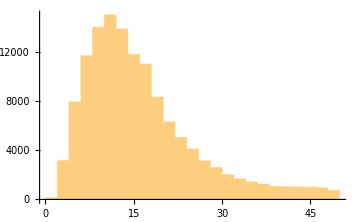
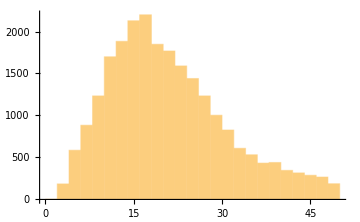
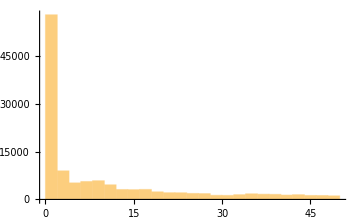
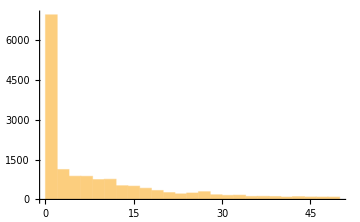
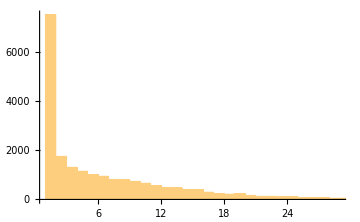

```mathematica
Histogram[#,ImageSize->Medium]&/@{fisHosp2,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}
```

```mathematica
FindDistribution[#,2]&/@{fisHosp2,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}
```

{{MixtureDistribution[{0.896417,0.103583},{NegativeBinomialDistribution[5,0.27444],DiscreteUniformDistribution[{22,49}]}],MixtureDistribution[{0.827312,0.172688},{NegativeBinomialDistribution[6,0.325782],PascalDistribution[8,0.271345]}]},{NegativeBinomialDistribution[6,0.229512],MixtureDistribution[{0.0208204,0.156882,0.178501,0.289493,0.254966,0.0993377},{BinomialDistribution[150,0.0356286],BinomialDistribution[49,0.189241],DiscreteUniformDistribution[{11,15}],DiscreteUniformDistribution[{16,22}],DiscreteUniformDistribution[{23,33}],DiscreteUniformDistribution[{34,49}]}]},{ZipfDistribution[49,0.283294],MixtureDistribution[{0.809352,0.190648},{ZipfDistribution[0.835379],PascalDistribution[7,0.221752]}]},{MixtureDistribution[{0.750269,0.249731},{ZipfDistribution[0.923718],PascalDistribution[4,0.182688]}],ZipfDistribution[49,0.301999]},{MixtureDistribution[{0.744576,0.255424},{ZipfDistribution[0.776343],NegativeBinomialDistribution[6,0.302174]}],LogSeriesDistribution[0.951683]}}

```mathematica
{fisHosp,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}={Select[fisHosp,0<#<30&],Select[fisUci,0<#<30&],Select[tiempoH,0<#<30&],Select[tiempoICU,0<#<30&],Select[tiempoHD,0<#<30&]};
```

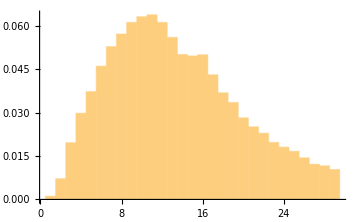
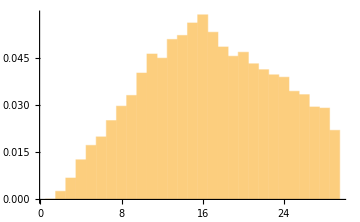
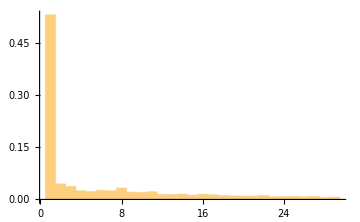
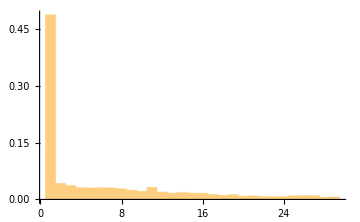
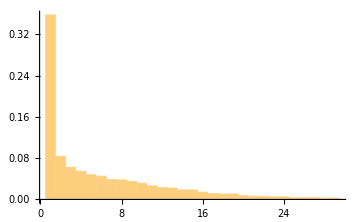

```mathematica
Histogram[#,Automatic,"PDF",ImageSize->Medium]&/@{fisHosp2,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}
```

```mathematica
Length/@{fisHosp2,fisUci2,tiempoH2,tiempoICU2,tiempoHD2}
```

{130264,23926,123027,15412,21308}

```mathematica
l=Length[fisHosp2]
```

130264

```mathematica
PadRight[fisUci2,l,"NA"]
```

{17,14,10,12,16,16,8,11,19,19,16,17,13,8,17,17,27,42,19,12,14,12,18,6,13,21,15,9,12,8,9,21,14,22,13,8,15,12,13,17,10,11,9,28,14,11,15,11,6,16,13,15,36,47,8,11,8,4,10,11,16,16,18,27,9,14,11,20,26,18,28,13,32,17,18,11,45,18,10,14,19,26,23,25,11,11,13,6,44,42,22,21,15,15,11,17,20,19,18,18,21,7,14,6,17,29,9,26,21,23,22,15,12,3,130037,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}
 |  |  |  |

```mathematica
data={{"fisHosp","fisUci","tiempoH","tiempoICU","tiempoHD","outcome"},Sequence@@Transpose[{fisHosp2,PadRight[fisUci2,l,"NA"],PadRight[tiempoH2,l,"NA"],PadRight[tiempoICU2,l,"NA"],PadRight[tiempoHD2,l,"NA"],Table[1,l]}]};
```

```mathematica
data[[1;;4]]//Grid
```

fisHosp | fisUci | tiempoH | tiempoICU | tiempoHD | outcome
11 | 17 | 8 | 11 | 3 | 1
13 | 14 | 8 | 3 | 1 | 1
9 | 10 | 10 | 5 | 4 | 1

```mathematica
Length/@{fisHosp2,PadRight[fisUci2,l,"NA"],PadRight[tiempoH2,l,"NA"],PadRight[tiempoICU2,l,"NA"],PadRight[tiempoHD2,l,"NA"],Table[1,l]}
```

{118103,118103,118103,118103,118103,118103}

```mathematica
Export["/home/lina/Documents/unCoVer/dataOscar.csv",data]
```

/home/lina/Documents/unCoVer/dataOscar.csv

```mathematica
"/home/lina/Documents/unCoVer/dataOscar.csv"
```

/home/lina/Documents/unCoVer/dataOscar.csv

## DataBase 16

```mathematica
data14=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBaseAnalysis14.csv"];
```

```mathematica
data14[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},IPMDEP2019→{12},BLEDEP2019→{13},BASSDEP2019→{14},HCDEP2019→{15},IEEDEP2019→{16},SAFAMDEP2019→{17},SASDEP2019→{18},IPMDEP2020→{19},BLEDEP2020→{20},BASSDEP2020→{21},HCDEP2020→{22},IEEDEP2020→{23},SAFAMDEP2020→{24},SASDEP2020→{25},IPMM2020→{26},BLEM2020→{27},BASSM2020→{28},HCM2020→{29},IEEM2020→{30},SAFAMM2020→{31},SASM2020→{32}|>

```mathematica
data14[[2;;,4]]
```

{BUGA,CARTAGENA,NEIVA,NEIVA,PALMIRA,BOGOTA,BOGOTA,BOGOTA,BOGOTA,BARRANQUILLA,BOGOTA,BOGOTA,BOGOTA,CALI,PEREIRA,BOGOTA,MEDELLIN,RIONEGRO,BOGOTA,BOGOTA,SANTA MARTA,BOGOTA,BOGOTA,IBAGUE,CARTAGO,PALMIRA,CALI,YUMBO,CARTAGENA,BELLO,BOGOTA,BOGOTA,DOSQUEBRADAS,CALI,BOGOTA,BOGOTA,BOGOTA,BOGOTA,GUATAPE,BELLO,BOGOTA,BOGOTA,245287,PALMIRA,BUCARAMANGA,BUCARAMANGA,BARRANCABERMEJA,MEDELLIN,MEDELLIN,CALI,CALI,ZONA BANANERA,PLATO,LINARES,CUCUTA,CUCUTA,MEDELLIN,BOGOTA,BOGOTA,CALI,CALI,CALI,CALI,MANIZALES,CUCUTA,SAN VICENTE DEL CAGUAN,GIRARDOT,TUNJA,GUATAVITA,COPACABANA,NEIVA,PUERTO SANTANDER,SANTANDER DE QUILICHAO,POPAYAN,SAN VICENTE DEL CAGUAN,MONTERIA,VILLAVICENCIO,VILLAVICENCIO,SAMANA,FLORIDABLANCA,SUAZA,ESPINAL,ANAPOIMA,LOS PATIOS,CALI}
 |  |  |  |

```mathematica
dataBase20202021=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
munC=Thread[dataBase20202021[[2;;,6]]->dataBase20202021[[2;;,5]]]//DeleteDuplicates/."barrancabermeja "->"BARRANCABERMEJA";
depC=Thread[dataBase20202021[[2;;,4]]->dataBase20202021[[2;;,3]]]//DeleteDuplicates;
```

```mathematica
prevalencias=Import["/home/lina/Documents/unCoVer/processingDataINS/prevalenciasEnfermedades.xlsx"];
```

```mathematica
varMun2=Thread[prevalencias[[1,2;;,5]]->prevalencias[[1,2;;,{7,8,9,10}]]]//DeleteDuplicates;
```

```mathematica
varMun2[[1]](*que significa los municipios con prevalencia 0*)
```

EL ENCANTO→{0.,0.,0.,0.}

```mathematica
Length@varMun2
```

1122

```mathematica
Complement[munC[[All,1]],varMun2[[All,1]]]
```

{barrancabermeja ,DARIEN}

```mathematica
data14[[2;;,4]]
```

```mathematica
Complement[data14[[2;;,4]],varMun2[[All,1]]]
```

{}

```mathematica
MemberQ[data14[[2;;,4]],"BARRANCABERMEJA"]
```

True

```mathematica
Complement[data14[[2;;,4]],munC[[All,1]]]
```

{CALIMA}

```mathematica
Complement[data14[[2;;,5]],depC[[All,1]]]
```

{}

```mathematica
data14[[1]]
```

{ID,AgeYears,Gender,Origen1,Origen2,Vaccination,Waves,PeaksValleys1,PeaksValleys2,1BedPathway,2BedPathway,IPMDEP2019,BLEDEP2019,BASSDEP2019,HCDEP2019,IEEDEP2019,SAFAMDEP2019,SASDEP2019,IPMDEP2020,BLEDEP2020,BASSDEP2020,HCDEP2020,IEEDEP2020,SAFAMDEP2020,SASDEP2020,IPMM2020,BLEM2020,BASSM2020,HCM2020,IEEM2020,SAFAMM2020,SASM2020}

```mathematica
data16={{"ID","AgeYears","Gender","Origen1","Origen2","Vaccination","Waves","PeaksValleys1","PeaksValleys2","1BedPathway","2BedPathway","IPMDEP2019","BLEDEP2019","BASSDEP2019","HCDEP2019","IEEDEP2019","SAFAMDEP2019","SASDEP2019","IPMDEP2020","BLEDEP2020","BASSDEP2020","HCDEP2020","IEEDEP2020","SAFAMDEP2020","SASDEP2020","IPMM2020","BLEM2020","BASSM2020","HCM2020","IEEM2020","SAFAMM2020","SASM2020","PRE_HTA2020","PRE_DM2020","PRE_ERC2020","PRE_CA2020","CODMun","CODDep"},Sequence@@data14[[2;;,{Sequence@@Range[1,Length[data14[[1]]]],4,4,5}]]};
```

```mathematica
data16[[2;;,-3]]=data16[[2;;,-3]]/.varMun2;
data16[[2;;,-2]]=data16[[2;;,-2]]/.munC/."CALIMA"->"NA";
data16[[2;;,-1]]=data16[[2;;,-1]]/.depC;
```

```mathematica
data16[[2;;,-3]]//DeleteDuplicates
```

{{13.82,5.17,2.75,451.7},{14.8,4.78,2.72,244.06},{11.43,4.72,3.41,1492.81},{11.26,4.48,2.72,1189.36},{10.55,3.46,2.64,1516.76},{13.23,4.12,2.01,631.07},{11.5,4.16,2.38,138.81},{11.47,3.95,2.14,665.92},{13.45,4.26,1.95,39.97},{12.99,3.88,2.6,158.92},{11.52,3.59,2.74,680.77},{8.81,3.23,1.77,653.12},{13.54,4.88,2.45,354.5},{9.51,3.85,1.16,433.61},{11.28,4.63,1.71,81.26},{10.01,3.74,1.68,2066.39},{5.09,1.37,0.85,72.97},{9.42,3.08,2.05,424.42},{39.4,21.32,10.27,2063.75},{10.28,3.04,1.39,97.65},{13.1,4.09,2.22,62.62},{6.07,1.27,1.7,453.69},{8.9,3.27,2.97,1642.48},{10.52,2.88,1.44,2038.28},{9.96,2.99,1.49,108.1},{7.96,2.81,1.47,834.94},{3.21,0.62,0.2,231.9},{7.64,2.43,1.77,338.23},{9.04,1.83,0.59,41.89},{10.83,4.37,2.07,2303.4},{7.52,1.87,2.37,765.83},{7.77,2.44,2.36,706.6},{11.95,2.9,2.49,229.78},{9.93,3.42,2.18,198.26},{10.21,3.28,2.68,690.35},{9.71,3.36,1.36,301.63},{11.73,4.75,2.49,580.88},{2.54,0.93,0.41,419.98},{7.29,2.02,2.03,227.69},{7.84,1.84,1.01,60.22},{9.47,3.25,1.98,1750.88},{4.82,1.2,0.69,336.05},{11.1,2.83,3.01,321.62},{8.88,3.29,1.04,804.34},{8.02,2.92,1.4,723.78},{6.07,1.56,2.14,170.62},{8.43,2.64,3.2,228.87},{5.21,2.04,0.77,166.29},{10.52,3.39,1.64,872.57},{7.07,1.99,1.12,1531.77},{7.72,2.21,1.96,651.77},{8.88,3.02,0.69,318.94},{6.88,2.82,0.64,807.81},{10.68,3.22,0.83,145.91},{8.32,3.45,1.41,571.31},{7.31,3.42,1.28,180.9},{8.98,1.4,0.05,163.41},{6.62,1.86,0.94,1077.24},{12.49,3.26,1.99,49.51},{4.45,0.71,0.1,457.44},{9.99,3.45,4.97,239.26},{5.57,1.85,1.01,539.59},{5.24,1.56,1.29,454.59},{4.48,0.87,0.13,319.72},{7.61,3.52,0.21,249.46},{12.94,5.73,3.87,339.62},{11.42,3.1,2.16,418.08},{7.22,2.42,1.95,219.19},{7.78,2.23,2.91,445.99},{8.08,2.42,1.19,409.65},{12.58,4.97,2.38,501.09},{4.15,1.03,0.93,224.25},{4.7,1.16,0.33,313.87},{6.2,1.75,2.11,386.14},{6.7,1.79,1.7,578.},{9.34,2.97,2.36,1726.6},{4.12,1.37,0.82,513.91},{5.08,0.99,0.16,689.98},{3.54,0.87,0.26,138.65},{11.05,2.46,0.82,581.86},{9.,1.93,0.28,35.56},{6.09,1.27,1.54,199.26},{6.37,2.69,0.29,167.63},{6.81,2.45,1.15,622.56},{11.07,4.14,4.04,883.86},{12.96,2.89,0.23,17.83},{8.48,2.36,0.38,22.74},{4.76,2.06,0.96,122.73},{11.71,5.06,1.32,529.03},{5.8,1.25,0.49,160.19},{8.12,2.04,0.87,176.79},{11.34,3.21,1.32,711.69},{11.08,3.59,2.86,303.75},{5.33,2.11,1.09,933.83},{6.17,1.41,1.16,742.16},{5.84,2.31,0.96,562.11},{6.05,1.58,1.,265.09},{6.4,2.17,0.78,806.09},{7.22,3.12,2.25,907.14},{3.28,1.08,0.39,414.3},{8.32,1.78,1.13,454.6},{8.7,2.92,3.5,391.45},{6.04,2.07,0.2,3.55},{3.9,1.48,0.25,31.59},{10.29,3.06,3.23,827.4},{3.56,0.57,0.11,176.64},{8.73,2.23,0.76,167.7},{7.1,2.44,0.33,447.71},{4.47,0.92,1.43,464.45},{5.06,1.61,0.57,882.99},{3.24,1.13,0.28,512.18},{2.58,0.29,0.58,27.42},{7.58,1.56,0.86,227.95},{6.26,1.19,0.63,79.78},{9.9,3.35,1.74,154.53},{3.78,1.22,0.14,105.68},{6.21,2.04,1.28,644.34},{4.36,1.17,0.53,193.98},{6.34,1.09,0.05,132.34},{6.28,2.97,0.02,2036.37},{5.28,1.12,0.37,353.48},{13.31,4.06,1.73,155.46},{10.29,2.73,3.42,623.49},{10.1,3.08,1.92,217.72},{4.06,0.84,0.03,573.09},{7.22,2.55,3.58,297.9},{4.3,1.07,0.06,431.47},{5.17,1.58,1.17,279.9},{5.02,0.91,0.45,83.4},{9.24,2.,0.26,402.35},{4.19,1.19,2.41,37.84},{5.44,1.54,0.6,496.57},{8.71,2.26,1.85,60.24},{9.19,2.31,0.63,163.89},{8.32,1.76,0.05,315.52},{7.52,1.93,1.96,413.07},{7.95,2.06,0.98,1836.46},{8.58,1.87,1.68,428.31},{12.8,2.16,1.38,231.58},{3.33,0.9,0.72,190.92},{8.4,2.53,0.56,301.32},{4.02,0.75,0.46,52.91},{4.91,1.28,1.34,957.23},{3.2,1.52,0.7,170.66},{4.12,0.85,0.4,151.8},{6.7,1.23,3.64,1183.62},{8.31,2.17,0.82,378.06},{7.48,1.92,1.36,391.3},{7.1,2.51,1.48,1312.06},{7.26,1.92,2.01,84.58},{5.67,1.58,0.64,724.38},{4.66,1.41,0.13,50.07},{9.61,2.22,0.68,488.89},{7.78,1.93,1.86,312.63},{5.86,1.45,0.19,453.16},{5.36,1.08,0.53,172.83},{3.08,0.71,0.02,51.24},{1.32,0.53,0.85,84.83},{10.15,3.95,2.19,1832.27},{6.95,1.52,0.61,412.38},{7.93,2.25,1.46,552.38},{2.64,0.34,0.07,85.05},{6.78,2.42,1.19,159.64},{7.04,1.55,1.23,394.36},{6.83,0.75,0.3,651.62},{8.98,2.21,1.24,298.89},{10.33,1.66,1.15,205.12},{7.43,1.79,0.32,862.72},{6.76,1.89,2.21,72.14},{8.49,2.93,2.38,1901.3},{7.43,1.67,1.31,368.35},{4.52,0.98,0.91,728.98},{10.55,3.53,0.5,1392.88},{7.1,2.39,2.64,427.26},{1.2,0.53,0.44,35.22},{8.57,1.74,1.11,448.12},{7.56,1.09,0.17,420.2},{7.02,1.41,0.09,535.82},{6.04,1.76,0.66,77.19},{8.72,3.43,2.02,686.62},{5.32,1.99,1.02,1148.59},{3.6,0.55,0.25,153.75},{0.14,0.,0.,30.32},{9.14,3.34,1.11,504.18},{2.91,1.1,1.25,192.17},{12.55,0.85,0.05,141.42},{6.07,0.62,0.04,84.65},{3.71,1.4,1.02,96.08},{6.52,1.35,0.13,26.89},{4.78,1.13,0.85,279.68},{10.55,2.82,1.46,182.19},{7.19,2.22,2.63,231.64},{6.36,1.57,0.54,182.61},{3.69,1.04,1.21,19.29},{5.06,1.33,1.96,385.36},{4.97,0.4,0.22,360.28},{7.79,1.77,0.12,26.52},{1.32,0.43,0.01,49.19},{5.26,1.06,0.27,33.55},{7.57,2.34,0.75,259.13},{7.25,3.17,0.91,469.63},{5.54,1.94,1.26,317.75},{5.87,1.74,2.18,327.05},{5.33,0.23,0.17,46.07},{3.14,1.06,0.62,81.4},{2.07,0.43,0.19,214.76},{10.03,3.56,2.23,28.25},{5.98,1.83,2.45,318.51},{5.35,1.82,2.9,290.34},{6.56,2.59,2.3,231.92},{2.22,0.6,0.09,136.42},{4.17,0.28,0.02,172.27},{2.43,0.37,0.12,67.63},{6.25,1.49,0.27,608.22},{3.42,1.31,0.03,465.44},{10.5,2.03,0.44,53.18},{13.1,4.42,2.03,38.31},{4.54,0.95,0.6,144.48},{3.03,0.61,0.,254.61},{5.48,2.02,1.27,613.52},{1.83,0.55,0.6,36.61},{7.92,1.13,0.36,166.97},{15.77,6.,3.12,948.8},{5.91,2.28,2.18,838.47},{4.3,0.89,0.27,235.07},{4.79,1.62,0.28,146.28},{6.29,0.75,0.37,160.76},{12.72,3.87,3.58,490.56},{6.24,1.65,0.33,146.18},{6.14,2.03,0.9,345.79},{4.74,1.01,1.,145.73},{7.42,1.88,1.33,226.9},{2.63,0.4,0.16,31.23},{3.13,0.95,0.44,299.88},{7.94,3.03,0.92,467.26},{2.94,0.66,0.62,98.09},{4.92,1.52,0.57,188.06},{5.96,1.83,2.45,103.3},{3.73,0.8,0.21,160.34},{1.97,0.61,0.58,316.55},{10.83,1.92,0.27,276.46},{1.65,0.36,0.07,15.85},{6.25,1.44,1.07,200.29},{8.12,3.58,1.87,20.94},{7.52,2.85,1.16,363.49},{7.27,1.06,0.91,21.82},{3.63,0.53,0.19,380.72},{1.58,0.68,0.5,138.49},{4.53,1.01,0.01,63.51},{10.28,3.4,2.5,943.},{5.54,0.54,0.18,316.81},{4.99,1.12,0.95,253.85},{3.95,1.23,1.1,202.25},{3.01,0.05,0.08,168.07},{7.14,1.38,0.68,169.08},{2.24,0.41,0.38,210.62},{8.55,2.2,0.64,584.91},{6.67,1.,0.13,140.82},{1.03,0.52,0.37,33.3},{7.21,1.13,1.48,403.31},{6.83,2.31,0.99,385.9},{8.45,4.16,1.76,409.51},{8.39,2.03,0.3,116.61},{8.48,2.9,1.94,184.21},{5.96,1.06,0.61,635.6},{4.74,1.45,1.5,317.16},{8.44,2.56,1.18,169.46},{5.52,1.41,1.04,295.72},{4.06,0.43,0.03,56.26},{4.63,0.58,0.05,169.},{5.45,2.05,1.47,570.72},{3.72,0.81,0.14,64.49},{8.1,2.08,0.94,10.39},{9.13,1.54,0.73,112.56},{7.14,1.69,1.33,363.59},{10.2,1.04,0.03,103.87},{2.87,2.38,0.02,71.76},{10.31,2.75,1.31,265.57},{5.65,1.16,0.23,153.51},{5.93,1.76,0.57,242.14},{5.55,1.76,1.8,2568.03},{9.04,2.62,1.87,574.58},{6.39,1.91,1.82,675.15},{2.65,0.96,0.73,105.43},{3.95,0.94,0.67,168.94},{2.23,1.29,0.51,81.95},{9.39,2.23,1.85,288.59},{5.81,1.48,1.21,863.21},{8.62,2.49,1.06,372.67},{4.14,0.89,0.23,305.56},{4.67,1.43,0.37,339.04},{4.49,1.71,0.51,390.63},{2.74,0.78,0.83,327.},{9.58,0.86,0.39,135.46},{3.8,0.88,0.14,311.79},{1.5,0.2,0.03,70.13},{7.82,1.75,0.16,57.72},{8.56,2.4,0.81,118.32},{6.86,0.46,0.41,380.98},{7.3,1.68,0.91,329.89},{8.13,2.25,1.47,517.19},{4.51,0.84,0.1,142.34},{7.05,1.37,0.56,402.36},{5.94,0.95,0.07,13.48},{16.38,4.86,1.81,26.62},{4.65,0.6,0.07,178.74},{7.67,0.72,2.55,556.72},{5.4,1.1,0.25,105.3},{3.87,0.89,0.12,322.12},{7.38,1.49,0.39,226.89},{6.14,1.31,0.78,362.94},{3.86,1.41,0.79,502.57},{5.13,1.14,0.8,197.19},{6.99,1.85,0.64,357.35},{7.8,1.57,0.46,150.4},{2.46,0.23,0.08,100.58},{2.42,0.42,0.32,487.28},{4.98,1.54,3.05,146.69},{4.66,1.14,0.91,486.64},{4.23,1.59,2.17,372.05},{7.22,0.82,0.16,6.24},{14.76,2.35,1.74,499.73},{2.88,0.43,0.25,54.29},{5.35,0.59,0.2,144.93},{6.13,1.12,0.58,213.44},{9.88,1.85,2.56,68.72},{3.88,0.91,0.1,142.1},{8.68,1.83,0.47,1165.88},{3.47,0.93,0.68,268.87},{9.03,1.87,0.89,39.59},{5.07,1.61,1.03,67.74},{3.71,0.74,0.08,169.34},{7.42,1.21,1.01,226.25},{6.17,2.07,1.88,189.37},{6.18,1.2,1.68,418.68},{2.35,0.89,0.34,127.15},{2.04,0.33,0.05,163.11},{9.93,1.11,0.15,255.58},{5.69,2.03,3.17,355.19},{4.49,0.64,0.05,167.12},{4.63,1.7,0.55,287.06},{4.4,0.91,0.31,229.18},{7.49,1.41,5.86,208.68},{3.16,0.47,0.12,29.57},{9.09,2.73,1.95,662.67},{3.8,0.71,0.5,165.96},{10.87,2.53,0.46,302.74},{6.48,1.51,0.31,277.27},{4.3,1.37,0.71,593.67},{4.75,1.53,2.58,295.75},{13.57,5.14,1.9,27.91},{4.55,1.68,0.54,504.01},{7.63,2.2,3.37,307.77},{6.76,1.35,0.99,303.92},{0.34,0.,0.1,0.},{4.04,1.06,0.65,246.5},{6.69,1.63,0.31,332.23},{7.09,1.8,0.68,623.82},{5.83,1.72,1.62,711.06},{7.05,0.39,0.25,70.48},{5.99,1.26,0.6,873.11},{5.6,0.99,0.33,439.2},{10.04,4.01,2.11,811.96},{7.71,2.51,1.07,370.35},{6.02,1.81,1.37,452.46},{7.44,1.44,0.53,45.44},{6.73,1.66,0.06,119.35},{0.98,0.32,0.12,77.69},{5.56,1.88,0.74,195.53},{10.51,2.7,1.2,22.84},{3.18,0.8,0.04,41.37},{5.21,0.87,0.85,165.95},{2.43,0.33,0.03,24.99},{6.99,1.69,2.64,733.7},{5.19,0.53,0.2,388.34},{3.9,1.55,1.02,379.85},{5.31,2.24,0.6,279.14},{4.12,1.22,0.17,71.12},{9.54,1.79,1.04,125.24},{2.69,0.42,0.06,34.33},{7.76,2.29,0.04,14.95},{3.25,1.13,0.99,92.81},{5.66,1.,0.81,173.83},{8.55,2.13,2.61,496.44},{9.64,2.01,1.25,602.32},{7.57,1.1,0.22,464.2},{9.2,3.13,1.35,493.31},{6.61,1.52,1.04,411.57},{8.51,2.83,1.37,6.38},{8.01,1.84,1.17,248.85},{5.94,1.63,0.83,453.63},{5.13,1.35,0.71,771.04},{3.1,0.11,0.28,142.12},{5.66,1.,1.9,361.08},{5.9,1.84,1.45,525.1},{8.28,2.01,3.18,345.46},{6.78,0.58,0.25,212.06},{3.2,0.65,0.08,14.91},{8.23,2.45,1.5,58.19},{9.28,2.28,0.22,509.02},{3.01,0.8,0.21,145.94},{4.32,0.99,1.37,372.29},{5.59,0.83,0.03,236.24},{6.7,2.3,1.14,231.82},{4.23,1.45,0.3,216.89},{9.17,1.94,2.13,461.48},{10.12,0.66,0.06,60.42},{11.47,4.3,1.35,36.27},{6.75,0.78,0.23,173.21},{5.74,1.27,0.11,16.73},{3.6,0.71,0.14,493.5},{7.64,2.02,1.98,272.56},{0.,0.,0.,0.},{4.44,0.47,1.53,47.75},{4.75,0.69,0.14,202.85},{4.83,0.39,0.08,171.01},{9.44,2.01,0.15,0.99},{5.32,1.67,0.04,456.73},{4.64,1.23,0.12,163.14},{4.64,1.53,2.43,141.28},{8.43,0.89,0.61,33.69},{3.94,0.97,0.14,339.65},{4.95,1.01,0.95,341.},{7.51,2.56,1.95,0.86},{3.92,0.63,0.74,27.95},{3.57,1.08,0.15,272.99},{6.62,2.2,0.19,370.45},{10.99,3.43,0.87,94.38},{8.36,1.02,0.64,473.91},{6.56,1.04,0.14,11.11},{5.36,1.24,0.99,102.71},{5.64,1.29,0.08,135.59},{8.23,4.85,1.27,5.63},{5.64,0.8,0.03,0.},{8.9,3.4,2.55,1076.},{6.54,1.53,0.06,95.55},{8.24,2.88,3.36,584.3},{7.48,1.98,0.95,247.45},{4.57,1.27,0.02,650.74},{3.93,1.26,0.7,273.8},{0.85,0.34,0.06,18.16},{10.18,2.74,0.64,954.87},{7.42,2.1,1.88,340.45},{8.14,2.94,2.46,336.3},{3.72,0.88,0.17,22.37},{10.36,3.62,0.47,30.86},{4.65,1.26,0.31,231.39},{4.71,1.39,0.77,436.01},{5.26,0.86,0.29,60.13},{6.1,0.84,0.22,99.3},{5.39,1.62,2.58,348.76},{0.42,0.24,0.,267.71},{2.74,0.3,0.05,260.25},{3.26,0.79,0.35,357.88},{2.44,0.61,0.36,154.83},{6.94,2.02,1.25,331.66},{7.23,2.15,0.27,41.61},{8.08,3.71,0.65,4.48},{5.89,0.62,0.69,229.56},{9.56,2.08,1.33,729.78},{1.91,0.37,0.06,0.},{0.92,0.12,0.,298.7},{6.54,1.56,0.45,242.97},{9.3,2.,0.24,438.95},{2.3,0.32,0.1,85.75},{5.36,1.55,2.54,952.45},{6.48,1.65,1.01,89.99},{14.84,3.09,0.55,367.9},{4.17,2.,0.03,921.2},{3.36,1.2,0.08,165.81},{2.35,0.78,0.38,161.47},{4.8,0.81,1.09,202.9},{0.44,0.25,0.04,116.8},{5.96,1.84,0.69,356.39},{8.19,2.42,0.15,18.16},{2.93,0.83,0.16,1025.82},{2.7,0.27,0.03,96.13},{3.08,0.7,0.07,93.03},{7.99,1.34,0.54,976.05},{0.,0.,0.,56.85},{5.64,1.07,0.16,36.94},{6.83,1.32,0.08,244.12},{5.18,0.52,0.12,46.36},{6.44,1.83,0.58,262.69},{7.63,1.34,0.13,496.38},{2.64,0.27,0.07,185.6},{5.09,1.77,1.18,608.84},{3.08,0.77,0.17,3.31},{6.91,1.33,1.47,359.75},{3.32,0.92,0.13,0.},{6.69,2.83,0.92,33.06},{11.48,2.72,4.77,36.7},{4.7,0.99,0.63,311.5},{9.48,4.81,5.16,1.77},{7.89,1.23,0.91,411.69},{6.05,1.5,0.3,45.63},{4.82,1.11,0.91,1609.5},{7.22,2.21,0.17,285.73},{3.09,0.78,0.22,209.98},{9.5,3.12,0.57,38.07},{10.36,3.09,0.26,0.},{7.47,2.15,1.03,432.06},{3.68,0.68,0.16,270.97},{5.65,3.63,0.65,380.38},{5.14,0.36,0.03,153.35},{8.77,2.04,0.17,76.88},{9.92,3.03,1.62,23.84},{3.05,0.48,0.02,536.57},{6.07,1.23,0.21,2.62},{5.53,0.57,0.06,208.},{5.54,0.91,0.25,254.07},{6.87,2.02,0.4,212.08},{7.62,2.56,2.14,746.79},{7.51,1.43,0.04,689.99},{3.24,0.53,0.12,94.32},{3.05,0.7,0.43,173.1},{3.69,0.56,0.15,468.14},{3.69,0.78,0.2,5.02},{2.24,0.29,0.16,98.11},{5.75,2.27,2.3,608.36},{3.28,0.9,0.13,354.8},{0.28,0.1,0.01,102.11},{10.57,1.77,0.62,447.81},{1.41,0.58,0.37,50.57},{5.5,0.91,0.46,385.99},{4.2,0.96,1.08,382.92},{4.67,1.05,1.64,269.88},{6.33,1.13,0.15,42.29},{4.89,0.68,0.23,350.91},{4.66,1.7,0.03,1035.24},{4.64,0.98,1.59,1013.29},{6.27,1.12,0.11,1266.3},{4.03,1.14,0.16,175.85},{6.81,2.23,1.12,190.13},{7.82,1.06,2.24,16.63},{4.41,1.56,0.06,372.4},{3.05,0.94,0.29,77.47},{3.84,0.84,0.1,586.49},{7.84,2.58,1.51,284.83},{4.51,0.36,0.09,494.7},{7.04,1.83,0.21,668.11},{6.66,1.36,1.61,1047.63},{8.92,2.51,0.16,15.17},{5.83,1.46,0.07,7.74},{3.64,0.53,0.36,238.93},{5.91,0.95,0.88,42.82},{5.13,1.41,0.33,147.81},{5.92,1.17,0.66,31.42},{3.29,0.86,0.08,120.37},{9.06,4.57,0.06,18.69},{6.38,1.93,3.61,124.97},{1.43,0.11,0.,495.02},{2.46,0.53,0.05,59.38},{2.5,0.42,0.07,114.11},{11.83,2.3,1.33,121.26},{2.53,0.3,0.07,281.1},{9.17,2.05,0.43,0.87},{4.42,1.38,0.06,241.84},{7.48,0.92,0.58,490.74},{5.3,0.79,0.15,75.11},{7.32,1.65,0.39,10.35},{10.94,3.37,1.56,96.89},{1.11,0.31,0.09,261.92},{6.92,2.18,0.39,12.91},{1.66,0.58,0.07,102.62},{4.83,1.19,0.12,119.57},{3.62,1.11,0.19,238.05},{6.92,1.86,2.23,3172.75},{5.87,2.17,0.26,37.1},{6.62,1.09,1.35,438.34},{4.19,1.09,0.09,224.35},{7.09,0.97,0.76,115.99},{1.9,0.28,0.12,280.7},{4.33,0.22,0.05,246.22},{10.09,1.12,3.64,0.},{8.79,3.67,1.24,55.77},{3.81,0.4,0.32,123.16},{2.95,0.6,0.1,33.57},{7.64,2.11,0.67,25.75},{8.61,2.3,1.25,486.98},{9.15,2.27,1.36,154.93},{6.57,1.76,0.77,243.71},{4.67,0.8,1.,167.8},{3.39,1.05,0.16,77.7},{3.41,0.65,0.25,191.},{8.75,2.76,0.47,44.34},{8.61,0.88,0.9,388.68},{6.23,0.87,0.72,87.42},{1.58,0.55,0.28,297.28},{4.17,0.42,0.02,81.12},{6.,1.25,0.21,59.7},{7.97,2.28,0.4,2.48},{6.46,0.53,0.04,291.55},{6.3,1.75,0.48,758.53},{3.58,1.27,2.18,66.19},{4.29,0.98,0.1,181.24},{10.18,3.65,0.14,21.59},{7.1,1.12,0.24,480.43},{3.46,0.41,0.59,129.07},{4.62,1.2,0.04,439.11},{4.08,0.18,0.,327.11},{2.2,1.71,0.15,446.65},{7.46,0.97,0.63,174.15},{7.19,1.22,0.03,596.9},{6.62,1.39,1.33,432.32},{5.49,0.41,1.9,119.47},{2.99,0.69,0.97,77.97},{7.31,2.55,0.48,356.43},{9.48,3.04,0.9,556.59},{6.95,1.31,0.36,44.56},{5.56,3.06,1.48,990.78},{4.7,1.58,0.14,316.31},{1.99,1.42,0.47,6.26},{7.59,1.35,0.65,505.77},{6.84,1.98,0.46,441.47},{7.37,1.1,0.15,638.99},{6.25,1.15,1.47,278.34},{5.12,1.77,0.7,370.08},{5.48,2.34,2.41,424.99},{3.68,1.19,0.,113.09},{2.05,1.99,0.11,213.32},{2.6,0.46,0.17,20.21},{5.87,0.83,0.16,98.29},{9.71,3.45,0.57,273.24},{7.3,1.38,0.13,247.28},{2.45,0.47,0.06,104.93},{5.25,0.41,0.11,79.63},{5.22,1.15,0.17,237.15},{8.46,1.93,0.07,77.51},{6.,1.84,1.85,624.77},{3.13,0.2,0.04,62.72},{4.08,1.17,0.65,149.85},{7.57,0.96,0.12,114.44},{4.88,0.72,0.36,70.96},{5.58,1.75,0.03,564.7},{15.6,2.42,0.13,17.7},{5.39,0.81,0.2,302.53},{7.48,1.86,0.37,17.06},{3.56,1.43,0.02,390.15},{7.92,0.63,0.16,161.87},{3.78,0.3,0.12,164.6},{8.19,1.33,1.1,9.},{4.64,2.07,0.06,338.6},{6.43,2.84,0.02,309.98},{3.79,1.13,0.13,279.21},{3.76,0.81,0.04,31.},{1.57,0.54,0.02,134.98},{6.65,1.48,0.62,78.37},{9.01,3.05,3.96,1111.51},{3.1,0.69,0.04,38.08},{2.08,0.49,0.24,134.12},{2.99,0.62,0.19,1125.28},{6.71,1.44,1.96,220.19},{3.81,0.9,0.02,704.81},{1.55,0.47,0.14,184.14},{8.06,1.32,0.12,35.76},{6.3,1.86,1.62,496.82},{2.25,0.79,0.02,179.02},{6.45,0.6,0.03,251.95},{8.91,1.34,0.18,14.6},{7.4,2.66,0.79,475.11},{0.9,0.28,0.3,73.48},{5.26,1.05,1.79,461.37},{6.53,1.47,2.83,403.86},{5.19,1.19,0.32,273.61},{4.44,1.9,0.15,276.45},{6.29,0.97,0.07,983.41},{3.72,0.86,0.14,362.11},{4.62,0.96,0.23,266.04},{6.75,0.73,0.13,66.57},{0.57,0.05,0.06,160.67},{4.83,1.05,0.25,317.46},{8.39,2.12,2.16,311.09},{6.51,0.47,0.31,71.57},{4.24,0.89,0.26,185.03},{8.89,1.24,0.29,114.02},{6.64,1.79,0.32,264.41},{1.87,0.3,0.04,44.39},{6.01,1.67,0.7,467.66},{6.87,4.78,1.65,312.59},{2.58,0.8,0.08,37.57},{4.14,0.25,0.1,169.56},{6.09,2.04,0.14,8.69},{5.21,1.51,0.24,746.61},{5.64,1.51,1.25,244.94},{3.84,1.17,0.83,286.89},{4.68,0.85,0.33,127.7},{7.66,1.63,0.09,23.07},{5.27,0.13,0.08,86.95},{2.94,0.54,1.62,157.63},{5.07,0.27,0.07,100.55},{3.43,0.56,0.1,270.78},{6.44,1.8,0.59,217.54},{3.74,0.78,0.51,239.16},{9.42,2.71,0.09,179.8},{0.11,0.,0.,2443.93},{4.59,0.99,0.27,495.01},{3.24,0.95,0.11,27.06},{5.26,1.37,1.5,269.39},{7.47,1.85,1.17,5.76},{6.72,1.22,0.7,71.27},{4.64,1.14,0.24,52.7},{1.83,0.75,0.19,312.94},{3.71,1.24,0.08,567.34},{1.26,0.11,0.15,140.65},{4.69,0.46,0.16,519.29},{6.51,1.96,0.64,802.42},{1.32,0.18,0.,73.12},{6.29,1.19,0.03,1072.14},{5.25,1.74,0.09,621.33},{5.82,1.2,0.23,276.04},{9.47,1.51,0.32,27.72},{5.21,1.15,1.5,269.9},{5.32,1.23,0.15,426.11},{3.21,0.59,0.51,303.83},{3.36,1.23,0.07,16.33},{6.56,0.86,0.,661.89},{4.6,1.14,0.09,171.72},{3.09,1.37,0.,506.17},{6.35,2.45,0.19,410.66},{6.64,1.79,2.04,138.47},{5.43,5.54,1.66,860.96},{7.18,1.54,0.05,611.62},{6.71,0.5,0.04,288.04},{4.25,0.6,1.01,559.65},{3.6,0.49,1.09,170.36},{5.31,1.22,1.75,373.68},{10.42,1.71,0.4,201.29},{4.25,0.81,0.75,123.03},{4.66,0.56,0.14,424.82},{3.63,0.93,0.12,383.7},{5.93,1.82,0.23,395.19},{1.98,0.65,0.81,268.91},{2.86,0.6,0.16,70.27},{5.02,0.75,0.05,152.97},{2.24,0.45,0.05,239.85},{5.98,2.56,0.17,190.72},{3.75,0.88,0.1,261.54},{7.08,1.92,1.63,252.72},{8.13,1.2,0.19,18.56},{4.37,1.29,1.15,1018.59},{6.02,1.17,1.66,546.57},{4.67,1.11,0.96,1337.89},{1.92,0.77,0.14,0.},{6.52,1.46,0.02,334.57},{3.92,0.61,0.41,45.24},{5.92,0.9,1.09,203.52},{11.08,1.19,0.14,627.36},{7.06,0.96,0.72,289.82},{10.31,0.96,0.31,277.81},{7.73,4.2,1.,389.1},{6.84,2.16,0.6,367.72},{7.56,1.42,1.9,377.67},{6.94,1.46,0.56,252.59},{2.4,0.84,0.08,122.22},{4.74,1.47,0.93,484.96},{6.01,2.98,0.18,5.83},{4.9,1.28,0.04,231.02},{9.27,2.14,0.31,51.83},{8.17,2.59,0.24,118.44},{5.1,0.6,0.61,172.31},{5.92,1.15,0.32,491.51},{6.84,1.1,0.05,243.68},{1.71,0.3,0.78,16.51},{2.65,0.65,0.03,56.53},{2.87,0.64,0.1,302.67},{0.95,0.15,0.05,63.11},{5.29,0.18,0.01,318.79},{3.24,1.05,0.15,277.37},{6.75,1.31,0.33,419.89},{1.01,0.11,0.04,202.54},{7.69,1.14,2.45,153.84},{8.32,2.97,3.13,626.26},{5.19,1.,0.09,72.42},{4.89,1.1,0.38,208.37},{2.55,0.73,0.17,404.07},{5.11,0.75,1.76,353.08},{1.43,0.3,0.09,448.84},{7.65,2.39,3.84,137.54},{2.59,0.79,0.88,290.78},{6.57,0.66,0.21,333.17},{6.74,2.55,1.24,157.63},{6.4,1.1,0.1,67.87},{6.4,1.02,0.6,228.34},{4.06,0.71,0.16,890.11},{6.34,1.34,1.77,639.44},{2.27,0.45,0.02,208.74},{3.01,0.26,0.04,120.18},{4.84,0.61,0.15,284.13},{6.23,2.24,1.31,410.36},{4.01,0.94,0.03,223.58},{6.12,1.86,0.56,2692.66},{8.84,2.28,1.43,664.04},{5.9,1.62,1.38,780.72},{6.24,1.52,2.37,148.28},{7.14,2.22,0.47,8.3},{12.75,2.95,0.13,4.26},{5.53,1.75,1.59,457.93},{6.67,2.2,0.62,141.19},{6.06,0.74,0.29,1158.6},{6.22,0.52,0.3,226.18},{1.97,0.28,0.02,80.84},{5.6,0.66,0.13,188.13},{4.12,1.55,0.06,292.29},{5.67,1.26,0.25,977.07},{3.97,0.74,0.12,484.35},{6.14,1.23,0.97,395.94},{5.54,1.37,0.44,356.89},{7.16,2.47,1.24,619.01},{6.47,1.65,0.39,648.12},{7.1,1.88,1.7,175.18},{4.02,0.52,0.14,157.36},{5.33,1.52,0.75,553.35},{13.72,1.05,0.6,172.63},{5.75,1.28,0.18,637.11},{4.81,0.46,0.07,255.41},{4.9,1.79,0.99,219.83},{6.3,0.49,0.13,231.7},{6.67,1.62,0.3,43.99},{5.19,1.87,1.42,194.02},{9.47,2.37,0.75,76.86},{2.04,0.72,0.04,67.25},{7.55,1.55,0.77,952.37},{0.,0.,0.,1842.61},{3.82,0.93,0.71,537.56},{3.66,1.03,0.02,418.01},{4.17,0.67,1.93,203.04},{4.68,1.16,0.86,248.28},{5.88,0.46,0.04,101.66},{6.03,0.96,0.09,360.96},{6.17,1.32,0.09,75.64},{1.45,0.16,0.05,49.31},{7.7,1.48,0.,201.57},{1.8,0.45,0.2,156.77},{5.37,0.84,0.14,234.83},{4.2,0.77,0.38,59.23},{3.6,0.96,0.24,610.37},{3.96,1.18,0.,574.34},{8.45,2.28,1.09,538.84},{4.57,0.88,0.03,272.52},{3.64,0.94,0.16,250.5},{4.85,0.85,0.12,95.53},{3.78,1.,0.24,205.12},{4.93,0.65,0.07,98.68},{6.56,0.63,0.05,221.2},{4.85,1.42,1.6,298.81},{5.46,1.63,1.48,774.4},{6.18,0.93,0.05,368.57},{3.99,0.35,0.05,366.52},{5.49,1.72,0.28,31.61},{5.03,0.91,0.15,30.75},{2.1,0.36,0.13,161.02},{1.27,0.39,0.,5.},{7.22,0.68,0.13,6.55},{5.06,1.49,0.09,175.94},{6.58,1.35,0.32,162.38},{6.37,1.18,0.2,215.69},{2.25,0.92,0.05,190.74},{2.32,0.43,0.84,60.01},{6.08,1.28,0.22,270.08},{5.2,1.21,1.96,264.9},{7.61,1.1,2.22,19.95},{5.49,1.01,0.08,229.33},{2.39,0.55,0.04,253.87},{2.87,0.68,0.49,338.7},{7.59,2.37,0.12,320.66},{6.85,1.62,0.92,359.19},{4.41,0.52,0.17,231.45},{6.24,0.91,0.46,166.04},{3.01,0.49,0.75,354.31},{3.22,0.62,0.03,165.89},{6.34,1.05,0.05,483.73},{4.58,0.86,0.15,311.01},{4.61,1.61,0.05,364.96},{12.65,1.65,0.27,328.15},{3.44,0.81,0.15,591.62},{2.24,0.25,0.17,160.64},{0.,0.,0.,77.95},{6.25,0.77,0.63,236.37},{5.7,0.63,0.42,63.91},{9.,2.56,2.46,179.04},{5.14,0.7,0.13,216.82},{5.27,0.65,0.87,165.79},{6.11,1.,0.01,416.48},{3.54,0.73,0.08,209.38},{6.82,1.32,1.96,236.57},{5.86,0.98,0.09,174.06},{12.5,2.34,0.27,7.08},{4.82,1.24,0.64,351.56},{6.03,2.3,0.34,501.02},{3.75,0.39,0.27,352.59},{7.62,1.58,0.03,263.08},{5.22,0.91,0.31,576.61},{7.85,1.18,0.52,178.1},{0.12,0.,0.,0.},{3.48,0.77,1.21,1166.3},{6.06,1.12,0.17,363.36},{5.1,1.45,0.09,652.85},{5.94,0.34,0.02,206.45},{6.2,1.38,1.13,352.23},{6.75,1.87,0.09,0.},{5.65,0.89,0.21,317.8},{6.56,0.16,0.23,384.33},{7.95,2.62,1.9,275.},{4.36,1.,0.1,85.16},{0.83,0.09,0.03,15.2},{5.48,0.7,0.3,182.78},{8.6,2.01,0.06,157.19},{0.,0.,0.,0.76},{6.11,0.89,0.87,285.61},{9.73,1.47,0.55,320.98},{2.3,0.27,0.,174.17},{3.91,0.61,0.11,352.27},{4.56,1.38,0.86,81.02},{4.7,0.76,0.46,370.98},{2.3,0.17,0.07,224.89},{0.71,0.27,0.26,313.53},{8.51,1.07,0.04,235.84},{3.02,0.47,0.11,109.35},{4.16,0.73,0.18,77.51},{5.88,2.15,1.27,117.15},{4.96,1.46,0.08,230.},{7.72,1.34,0.08,64.11},{5.,0.4,0.06,61.72},{4.52,1.81,0.07,881.75},{5.87,1.33,0.42,86.18},{4.19,0.63,0.11,12.27},{7.32,2.2,1.58,404.29},{5.79,1.35,0.14,252.95},{3.52,0.2,0.12,120.57},{6.57,0.78,0.07,114.9},{9.56,1.66,0.25,89.12},{10.12,5.01,0.24,8.6},{5.86,1.01,0.22,209.75},{4.1,0.56,0.11,256.3},{5.86,1.01,0.13,113.82},{5.53,0.81,0.06,25.45},{5.57,0.66,0.09,212.59},{3.45,0.85,0.91,788.58},{7.85,1.57,0.36,507.56},{2.54,0.34,0.14,323.82},{4.28,1.12,0.03,698.74},{3.32,0.71,0.17,212.93},{8.22,1.16,0.04,213.},{5.11,0.56,1.04,181.2},{0.71,0.09,0.05,58.52},{2.64,0.3,0.05,64.45},{6.29,2.4,1.02,38.57},{4.82,1.65,0.04,99.28},{3.26,0.53,0.1,187.14},{1.74,0.62,0.06,52.05},{5.31,1.05,0.47,386.71},{0.48,0.06,0.05,256.56},{7.95,2.41,0.28,55.22},{4.59,0.37,0.,84.81},{6.4,1.12,1.07,589.32},{2.44,1.09,0.05,127.44},{7.78,1.48,0.92,127.09},{4.02,0.99,0.13,0.},{4.65,0.46,0.02,110.88},{4.9,0.91,0.06,67.28},{7.4,2.45,0.04,91.72},{1.9,0.24,0.02,51.89},{4.12,0.43,0.07,60.76},{2.32,0.03,0.01,96.98},{5.78,0.39,0.06,201.89},{7.43,1.,0.21,57.16},{6.54,0.68,0.08,37.27},{6.39,1.17,0.05,170.34},{6.18,0.8,2.45,649.99},{4.84,1.22,0.95,238.84},{5.07,0.73,0.37,109.8},{4.39,0.47,3.05,265.86},{3.92,0.45,0.02,509.88},{15.96,5.38,0.08,581.75},{4.44,0.94,0.59,17.02},{1.86,0.17,0.22,179.76},{5.09,1.58,0.11,91.54},{8.93,1.98,0.34,151.92},{1.19,0.06,0.01,136.49},{5.26,1.03,0.27,46.97},{5.86,0.64,0.25,304.29},{3.39,0.36,0.12,20.69},{7.81,0.53,0.06,79.08},{6.94,1.74,0.79,7.94},{4.29,0.35,0.52,229.6},{6.64,0.83,0.28,187.37},{3.99,0.39,0.17,46.59},{4.64,1.46,0.05,1153.86},{5.68,1.48,0.03,261.73},{6.52,1.27,0.03,151.26},{2.73,0.35,0.02,310.51},{0.72,0.06,0.05,403.12},{5.89,0.48,1.07,250.94},{1.66,0.38,0.06,95.07},{4.24,0.56,0.01,692.38},{7.09,1.02,0.15,30.79},{5.63,1.11,0.,85.93},{6.64,0.39,1.2,256.88},{5.84,0.42,0.09,16.62},{2.72,0.09,0.02,221.19},{4.64,0.58,0.21,161.77},{2.6,0.17,0.03,80.57},{0.51,0.18,0.18,417.73},{6.36,1.34,0.08,118.82},{8.35,0.23,0.11,10.55}}

```mathematica
n=Flatten/@data16;
```

```mathematica
n[[1;;3]]//Grid
```

ID | AgeYears | Gender | Origen1 | Origen2 | Vaccination | Waves | PeaksValleys1 | PeaksValleys2 | 1BedPathway | 2BedPathway | IPMDEP2019 | BLEDEP2019 | BASSDEP2019 | HCDEP2019 | IEEDEP2019 | SAFAMDEP2019 | SASDEP2019 | IPMDEP2020 | BLEDEP2020 | BASSDEP2020 | HCDEP2020 | IEEDEP2020 | SAFAMDEP2020 | SASDEP2020 | IPMM2020 | BLEM2020 | BASSM2020 | HCM2020 | IEEM2020 | SAFAMM2020 | SASM2020 | PRE_HTA2020 | PRE_DM2020 | PRE_ERC2020 | PRE_CA2020 | CODMun | CODDep
1 | 34 | M | BUGA | VALLE | No | NA | 1 | valley | 1 | 1 | 10.8 | 42.3 | 2.4 | 4.6 | 6. | 4.9 | 9.9 | 11.1 | 34.9 | 1.2 | 4.4 | 3. | 3.2 | 10.1 | 12.3 | 40.9 | 4.2 | 4.8 | 1.1 | 1.6 | 13.7 | 13.82 | 5.17 | 2.75 | 451.7 | 76111 | 76
2 | 85 | F | CARTAGENA | CARTAGENA | No | NA | 1 | valley | 1 | 1 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 14.8 | 4.78 | 2.72 | 244.06 | 13001 | 13001

```mathematica
Export["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBaseAnalysis16.csv",n];
```